# HighPT

## Flavor bounds from high-p_T tails at LHC

```mathematica
Quit[]
```

#### Set package directory

Make sure that the package directory is in the $Path.

```mathematica
SetDirectory@ ParentDirectory@ NotebookDirectory[];
(*AppendTo[$Path, "/path/to/HighPT"];*)
```

#### Loading the package

```mathematica
<<HighPT`
```

-Graphics-

Authors: Lukas Allwicher, Darius A. Faroughy, Florentin Jaffredo, Olcyr Sumensari, and Felix Wilsch

References: arXiv:2207.10756http://arxiv.org/abs/2207.10756Nonehttp://arxiv.org/abs/2207.10756HyperlinkHyperlinkActive, arXiv:2207.10714http://arxiv.org/abs/2207.10714Nonehttp://arxiv.org/abs/2207.10714HyperlinkHyperlinkActive

Website: https://highpt.github.iohttps://highpt.github.ioNonehttps://highpt.github.ioHyperlinkHyperlinkActive

HighPT is free software released under the terms of the MIT License.

Version: 1.0.2

____________________________________

Initialized SMEFT mode:

Maximum operator dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

```mathematica
PrependTo[$ContextPath, "HighPT`PackageScope`"];
```

#### Load MaTeX`

```mathematica
<<MaTeX`;
SetOptions[MaTeX,Magnification-> 2.2,"Preamble"->{"\\usepackage[dvipsnames]{xcolor}","\\definecolor{mygreen}{rgb}{0,0.45,0}","\\definecolor{mygreen2}{rgb}{0,0.8,0}","\\definecolor{myblue}{rgb}{0,0,0.8}","\\definecolor{myblue2}{rgb}{0,0,0.45}","\\definecolor{myred}{rgb}{0.65,0,0}","\\definecolor{myred2}{rgb}{0.9,0,0}","\\definecolor{mygray}{rgb}{0.4,0.4,0.4}","\\definecolor{myorange}{rgb}{0.65,0.325,0}","\\definecolor{mypurple}{rgb}{0.5,0,0.5}","\\usepackage{tikz}","\\newcommand{\\logo}[0]{\\begin{tikzpicture}[scale=1]

  %\\clip (-0.6,0.4) rectangle (1.3,-0.3);
  \\clip (-0.6,0.4) rectangle (0.6,-0.3);
  
  \\node[] at (0,0) {${\\tt HighPT}$};
  %\\node[right] at (0.85,0.07) {\\pgftext{\\includegraphics[scale=0.035]{/Users/allwicher/Dropbox/Flavor@LHC/Analyses/cannabis.pdf}}};
  
\\end{tikzpicture}}"}];
```

#### Preamble shit for plotting [run]

```mathematica
amarillo=RGBColor["#ffcc00"]
rojo=RGBColor["#cf142b"]
azul=RGBColor["#0000F3"](*RGBColor["#00247d"]*)

Yticks[label_,mag_]:={{2250,MaTeX[If[label==True,"2250",""],Magnification->mag],{0.03,0}},
			{2200,,{0.01,0}},{2150,,{0.01,0}},{2100,,{0.01,0}},{2050,,{0.01,0}},
			{2000,MaTeX[If[label==True,"2000",""],Magnification->mag],{0.03,0}},  
			{1950,,{0.01,0}},{1900,,{0.01,0}},{1850,,{0.01,0}},{1800,,{0.01,0}},
			{1750,MaTeX[If[label==True,"1750",""],Magnification->mag],{0.03,0}},
			{1700,,{0.01,0}},{1650,,{0.01,0}},{1600,,{0.01,0}},{1550,,{0.01,0}},
			{1500,MaTeX[If[label==True,"1500",""],Magnification->mag],{0.03,0}},
			{1450,,{0.01,0}},{1400,,{0.01,0}},{1350,,{0.01,0}},{1300,,{0.01,0}},
			{1250,MaTeX[If[label==True,"1250",""],Magnification->mag],{0.03,0}},
			{1200,,{0.01,0}},{1150,,{0.01,0}},{1100,,{0.01,0}},{1050,,{0.01,0}},
			{1000,MaTeX[If[label==True,"1000",""],Magnification->mag],{0.03,0}},
			{950,,{0.01,0}},{900,,{0.01,0}},{850,,{0.01,0}},{800,,{0.01,0}},
			{750,MaTeX[If[label==True,"750",""],Magnification->mag],{0.03,0}},
			{700,,{0.01,0}},{650,,{0.01,0}},{600,,{0.01,0}},{550,,{0.01,0}},
			{500,MaTeX[If[label==True,"500",""],Magnification->mag],{0.03,0}},
			{450,,{0.01,0}},{400,,{0.01,0}},{350,,{0.01,0}},{300,,{0.01,0}}}

Xticks[l_,label_,mag_]:={
			{ l[[1]]/5+l[[3]],,{0.01,0}},
			{l[[3]],MaTeX[If[label==True,ToString[l[[3]]],""],Magnification->mag],{0.02,0}},  
			{4l[[1]]/5+l[[2]],,{0.01,0}},{3l[[1]]/5+l[[2]],,{0.01,0}},{2l[[1]]/5+l[[2]],,{0.01,0}},{ l[[1]]/5+l[[2]],,{0.01,0}},
			{l[[2]],MaTeX[If[label==True,ToString[l[[2]]],""],Magnification->mag],{0.02,0}},
			{4l[[1]]/5+l[[1]],,{0.01,0}},{3l[[1]]/5+l[[1]],,{0.01,0}},{2l[[1]]/5+l[[1]],,{0.01,0}},{ l[[1]]/5+l[[1]],,{0.01,0}},
			{l[[1]],MaTeX[If[label==True,ToString[l[[1]]],""],Magnification->mag],{0.02,0}},
			{4l[[1]]/5,,{0.01,0}},{3l[[1]]/5,,{0.01,0}},{2l[[1]]/5,,{0.01,0}},{l[[1]]/5,,{0.01,0}},
			{0.0,MaTeX[If[label==True,"0",""],Magnification->mag],{0.03,0}},
			{-4l[[1]]/5,,{0.01,0}},{-3l[[1]]/5,,{0.01,0}},{-2l[[1]]/5,,{0.01,0}},{-l[[1]]/5,,{0.01,0}},
			{-l[[1]],MaTeX[If[label==True,ToString[-l[[1]]],""],Magnification->mag],{0.02,0}},
			{-4l[[1]]/5-l[[1]],,{0.01,0}},{-3l[[1]]/5-l[[1]],,{0.01,0}},{-2l[[1]]/5-l[[1]],,{0.01,0}},{ -l[[1]]/5-l[[1]],,{0.01,0}},
			{-l[[2]],MaTeX[If[label==True,ToString[-l[[2]]],""],Magnification->mag],{0.02,0}},
			{-4l[[1]]/5-l[[2]],,{0.01,0}},{-3l[[1]]/5-l[[2]],,{0.01,0}},{-2l[[1]]/5-l[[2]],,{0.01,0}},{ -l[[1]]/5-l[[2]],,{0.01,0}},
			{-l[[3]],MaTeX[If[label==True,ToString[-l[[3]]],""],Magnification->mag],{0.02,0}}
			}

Yticks1[label_,mag_]:={
{10000,MaTeX[If[label==True,"10000",""],Magnification->mag],{0.02,0}},
{9000,MaTeX[If[label==True," ",""],Magnification->mag],{0.02,0}},
{8000,MaTeX[If[label==True," ",""],Magnification->mag],{0.02,0}},
			{7000,MaTeX[If[label==True," ",""],Magnification->mag],{0.02,0}},
			{6000,MaTeX[If[label==True," ",""],Magnification->mag],{0.02,0}},
			{5000,MaTeX[If[label==True," ",""],Magnification->mag],{0.02,0}},
			{4000,MaTeX[If[label==True," ",""],Magnification->mag],{0.02,0}},
			{3000,MaTeX[If[label==True," ",""],Magnification->mag],{0.02,0}},
			{2000,MaTeX[If[label==True,"2000",""],Magnification->mag],{0.02,0}},
			{1000,MaTeX[If[label==True,"1000",""],Magnification->mag],{0.02,0}},
			{900,MaTeX[If[label==True,"",""],Magnification->mag],{0.01,0}},{800,MaTeX[If[label==True,"",""],Magnification->mag],{0.01,0}},
			{700,MaTeX[If[label==True,"",""],Magnification->mag],{0.01,0}},{600,MaTeX[If[label==True,"",""],Magnification->mag],{0.01,0}},
			{500,MaTeX[If[label==True,"500",""],Magnification->mag],{0.02,0}},
		          {400,MaTeX[If[label==True,"",""],Magnification->mag],{0.01,0}},{300,MaTeX[If[label==True,"",""],Magnification->mag],{0.01,0}},
                            {200,MaTeX[If[label==True,"200",""],Magnification->mag],{0.01,0}}}

Xticks1[label_,mag_]:={
{1.4,MaTeX[If[label==True,"1.4",""],Magnification->mag],{0.025,0}},
{1.39,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.38,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.37,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.36,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.35,MaTeX[If[label==True," ",""],Magnification->mag],{0.025,0}},
{1.34,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.33,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.32,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.31,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.3,MaTeX[If[label==True,"1.3",""],Magnification->mag],{0.025,0}},
{1.29,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.28,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.27,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.26,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.25,MaTeX[If[label==True," ",""],Magnification->mag],{0.025,0}},
{1.24,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.23,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.22,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.21,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.2,MaTeX[If[label==True,"1.2",""],Magnification->mag],{0.025,0}},
{1.19,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.18,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.17,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.16,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.15,MaTeX[If[label==True," ",""],Magnification->mag],{0.025,0}},
{1.14,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.13,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.12,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.11,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.1,MaTeX[If[label==True,"1.1",""],Magnification->mag],{0.025,0}},
{1.09,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.08,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.07,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.06,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.05,MaTeX[If[label==True," ",""],Magnification->mag],{0.025,0}},
{1.04,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.03,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.02,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.01,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
		          {1.0,MaTeX[If[label==True,"1.0",""],Magnification->mag],{0.025,0}}
			}


Xticks2[label_,mag_]:={
{1.05,MaTeX[If[label==True,"1.05",""],Magnification->mag],{0.025,0}},
{1.048,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.046,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.044,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.042,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.04,MaTeX[If[label==True,"1.04",""],Magnification->mag],{0.025,0}},
{1.038,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.036,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.034,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.032,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.03,MaTeX[If[label==True,"1.03",""],Magnification->mag],{0.025,0}},
{1.028,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.026,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.024,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.022,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.02,MaTeX[If[label==True,"1.02",""],Magnification->mag],{0.025,0}},
{1.018,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.016,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.014,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.012,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.01,MaTeX[If[label==True,"1.01",""],Magnification->mag],{0.025,0}},
{1.008,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.006,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.004,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.002,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.0,MaTeX[If[label==True,"1.0",""],Magnification->mag],{0.025,0}}
			}

ClippedEpi[ll_,linear_]:=If[linear,
	              {{Directive[{Thickness[0.003],Black}],Line[{Scaled[{0,0}],Scaled[{0,1}]}],Directive[{Thickness[0.007],Black}],Line[{Scaled[{0.05,0.925}],Scaled[{0.125,0.925}]}],Directive[{Thickness[0.007],Black,Dashed}],Line[{Scaled[{0.05,0.85}],Scaled[{0.125,0.85}]}]}, 
                   Text[MaTeX["\\mathcal{O}(\\Lambda^{-2})",Magnification->1.2],Scaled[{0.25,0.925}],Center],
                   Text[MaTeX["\\mathcal{O}(\\Lambda^{-4})",Magnification->1.2],Scaled[{0.25,0.85}],Center],
                   Text[MaTeX["pp\\to "<>ll,Magnification->1.4],Scaled[{0.85,0.95}],Center]},
		{{Directive[{Thickness[0.003],Black}],Line[{Scaled[{0,0}],Scaled[{0,1}]}],Directive[{Thickness[0.007],Black}],Line[{Scaled[{0.05,0.925}],Scaled[{0.125,0.925}]}]}, 
                   Text[MaTeX["\\mathcal{O}(\\Lambda^{-4})",Magnification->1.2],Scaled[{0.25,0.925}],Center],
                   Text[MaTeX["pp\\to "<>ll,Magnification->1.4],Scaled[{0.85,0.95}],Center]}
];
```

RGBColor[1., 0.8, 0.]

RGBColor[0.8117647058823529, 0.0784313725490196, 0.16862745098039217]

RGBColor[0., 0., 0.9529411764705882]

#### Jack-knife defs [run]

```mathematica
(* For vectors 4F ops *)

JacknifeEXPECTED[Search_, Lumi0_,W0_,αβij0_,bining_]:=Module[{SEARCH=Search,W=W0,αβij=αβij0,LUMINOSITY=Lumi0 ,UpperLimits,LowerLimits,C6}, 
(*------------------*)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ];
(*------------------*)
χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]},Luminosity-> LUMINOSITY, CombineBins-> bining]/.{WC[W,αβij]->C6}//Chop;
UpperLimits["1/Λ^2"]={};
LowerLimits["1/Λ^2"]={};
χsqr=χ2[C6];
χsqrAll=Total[χsqr];
{χsqrMin, bestfit}=NMinimize[χsqrAll,C6];
limit=RegionBounds@Region@ImplicitRegion[χsqrAll<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
Print["limit full spectrum = "<>ToString[limit]] ;
For[b=1,b≤Length[χsqr],b++,
χsqr0=Total[Delete[χsqr,b]];
{χsqrMin0, bestfit}=NMinimize[χsqr0,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr0<χsqrMin0+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
Print["limit removing "<>" bin = "<>ToString[res[[2]]/limit[[2]]]];
AppendTo[UpperLimits["1/Λ^2"],{DefaultBins[SEARCH][[b]],res[[2]]/limit[[2]]}];
AppendTo[UpperLimits["1/Λ^2"],{DefaultBins[SEARCH][[b+1]],res[[2]]/limit[[2]]}];
AppendTo[LowerLimits["1/Λ^2"],{DefaultBins[SEARCH][[b]],res[[1]]/limit[[1]]}];
AppendTo[LowerLimits["1/Λ^2"],{DefaultBins[SEARCH][[b+1]],res[[1]]/limit[[1]]}];
	];

(*------------------*)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ];
(*------------------*)
χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]},Luminosity-> LUMINOSITY, CombineBins-> bining]/.{WC[W,αβij]->C6}//Chop;
UpperLimits["1/Λ^4"]={};
LowerLimits["1/Λ^4"]={};
χsqr= χ2[C6];
χsqrAll=Total[χsqr];
{χsqrMin, bestfit}=NMinimize[χsqrAll,C6];
limit=RegionBounds@Region@ImplicitRegion[χsqrAll<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
Print["limit full spectrum = "<>ToString[limit]];
For[b=1,b≤Length[χsqr],b++,
χsqr0=Total[Delete[χsqr,b]];
{χsqrMin0, bestfit0}=NMinimize[χsqr0,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr0<χsqrMin0+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
Print["limit removing "<>ToString[b]<>" bin = "<>ToString[res[[2]]/limit[[2]]]];
AppendTo[UpperLimits["1/Λ^4"],{DefaultBins[SEARCH][[b]],res[[2]]/limit[[2]]}];
AppendTo[UpperLimits["1/Λ^4"],{DefaultBins[SEARCH][[b+1]],res[[2]]/limit[[2]]}];
AppendTo[LowerLimits["1/Λ^4"],{DefaultBins[SEARCH][[b]],res[[1]]/limit[[1]]}];
AppendTo[LowerLimits["1/Λ^4"],{DefaultBins[SEARCH][[b+1]],res[[1]]/limit[[1]]}];
	];
{UpperLimits["1/Λ^2"],LowerLimits["1/Λ^2"],UpperLimits["1/Λ^4"],LowerLimits["1/Λ^4"]}
]



(* For dipoles *)

JacknifeEXPECTED4[Search_, Lumi0_,W0_,αβij0_,bining_]:=Module[{SEARCH=Search,W=W0,αβij=αβij0,LUMINOSITY=Lumi0 ,UpperLimits,LowerLimits,C6}, 
(*------------------*)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ];
(*------------------*)
χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]},Luminosity-> LUMINOSITY, CombineBins-> bining]/.{WC[W,αβij]->C6}//Chop;
UpperLimits["1/Λ^4"]={};
χsqr= χ2[C6];
χsqrAll=Total[χsqr];
{χsqrMin, bestfit}=NMinimize[χsqrAll,C6];
limit=RegionBounds@Region@ImplicitRegion[χsqrAll<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
Print["limit full spectrum = "<>ToString[limit]];
For[b=1,b≤Length[χsqr],b++,
χsqr0=Total[Delete[χsqr,b]];
{χsqrMin0, bestfit0}=NMinimize[χsqr0,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr0<χsqrMin0+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
Print["limit removing "<>ToString[b]<>" bin = "<>ToString[res[[2]]/limit[[2]]]];
AppendTo[UpperLimits["1/Λ^4"],{DefaultBins[SEARCH][[b]],res[[2]]/limit[[2]]}];
AppendTo[UpperLimits["1/Λ^4"],{DefaultBins[SEARCH][[b+1]],res[[2]]/limit[[2]]}];
	];
UpperLimits["1/Λ^4"]
]
```

## Some xchecks

#### Distributions.

```mathematica
σDif=DifferentialCrossSection[{e[1],ν[1]},Coefficients->{WC["lq3",{1,1,1,1}]}];
σNP=σDif/.WC["lq3",{1,1,1,1}]->1;
σSM=σDif/.WC["lq3",{1,1,1,1}]->0;
peν=LogLogPlot[{σNP[s],σSM[s]},{s,200^2,3000^2}];
σDif=DifferentialCrossSection[{e[1],e[1]},Coefficients->{WC["lq1",{1,1,1,1}]}];
σNP=σDif/.WC["lq1",{1,1,1,1}]->1;
σSM=σDif/.WC["lq1",{1,1,1,1}]->0;
pee=LogLogPlot[{σNP[s],σSM[s]},{s,200^2,3000^2}];
σDif=DifferentialCrossSection[{e[2],ν[2]},Coefficients->{WC["lq3",{2,2,1,1}]}];
σNP=σDif/.WC["lq3",{2,2,1,1}]->1;
σSM=σDif/.WC["lq3",{2,2,1,1}]->0;
pμν=LogLogPlot[{σNP[s],σSM[s]},{s,200^2,3000^2}];
σDif=DifferentialCrossSection[{e[2],e[2]},Coefficients->{WC["lq1",{2,2,1,1}]}];
σNP=σDif/.WC["lq1",{2,2,1,1}]->1;
σSM=σDif/.WC["lq1",{2,2,1,1}]->0;
pμμ=LogLogPlot[{σNP[s],σSM[s]},{s,200^2,3000^2}];
σDif=DifferentialCrossSection[{e[3],ν[3]},Coefficients->{WC["lq3",{3,3,1,1}]}];
σNP=σDif/.WC["lq3",{3,3,1,1}]->1;
σSM=σDif/.WC["lq3",{3,3,1,1}]->0;
pτν=LogLogPlot[{σNP[s],σSM[s]},{s,200^2,3000^2}];
σDif=DifferentialCrossSection[{e[3],e[3]},Coefficients->{WC["lq1",{3,3,1,1}]}];
σNP=σDif/.WC["lq1",{3,3,1,1}]->1;
σSM=σDif/.WC["lq1",{3,3,1,1}]->0;
pττ=LogLogPlot[{σNP[s],σSM[s]},{s,200^2,3000^2}];
```

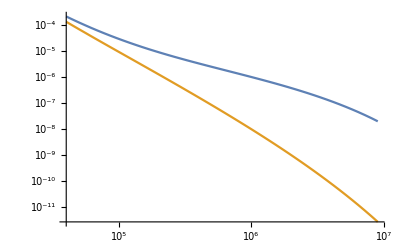
{-Graphics-,-Graphics-,-Graphics-}

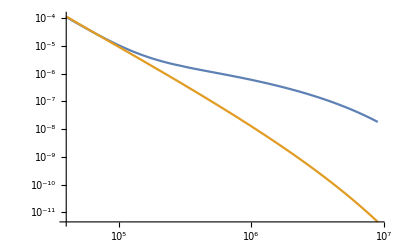
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{peν,pμν,pτν}
{pee,pμμ,pττ}
```

```mathematica
σDif=DifferentialCrossSection[{e[1],e[1]},Coefficients->{WC["lq1",{1,1,1,1}],WC["dW",{1,1}], WC["eW",{1,1}], WC["Hq1",{1,1}]}];
σ[a_,b_,c_,d_]:=σDif/.{WC["lq1",{1,1,1,1}]->a,WC["dW",{1,1}]->b,WC["eW",{1,1}]->c,WC["Hq1",{1,1}]->d};
LogLogPlot[{σ[0,0,0,0][s],σ[1,0,0,0][s],σ[0,1,0,0][s],σ[0,0,1,0][s],σ[0,0,0,1][s]},{s,20^2,10000^2}]
LogLogPlot[{σ[0,0,0,0][s],σ[3,3,3,3][s]},{s,50^2,200^2}]
```

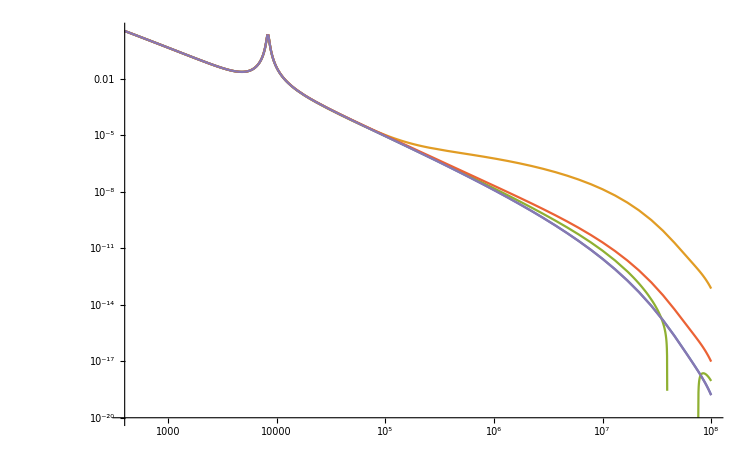

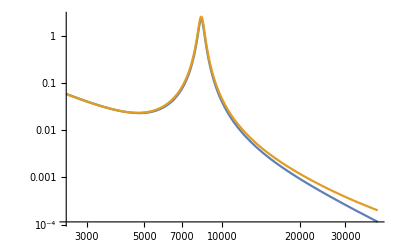

#### Yields [issue with dbar luminosities at 6 TeV]

```mathematica
nμν=EventYield["mono-muon-ATLAS",SM->True,Coefficients->{WC["lq3",{2,2,1,1}]}];
bμν=LHCSearch["mono-muon-ATLAS"]["INFO"]["BINS"]["OBSERVABLE"]
Nμν[Clq3_]:=Table[{bμν[[i]],nμν[[i]]/.{WC["lq3",{2,2,1,1}]-> Clq3}//Chop},{i,Length[nμν]}]
```

PROCESS | : | pp → μ^-ν̄
pp → νμ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:1906.05609](https://arxiv.org/abs/1906.05609)
SOURCE | : | [hepdata: Table 2](https://doi.org/10.17182/hepdata.90193.v1/t2)
OBSERVABLE | : | m_T
BINNING m_T [GeV] | : | {214.564,233.253,253.57,275.657,299.667,325.769,354.144,384.991,418.524,454.979,494.609,537.69,584.525,635.438,690.786,750.956,816.366,887.473,964.775,1048.81,1140.16,1239.47,1347.44,1464.8,1592.39,1731.09,1881.87,2045.79,2223.98,2417.69,2628.28,2857.21,3106.08,3376.63,3670.74,3990.47,4338.05,4715.91,5126.68,5573.22,6058.67,6586.39,7160.08,7783.74,8461.73,9198.76,10000}
EVENTS OBSERVED | : | {119462, 83461, 59443, 42137, 30145, 21500, 15241, 10752, 7843, 5457, 4013, 2761, 2050, 1401, 1056, 673, 531, 339, 237, 150, 105, 96, 53, 36, 29, 18, 9, 5, 8, 3, 2, 1, 0, 1, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {400,10000}
BINNING p_T [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}

{214.564,233.253,253.57,275.657,299.667,325.769,354.144,384.991,418.524,454.979,494.609,537.69,584.525,635.438,690.786,750.956,816.366,887.473,964.775,1048.81,1140.16,1239.47,1347.44,1464.8,1592.39,1731.09,1881.87,2045.79,2223.98,2417.69,2628.28,2857.21,3106.08,3376.63,3670.74,3990.47,4338.05,4715.91,5126.68,5573.22,6058.67,6586.39,7160.08,7783.74,8461.73,9198.76,10000}

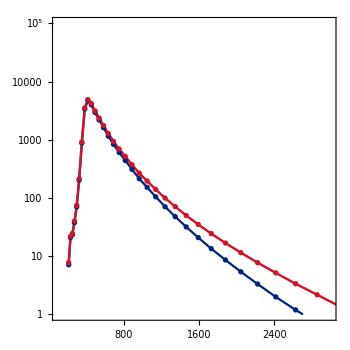

```mathematica
ListLogPlot[{Nμν[0],Nμν[0.01]},Joined->True,PlotStyle->{azul,{rojo,Thickness[0.005]}},
PlotRange->{{100,3000},{1,100000}}, Frame->True, AspectRatio->1,Joined->True,Mesh->All,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{T}\\ \\rm[GeV]",Magnification->1.75],MaTeX["{\\rm d}\\sigma/{\\rm d}m_T",Magnification->1.75]}]
```

```mathematica
nμμ=EventYield["di-muon-CMS",SM->True,Coefficients->{WC["lq1",{2,2,1,1}],WC["lq3",{2,2,1,1}]}];
bμμ=LHCSearch["di-muon-CMS"]["INFO"]["BINS"]["OBSERVABLE"]
Nμμ[Clq1_,Clq3_]:=Table[{bμμ[[i]],nμμ[[i]]/.{WC["lq1",{2,2,1,1}]-> Clq1,WC["lq3",{2,2,1,1}]-> Clq3}//Chop},{i,Length[nμμ]}]
```

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}

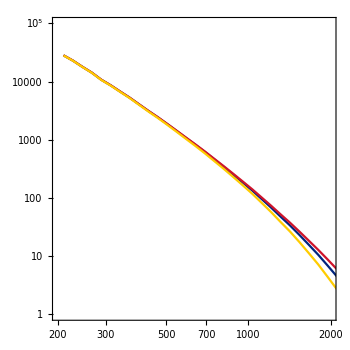

```mathematica
ListLogLogPlot[{Nμμ[0,0],Nμμ[-0.01,0.0],Nμμ[0,-0.01]},Joined->True,PlotStyle->{azul,rojo,amarillo},
PlotRange->{{200,2000},{1,100000}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["{\\rm d}\\sigma/{\\rm d}m_{\ell\ell}",Magnification->1.75]}]
```

```mathematica
σDif=DifferentialCrossSection[{e[2],e[2]},Coefficients->{WC["lq1",{2,2,1,1}],WC["lq3",{2,2,1,1}]}];
σNP=σDif/.{WC["lq1",{2,2,1,1}]->0.1,WC["lq3",{2,2,1,1}]->0};
σSM=σDif/.WC["lq1",{2,2,1,1}]->0;
```

## Dielectrons

```mathematica
(*-------------------------  Run for this section ---------------------*)
Λ=1000;
{α,β}={1,1};
SEARCH="di-electron-CMS";
LUMINOSITY=141;
DefaultBins[SEARCH]={200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1680,1820,1970,2210,6070};
{bmin,bmax}={5,Length[DefaultBins[SEARCH]]-1}; 
(*--------------------------------------------------------------------*)

LHCSearch[SEARCH]
LHCSearch[SEARCH]["INFO"]["BINS"]["OBSERVABLE"]
```

#### [C_lq^1]_αα11 Clipping

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-2

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Clq1 {1, 1, 1, 1}, bin={280,300}, limits={-0.525549,0.778046}, {χ_min, best fit}={0.0566811,{C6→0.126249}}

coeff = Clq1 {1, 1, 1, 1}, bin={300,320}, limits={-0.460862,0.618834}, {χ_min, best fit}={0.121003,{C6→0.0789863}}

coeff = Clq1 {1, 1, 1, 1}, bin={320,340}, limits={-0.365724,0.526368}, {χ_min, best fit}={0.121077,{C6→0.0803222}}

coeff = Clq1 {1, 1, 1, 1}, bin={340,360}, limits={-0.316422,0.417935}, {χ_min, best fit}={0.173433,{C6→0.0507567}}

coeff = Clq1 {1, 1, 1, 1}, bin={360,380}, limits={-0.252012,0.383543}, {χ_min, best fit}={0.199007,{C6→0.0657657}}

coeff = Clq1 {1, 1, 1, 1}, bin={380,400}, limits={-0.170812,0.3602}, {χ_min, best fit}={0.304442,{C6→0.0946935}}

coeff = Clq1 {1, 1, 1, 1}, bin={400,420}, limits={-0.150658,0.326431}, {χ_min, best fit}={0.317539,{C6→0.0878865}}

coeff = Clq1 {1, 1, 1, 1}, bin={420,440}, limits={-0.146954,0.266375}, {χ_min, best fit}={0.532409,{C6→0.0597102}}

coeff = Clq1 {1, 1, 1, 1}, bin={440,460}, limits={-0.144839,0.218153}, {χ_min, best fit}={0.741385,{C6→0.0366568}}

coeff = Clq1 {1, 1, 1, 1}, bin={460,480}, limits={-0.0900221,0.224293}, {χ_min, best fit}={1.17433,{C6→0.0671353}}

coeff = Clq1 {1, 1, 1, 1}, bin={480,500}, limits={-0.0560412,0.222926}, {χ_min, best fit}={1.36918,{C6→0.0834426}}

coeff = Clq1 {1, 1, 1, 1}, bin={500,520}, limits={-0.0469489,0.211548}, {χ_min, best fit}={1.37101,{C6→0.0822994}}

coeff = Clq1 {1, 1, 1, 1}, bin={520,540}, limits={-0.0457005,0.188522}, {χ_min, best fit}={1.52333,{C6→0.0714108}}

coeff = Clq1 {1, 1, 1, 1}, bin={540,560}, limits={-0.0342135,0.179327}, {χ_min, best fit}={1.52551,{C6→0.0725568}}

coeff = Clq1 {1, 1, 1, 1}, bin={560,580}, limits={-0.041065,0.154446}, {χ_min, best fit}={2.05,{C6→0.0566906}}

coeff = Clq1 {1, 1, 1, 1}, bin={580,600}, limits={-0.0505374,0.130451}, {χ_min, best fit}={2.83693,{C6→0.039957}}

coeff = Clq1 {1, 1, 1, 1}, bin={600,630}, limits={-0.053067,0.117434}, {χ_min, best fit}={3.08881,{C6→0.0321835}}

coeff = Clq1 {1, 1, 1, 1}, bin={630,660}, limits={-0.0548026,0.0995492}, {χ_min, best fit}={3.3707,{C6→0.0223733}}

coeff = Clq1 {1, 1, 1, 1}, bin={660,690}, limits={-0.0526235,0.0894893}, {χ_min, best fit}={3.43645,{C6→0.0184329}}

coeff = Clq1 {1, 1, 1, 1}, bin={690,720}, limits={-0.0582035,0.0737349}, {χ_min, best fit}={4.06352,{C6→0.00776568}}

coeff = Clq1 {1, 1, 1, 1}, bin={720,750}, limits={-0.0733943,0.0492711}, {χ_min, best fit}={6.62208,{C6→-0.0120616}}

coeff = Clq1 {1, 1, 1, 1}, bin={750,780}, limits={-0.0868265,0.0281569}, {χ_min, best fit}={9.13339,{C6→-0.0293348}}

coeff = Clq1 {1, 1, 1, 1}, bin={780,810}, limits={-0.0634578,0.0451649}, {χ_min, best fit}={13.5366,{C6→-0.00914644}}

coeff = Clq1 {1, 1, 1, 1}, bin={810,840}, limits={-0.0674098,0.0371325}, {χ_min, best fit}={14.171,{C6→-0.0151386}}

coeff = Clq1 {1, 1, 1, 1}, bin={840,870}, limits={-0.0595772,0.0379269}, {χ_min, best fit}={14.372,{C6→-0.0108252}}

coeff = Clq1 {1, 1, 1, 1}, bin={870,900}, limits={-0.0491903,0.0424254}, {χ_min, best fit}={15.1363,{C6→-0.00338244}}

coeff = Clq1 {1, 1, 1, 1}, bin={900,950}, limits={-0.0450229,0.0413917}, {χ_min, best fit}={15.1771,{C6→-0.00181561}}

coeff = Clq1 {1, 1, 1, 1}, bin={950,1000}, limits={-0.0513033,0.029619}, {χ_min, best fit}={16.5394,{C6→-0.0108422}}

coeff = Clq1 {1, 1, 1, 1}, bin={1000,1050}, limits={-0.0345084,0.0406756}, {χ_min, best fit}={19.8659,{C6→0.00308358}}

coeff = Clq1 {1, 1, 1, 1}, bin={1050,1100}, limits={-0.0316776,0.0391859}, {χ_min, best fit}={19.8768,{C6→0.00375419}}

coeff = Clq1 {1, 1, 1, 1}, bin={1100,1150}, limits={-0.0374162,0.0304128}, {χ_min, best fit}={21.799,{C6→-0.00350168}}

coeff = Clq1 {1, 1, 1, 1}, bin={1150,1200}, limits={-0.0335435,0.0311069}, {χ_min, best fit}={21.9893,{C6→-0.00121829}}

coeff = Clq1 {1, 1, 1, 1}, bin={1200,1250}, limits={-0.0318432,0.0300108}, {χ_min, best fit}={21.9932,{C6→-0.000916228}}

coeff = Clq1 {1, 1, 1, 1}, bin={1250,1310}, limits={-0.0325734,0.0268336}, {χ_min, best fit}={22.1909,{C6→-0.00286992}}

coeff = Clq1 {1, 1, 1, 1}, bin={1310,1370}, limits={-0.0321517,0.0249315}, {χ_min, best fit}={22.222,{C6→-0.00361012}}

coeff = Clq1 {1, 1, 1, 1}, bin={1370,1430}, limits={-0.028266,0.0262302}, {χ_min, best fit}={22.5797,{C6→-0.00101788}}

coeff = Clq1 {1, 1, 1, 1}, bin={1430,1490}, limits={-0.0309618,0.0220786}, {χ_min, best fit}={23.7302,{C6→-0.00444162}}

coeff = Clq1 {1, 1, 1, 1}, bin={1490,1550}, limits={-0.0298461,0.0215473}, {χ_min, best fit}={23.7378,{C6→-0.00414938}}

coeff = Clq1 {1, 1, 1, 1}, bin={1550,1680}, limits={-0.027591,0.0207909}, {χ_min, best fit}={23.7665,{C6→-0.00340006}}

coeff = Clq1 {1, 1, 1, 1}, bin={1680,1820}, limits={-0.0275038,0.0185604}, {χ_min, best fit}={23.8471,{C6→-0.00447169}}

coeff = Clq1 {1, 1, 1, 1}, bin={1820,1970}, limits={-0.0307048,0.0139029}, {χ_min, best fit}={25.6435,{C6→-0.00840096}}

coeff = Clq1 {1, 1, 1, 1}, bin={1970,2210}, limits={-0.0320124,0.0105667}, {χ_min, best fit}={26.1119,{C6→-0.0107228}}

coeff = Clq1 {1, 1, 1, 1}, bin={2210,6070}, limits={-0.033651,0.00422888}, {χ_min, best fit}={26.7583,{C6→-0.014711}}

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Clq1 {1, 1, 1, 1}, bin={280,300}, limits={-0.339947,0.952865}, {χ_min, best fit}={0.0305924,{C6→0.451397}}

coeff = Clq1 {1, 1, 1, 1}, bin={300,320}, limits={-0.301376,0.873404}, {χ_min, best fit}={0.03955,{C6→0.491559}}

coeff = Clq1 {1, 1, 1, 1}, bin={320,340}, limits={-0.248955,0.771698}, {χ_min, best fit}={0.0808112,{C6→0.428046}}

coeff = Clq1 {1, 1, 1, 1}, bin={340,360}, limits={-0.217481,0.696998}, {χ_min, best fit}={0.0808363,{C6→0.426731}}

coeff = Clq1 {1, 1, 1, 1}, bin={360,380}, limits={-0.18115,0.626076}, {χ_min, best fit}={0.194351,{C6→0.0830519}}

coeff = Clq1 {1, 1, 1, 1}, bin={380,400}, limits={-0.130865,0.539336}, {χ_min, best fit}={0.314744,{C6→0.129758}}

coeff = Clq1 {1, 1, 1, 1}, bin={400,420}, limits={-0.116712,0.497625}, {χ_min, best fit}={0.318409,{C6→0.125946}}

coeff = Clq1 {1, 1, 1, 1}, bin={420,440}, limits={-0.111019,0.460203}, {χ_min, best fit}={0.414301,{C6→0.275475}}

coeff = Clq1 {1, 1, 1, 1}, bin={440,460}, limits={-0.106313,0.438712}, {χ_min, best fit}={0.444172,{C6→0.293539}}

coeff = Clq1 {1, 1, 1, 1}, bin={460,480}, limits={-0.0730466,0.368186}, {χ_min, best fit}={1.17001,{C6→0.0962541}}

coeff = Clq1 {1, 1, 1, 1}, bin={480,500}, limits={-0.0495058,0.316888}, {χ_min, best fit}={1.48222,{C6→0.108577}}

coeff = Clq1 {1, 1, 1, 1}, bin={500,520}, limits={-0.0424612,0.299471}, {χ_min, best fit}={1.49505,{C6→0.108853}}

coeff = Clq1 {1, 1, 1, 1}, bin={520,540}, limits={-0.0398853,0.285043}, {χ_min, best fit}={1.53588,{C6→0.111956}}

coeff = Clq1 {1, 1, 1, 1}, bin={540,560}, limits={-0.0312155,0.260104}, {χ_min, best fit}={1.59308,{C6→0.106297}}

coeff = Clq1 {1, 1, 1, 1}, bin={560,580}, limits={-0.0343934,0.259747}, {χ_min, best fit}={1.90531,{C6→0.137561}}

coeff = Clq1 {1, 1, 1, 1}, bin={580,600}, limits={-0.0374915,0.259434}, {χ_min, best fit}={2.23577,{C6→0.174284}}

coeff = Clq1 {1, 1, 1, 1}, bin={600,630}, limits={-0.0374001,0.252353}, {χ_min, best fit}={2.24367,{C6→0.177321}}

coeff = Clq1 {1, 1, 1, 1}, bin={630,660}, limits={-0.0369274,0.236086}, {χ_min, best fit}={2.26195,{C6→0.172301}}

coeff = Clq1 {1, 1, 1, 1}, bin={660,690}, limits={-0.0361488,0.221273}, {χ_min, best fit}={2.38106,{C6→0.162742}}

coeff = Clq1 {1, 1, 1, 1}, bin={690,720}, limits={-0.0361933,0.215733}, {χ_min, best fit}={2.40574,{C6→0.166216}}

coeff = Clq1 {1, 1, 1, 1}, bin={720,750}, limits={-0.027322,0.218222}, {χ_min, best fit}={3.02874,{C6→0.178958}}

coeff = Clq1 {1, 1, 1, 1}, bin={750,780}, limits={0.138013,0.217564}, {χ_min, best fit}={3.25372,{C6→0.184697}}

coeff = Clq1 {1, 1, 1, 1}, bin={780,810}, limits={-0.0462499,0.186473}, {χ_min, best fit}={12.8585,{C6→0.147926}}

coeff = Clq1 {1, 1, 1, 1}, bin={810,840}, limits={-0.0460205,0.183235}, {χ_min, best fit}={12.8609,{C6→0.148492}}

coeff = Clq1 {1, 1, 1, 1}, bin={840,870}, limits={-0.045739,0.167052}, {χ_min, best fit}={14.3534,{C6→-0.0109066}}

coeff = Clq1 {1, 1, 1, 1}, bin={870,900}, limits={-0.0381098,0.142389}, {χ_min, best fit}={15.1355,{C6→-0.00342104}}

coeff = Clq1 {1, 1, 1, 1}, bin={900,950}, limits={-0.0348957,0.128625}, {χ_min, best fit}={15.1769,{C6→-0.00182872}}

coeff = Clq1 {1, 1, 1, 1}, bin={950,1000}, limits={-0.0389488,0.133923}, {χ_min, best fit}={16.5151,{C6→-0.0106683}}

coeff = Clq1 {1, 1, 1, 1}, bin={1000,1050}, limits={-0.026766,0.0917941}, {χ_min, best fit}={19.8674,{C6→0.00298276}}

coeff = Clq1 {1, 1, 1, 1}, bin={1050,1100}, limits={-0.0246867,0.0865778}, {χ_min, best fit}={19.8795,{C6→0.00365816}}

coeff = Clq1 {1, 1, 1, 1}, bin={1100,1150}, limits={-0.028626,0.0973302}, {χ_min, best fit}={21.7973,{C6→-0.0035009}}

coeff = Clq1 {1, 1, 1, 1}, bin={1150,1200}, limits={-0.0256626,0.0852891}, {χ_min, best fit}={21.9892,{C6→-0.00120784}}

coeff = Clq1 {1, 1, 1, 1}, bin={1200,1250}, limits={-0.0243181,0.0798842}, {χ_min, best fit}={21.9932,{C6→-0.000906809}}

coeff = Clq1 {1, 1, 1, 1}, bin={1250,1310}, limits={-0.0246907,0.0795126}, {χ_min, best fit}={22.1898,{C6→-0.00284666}}

coeff = Clq1 {1, 1, 1, 1}, bin={1310,1370}, limits={-0.0242013,0.0754439}, {χ_min, best fit}={22.2195,{C6→-0.0035715}}

coeff = Clq1 {1, 1, 1, 1}, bin={1370,1430}, limits={-0.0213236,0.0659985}, {χ_min, best fit}={22.5797,{C6→-0.000997415}}

coeff = Clq1 {1, 1, 1, 1}, bin={1430,1490}, limits={-0.023141,0.0705375}, {χ_min, best fit}={23.723,{C6→-0.00441327}}

coeff = Clq1 {1, 1, 1, 1}, bin={1490,1550}, limits={-0.0221734,0.0656168}, {χ_min, best fit}={23.7322,{C6→-0.00408974}}

coeff = Clq1 {1, 1, 1, 1}, bin={1550,1680}, limits={-0.0202449,0.0563404}, {χ_min, best fit}={23.7642,{C6→-0.0032976}}

coeff = Clq1 {1, 1, 1, 1}, bin={1680,1820}, limits={-0.0199102,0.0529375}, {χ_min, best fit}={23.8388,{C6→-0.00433249}}

coeff = Clq1 {1, 1, 1, 1}, bin={1820,1970}, limits={-0.0219814,0.0571772}, {χ_min, best fit}={25.5449,{C6→-0.00822335}}

coeff = Clq1 {1, 1, 1, 1}, bin={1970,2210}, limits={-0.0223181,0.0534354}, {χ_min, best fit}={25.8802,{C6→-0.0102136}}

coeff = Clq1 {1, 1, 1, 1}, bin={2210,6070}, limits={-0.020949,0.0382412}, {χ_min, best fit}={26.0638,{C6→-0.0123165}}

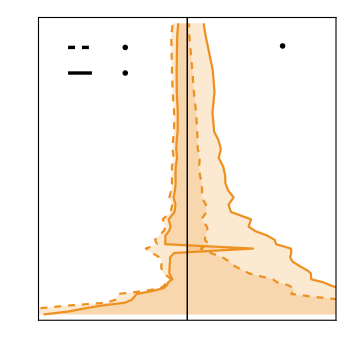

```mathematica
(*------------------*)
W="lq1";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)

(* linear *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;


(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(* Plots *)
plot[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13]},{RGBColor[0.93,0.57,0.13]}},
PlotRange->{{-0.3,0.3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog->{{Directive[{Thickness[0.003],Black}],Line[{{0,0},{0,3000}}],Directive[{Thickness[0.007],Black}],Line[{{-0.25,1950},{-0.20,1950}}],Directive[{Thickness[0.007],Black,Dashed}],Line[{{-0.25,2125},{-0.20,2125}}]}, 
                   Text[MaTeX["\\mathcal{O}(1/\\Lambda^2)",Magnification->1.2],{-0.13,2125},Center],
                   Text[MaTeX["\\mathcal{O}(1/\\Lambda^4)",Magnification->1.2],{-0.13,1950},Center],
                   Text[MaTeX["pp\\to ee",Magnification->1.4],{0.2,2135},Center]},
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{0.1,0.2,0.3},True,1.25],Xticks[{0.1,0.2,0.3},False]} },
FrameLabel->{MaTeX["[\\mathcal{C}_{lq}^{(1)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

#### [C_lq^1]_αα11 Jack-knife analysis

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}] (* set VCKM=1 *)
(*------------------*)
W="lq1";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)

{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]}=JacknifeEXPECTED["di-electron-CMS", 140,W,αβij,{{43,44},{45,46},{47,48},{49,50,51},{52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94}}];

(*----- Plots ------*)


(* positive WC *)
JackPlot[W,αβij]=ListLogLinearPlot[{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                                          UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed,Thickness[0.0065]},{RGBColor[0.93,0.57,0.13],Thickness[0.005]}},
PlotRange->{{200,6000},{0.99,1.55}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{ee}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lq}^{(1)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}>0",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to ee",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]


(* negative WC *)
ListLogLinearPlot[{LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                       LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed,Thickness[0.0065]},{RGBColor[0.93,0.57,0.13],Thickness[0.005]}},
PlotRange->{{200,6000},{0.99,1.55}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{ee}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lq}^{(1)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}<0",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to ee",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]
```

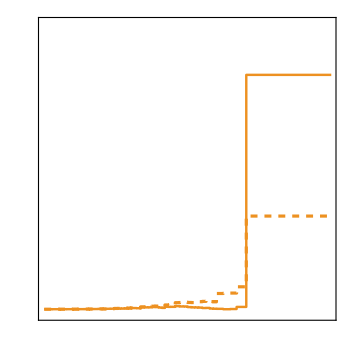
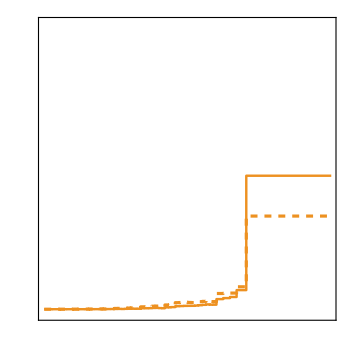

#### [C_lq^3]_αα11 Clipping

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-2

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Clq3 {1, 1, 1, 1}, bin={280,300}, limits={-0.156537,0.104973}, {χ_min, best fit}={0.0514522,{C6→-0.0257817}}

coeff = Clq3 {1, 1, 1, 1}, bin={300,320}, limits={-0.128199,0.0939439}, {χ_min, best fit}={0.111893,{C6→-0.0171277}}

coeff = Clq3 {1, 1, 1, 1}, bin={320,340}, limits={-0.112441,0.0771143}, {χ_min, best fit}={0.112221,{C6→-0.0176635}}

coeff = Clq3 {1, 1, 1, 1}, bin={340,360}, limits={-0.0918077,0.0681603}, {χ_min, best fit}={0.162892,{C6→-0.0118237}}

coeff = Clq3 {1, 1, 1, 1}, bin={360,380}, limits={-0.0861623,0.0561201}, {χ_min, best fit}={0.192278,{C6→-0.0150211}}

coeff = Clq3 {1, 1, 1, 1}, bin={380,400}, limits={-0.0833372,0.0401951}, {χ_min, best fit}={0.324548,{C6→-0.0215711}}

coeff = Clq3 {1, 1, 1, 1}, bin={400,420}, limits={-0.0764471,0.0357346}, {χ_min, best fit}={0.333024,{C6→-0.0203562}}

coeff = Clq3 {1, 1, 1, 1}, bin={420,440}, limits={-0.0634183,0.0349679}, {χ_min, best fit}={0.531858,{C6→-0.0142252}}

coeff = Clq3 {1, 1, 1, 1}, bin={440,460}, limits={-0.0533343,0.0347663}, {χ_min, best fit}={0.727452,{C6→-0.00928398}}

coeff = Clq3 {1, 1, 1, 1}, bin={460,480}, limits={-0.0554253,0.0225818}, {χ_min, best fit}={1.19438,{C6→-0.0164218}}

coeff = Clq3 {1, 1, 1, 1}, bin={480,500}, limits={-0.0557096,0.0145504}, {χ_min, best fit}={1.42564,{C6→-0.0205796}}

coeff = Clq3 {1, 1, 1, 1}, bin={500,520}, limits={-0.053408,0.0123054}, {χ_min, best fit}={1.42566,{C6→-0.0205513}}

coeff = Clq3 {1, 1, 1, 1}, bin={520,540}, limits={-0.0480875,0.0119181}, {χ_min, best fit}={1.55595,{C6→-0.0180847}}

coeff = Clq3 {1, 1, 1, 1}, bin={540,560}, limits={-0.0460872,0.00901983}, {χ_min, best fit}={1.56144,{C6→-0.0185337}}

coeff = Clq3 {1, 1, 1, 1}, bin={560,580}, limits={-0.0406255,0.0105921}, {χ_min, best fit}={2.02103,{C6→-0.0150167}}

coeff = Clq3 {1, 1, 1, 1}, bin={580,600}, limits={-0.0349005,0.0129637}, {χ_min, best fit}={2.77896,{C6→-0.0109684}}

coeff = Clq3 {1, 1, 1, 1}, bin={600,630}, limits={-0.0318049,0.0136512}, {χ_min, best fit}={3.0236,{C6→-0.00907687}}

coeff = Clq3 {1, 1, 1, 1}, bin={630,660}, limits={-0.0276157,0.0142282}, {χ_min, best fit}={3.30032,{C6→-0.00669377}}

coeff = Clq3 {1, 1, 1, 1}, bin={660,690}, limits={-0.0250737,0.0137974}, {χ_min, best fit}={3.37168,{C6→-0.00563817}}

coeff = Clq3 {1, 1, 1, 1}, bin={690,720}, limits={-0.0211671,0.0153553}, {χ_min, best fit}={4.01948,{C6→-0.00290592}}

coeff = Clq3 {1, 1, 1, 1}, bin={720,750}, limits={-0.0150468,0.0193974}, {χ_min, best fit}={6.70936,{C6→0.00217528}}

coeff = Clq3 {1, 1, 1, 1}, bin={750,780}, limits={-0.00948785,0.0231511}, {χ_min, best fit}={9.46033,{C6→0.00683161}}

coeff = Clq3 {1, 1, 1, 1}, bin={780,810}, limits={-0.0139235,0.0171213}, {χ_min, best fit}={13.6048,{C6→0.00159891}}

coeff = Clq3 {1, 1, 1, 1}, bin={810,840}, limits={-0.0116995,0.0183048}, {χ_min, best fit}={14.307,{C6→0.00330266}}

coeff = Clq3 {1, 1, 1, 1}, bin={840,870}, limits={-0.0118478,0.0165228}, {χ_min, best fit}={14.4571,{C6→0.00233749}}

coeff = Clq3 {1, 1, 1, 1}, bin={870,900}, limits={-0.013028,0.0138977}, {χ_min, best fit}={15.1533,{C6→0.000434863}}

coeff = Clq3 {1, 1, 1, 1}, bin={900,950}, limits={-0.0127386,0.0128661}, {χ_min, best fit}={15.1838,{C6→0.0000637827}}

coeff = Clq3 {1, 1, 1, 1}, bin={950,1000}, limits={-0.0095701,0.0147092}, {χ_min, best fit}={16.6431,{C6→0.00256956}}

coeff = Clq3 {1, 1, 1, 1}, bin={1000,1050}, limits={-0.0126067,0.0102415}, {χ_min, best fit}={19.8506,{C6→-0.00118258}}

coeff = Clq3 {1, 1, 1, 1}, bin={1050,1100}, limits={-0.0122668,0.00955498}, {χ_min, best fit}={19.8606,{C6→-0.00135591}}

coeff = Clq3 {1, 1, 1, 1}, bin={1100,1150}, limits={-0.00981014,0.0112313}, {χ_min, best fit}={21.8224,{C6→0.00071058}}

coeff = Clq3 {1, 1, 1, 1}, bin={1150,1200}, limits={-0.0100149,0.0102024}, {χ_min, best fit}={21.9944,{C6→0.000093727}}

coeff = Clq3 {1, 1, 1, 1}, bin={1200,1250}, limits={-0.00973602,0.00979984}, {χ_min, best fit}={21.9966,{C6→0.0000319118}}

coeff = Clq3 {1, 1, 1, 1}, bin={1250,1310}, limits={-0.0088752,0.0100683}, {χ_min, best fit}={22.2115,{C6→0.000596566}}

coeff = Clq3 {1, 1, 1, 1}, bin={1310,1370}, limits={-0.00834536,0.0100153}, {χ_min, best fit}={22.2517,{C6→0.000834959}}

coeff = Clq3 {1, 1, 1, 1}, bin={1370,1430}, limits={-0.00873024,0.00902626}, {χ_min, best fit}={22.584,{C6→0.000148005}}

coeff = Clq3 {1, 1, 1, 1}, bin={1430,1490}, limits={-0.0075381,0.00984555}, {χ_min, best fit}={23.7702,{C6→0.00115372}}

coeff = Clq3 {1, 1, 1, 1}, bin={1490,1550}, limits={-0.00738955,0.00957504}, {χ_min, best fit}={23.7742,{C6→0.00109274}}

coeff = Clq3 {1, 1, 1, 1}, bin={1550,1680}, limits={-0.00718383,0.00901187}, {χ_min, best fit}={23.7934,{C6→0.000914021}}

coeff = Clq3 {1, 1, 1, 1}, bin={1680,1820}, limits={-0.0065519,0.00906708}, {χ_min, best fit}={23.8923,{C6→0.00125759}}

coeff = Clq3 {1, 1, 1, 1}, bin={1820,1970}, limits={-0.00522086,0.0100499}, {χ_min, best fit}={25.8044,{C6→0.00241452}}

coeff = Clq3 {1, 1, 1, 1}, bin={1970,2210}, limits={-0.00424207,0.0105498}, {χ_min, best fit}={26.3878,{C6→0.00315388}}

coeff = Clq3 {1, 1, 1, 1}, bin={2210,6070}, limits={-0.002446,0.0114446}, {χ_min, best fit}={27.4637,{C6→0.00449928}}

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Clq3 {1, 1, 1, 1}, bin={280,300}, limits={-0.165404,0.101713}, {χ_min, best fit}={0.0512558,{C6→-0.0260325}}

coeff = Clq3 {1, 1, 1, 1}, bin={300,320}, limits={-0.134787,0.0911036}, {χ_min, best fit}={0.11167,{C6→-0.0172748}}

coeff = Clq3 {1, 1, 1, 1}, bin={320,340}, limits={-0.118024,0.0749511}, {χ_min, best fit}={0.112,{C6→-0.0178177}}

coeff = Clq3 {1, 1, 1, 1}, bin={340,360}, limits={-0.0959985,0.0662926}, {χ_min, best fit}={0.162678,{C6→-0.0119165}}

coeff = Clq3 {1, 1, 1, 1}, bin={360,380}, limits={-0.0901058,0.0547044}, {χ_min, best fit}={0.192099,{C6→-0.0151469}}

coeff = Clq3 {1, 1, 1, 1}, bin={380,400}, limits={-0.0873097,0.0393579}, {χ_min, best fit}={0.325199,{C6→-0.0217935}}

coeff = Clq3 {1, 1, 1, 1}, bin={400,420}, limits={-0.0800999,0.0350234}, {χ_min, best fit}={0.33335,{C6→-0.0205868}}

coeff = Clq3 {1, 1, 1, 1}, bin={420,440}, limits={-0.0663608,0.0342334}, {χ_min, best fit}={0.531071,{C6→-0.0143943}}

coeff = Clq3 {1, 1, 1, 1}, bin={440,460}, limits={-0.0556535,0.0340031}, {χ_min, best fit}={0.726719,{C6→-0.00938607}}

coeff = Clq3 {1, 1, 1, 1}, bin={460,480}, limits={-0.0580111,0.0221986}, {χ_min, best fit}={1.19466,{C6→-0.016629}}

coeff = Clq3 {1, 1, 1, 1}, bin={480,500}, limits={-0.0584677,0.014385}, {χ_min, best fit}={1.42949,{C6→-0.0208863}}

coeff = Clq3 {1, 1, 1, 1}, bin={500,520}, limits={-0.0561022,0.012184}, {χ_min, best fit}={1.42949,{C6→-0.0208861}}

coeff = Clq3 {1, 1, 1, 1}, bin={520,540}, limits={-0.0505245,0.0117855}, {χ_min, best fit}={1.55638,{C6→-0.0184043}}

coeff = Clq3 {1, 1, 1, 1}, bin={540,560}, limits={-0.0484836,0.00894039}, {χ_min, best fit}={1.56252,{C6→-0.0188895}}

coeff = Clq3 {1, 1, 1, 1}, bin={560,580}, limits={-0.0426956,0.010466}, {χ_min, best fit}={2.01772,{C6→-0.015312}}

coeff = Clq3 {1, 1, 1, 1}, bin={580,600}, limits={-0.0366112,0.012778}, {χ_min, best fit}={2.77399,{C6→-0.0111826}}

coeff = Clq3 {1, 1, 1, 1}, bin={600,630}, limits={-0.0333336,0.013445}, {χ_min, best fit}={3.01887,{C6→-0.00925276}}

coeff = Clq3 {1, 1, 1, 1}, bin={630,660}, limits={-0.028921,0.0139979}, {χ_min, best fit}={3.29645,{C6→-0.00682305}}

coeff = Clq3 {1, 1, 1, 1}, bin={660,690}, limits={-0.0262307,0.0135675}, {χ_min, best fit}={3.36849,{C6→-0.0057421}}

coeff = Clq3 {1, 1, 1, 1}, bin={690,720}, limits={-0.0220885,0.0150777}, {χ_min, best fit}={4.01821,{C6→-0.00295734}}

coeff = Clq3 {1, 1, 1, 1}, bin={720,750}, limits={-0.0155885,0.0190032}, {χ_min, best fit}={6.70811,{C6→0.00221134}}

coeff = Clq3 {1, 1, 1, 1}, bin={750,780}, limits={-0.00969393,0.0226245}, {χ_min, best fit}={9.44189,{C6→0.00693101}}

coeff = Clq3 {1, 1, 1, 1}, bin={780,810}, limits={-0.0144035,0.0167139}, {χ_min, best fit}={13.6043,{C6→0.00161581}}

coeff = Clq3 {1, 1, 1, 1}, bin={810,840}, limits={-0.0120623,0.0178469}, {χ_min, best fit}={14.3038,{C6→0.00333652}}

coeff = Clq3 {1, 1, 1, 1}, bin={840,870}, limits={-0.0122296,0.0160845}, {χ_min, best fit}={14.4558,{C6→0.00235535}}

coeff = Clq3 {1, 1, 1, 1}, bin={870,900}, limits={-0.0134827,0.0135222}, {χ_min, best fit}={15.1533,{C6→0.000437131}}

coeff = Clq3 {1, 1, 1, 1}, bin={900,950}, limits={-0.0131926,0.01251}, {χ_min, best fit}={15.1838,{C6→0.0000640572}}

coeff = Clq3 {1, 1, 1, 1}, bin={950,1000}, limits={-0.00987604,0.0142734}, {χ_min, best fit}={16.6409,{C6→0.00258498}}

coeff = Clq3 {1, 1, 1, 1}, bin={1000,1050}, limits={-0.0130711,0.00993507}, {χ_min, best fit}={19.8508,{C6→-0.00118161}}

coeff = Clq3 {1, 1, 1, 1}, bin={1050,1100}, limits={-0.0127382,0.00926755}, {χ_min, best fit}={19.8609,{C6→-0.00135532}}

coeff = Clq3 {1, 1, 1, 1}, bin={1100,1150}, limits={-0.0101884,0.0108736}, {χ_min, best fit}={21.8223,{C6→0.000713727}}

coeff = Clq3 {1, 1, 1, 1}, bin={1150,1200}, limits={-0.0104157,0.00986614}, {χ_min, best fit}={21.9944,{C6→0.0000939515}}

coeff = Clq3 {1, 1, 1, 1}, bin={1200,1250}, limits={-0.0101363,0.00946723}, {χ_min, best fit}={21.9966,{C6→0.0000319762}}

coeff = Clq3 {1, 1, 1, 1}, bin={1250,1310}, limits={-0.00924618,0.00971579}, {χ_min, best fit}={22.2114,{C6→0.000598772}}

coeff = Clq3 {1, 1, 1, 1}, bin={1310,1370}, limits={-0.00870201,0.00965056}, {χ_min, best fit}={22.2514,{C6→0.000838408}}

coeff = Clq3 {1, 1, 1, 1}, bin={1370,1430}, limits={-0.00911734,0.0086816}, {χ_min, best fit}={22.584,{C6→0.000148085}}

coeff = Clq3 {1, 1, 1, 1}, bin={1430,1490}, limits={-0.00787604,0.00946648}, {χ_min, best fit}={23.7695,{C6→0.00116021}}

coeff = Clq3 {1, 1, 1, 1}, bin={1490,1550}, limits={-0.00772796,0.00918964}, {χ_min, best fit}={23.7735,{C6→0.00109756}}

coeff = Clq3 {1, 1, 1, 1}, bin={1550,1680}, limits={-0.00753011,0.00861501}, {χ_min, best fit}={23.7931,{C6→0.000915539}}

coeff = Clq3 {1, 1, 1, 1}, bin={1680,1820}, limits={-0.0068844,0.00864511}, {χ_min, best fit}={23.8911,{C6→0.00126234}}

coeff = Clq3 {1, 1, 1, 1}, bin={1820,1970}, limits={-0.00547755,0.00960646}, {χ_min, best fit}={25.7912,{C6→0.00245498}}

coeff = Clq3 {1, 1, 1, 1}, bin={1970,2210}, limits={-0.00442329,0.0100681}, {χ_min, best fit}={26.3525,{C6→0.00322929}}

coeff = Clq3 {1, 1, 1, 1}, bin={2210,6070}, limits={-0.00239566,0.0108143}, {χ_min, best fit}={27.2906,{C6→0.00470761}}

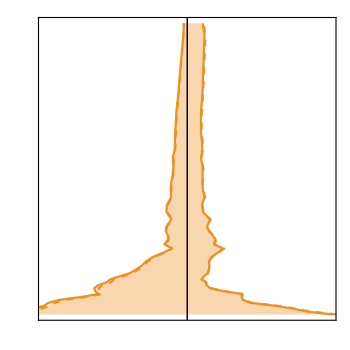

```mathematica
(*------------------*)
W="lq3";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)

(* linear *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(* quartic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(*----- Plots ------*)

plot[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13]},{RGBColor[0.93,0.57,0.13]}},
PlotRange->{{-0.09,0.09},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog->{{Directive[{Thickness[0.003],Black}],Line[{{0,0},{0,3000}}],Directive[{Thickness[0.007],Black}],Line[{{-0.25,1950},{-0.20,1950}}],Directive[{Thickness[0.007],Black,Dashed}],Line[{{-0.25,2125},{-0.20,2125}}]}, 
                   Text[MaTeX["\\mathcal{O}(1/\\Lambda^2)",Magnification->1.2],{-0.13,2125},Center],
                   Text[MaTeX["\\mathcal{O}(1/\\Lambda^4)",Magnification->1.2],{-0.13,1950},Center],
                   Text[MaTeX["pp\\to ee",Magnification->1.4],{0.2,2135},Center]},
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{0.03,0.06,0.09},True,1.25],Xticks[{0.03,0.06,0.09},False]} },
FrameLabel->{MaTeX["[\\mathcal{C}_{lq}^{(3)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

#### [C_lq^3]_αα11 Jack-knife analysis

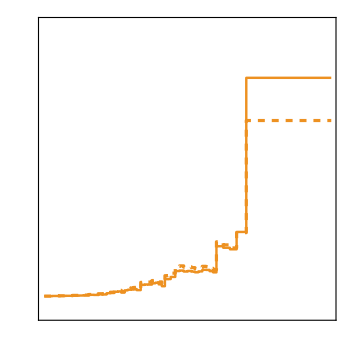

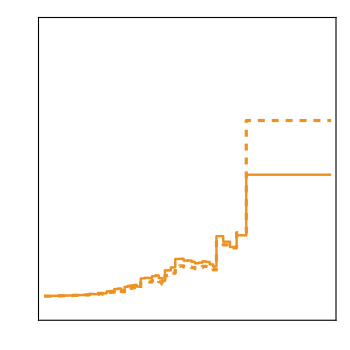

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}]

(*------------------*)
W="lq3";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)

{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]}=JacknifeEXPECTED["di-electron-CMS", 140,W,αβij,{{43,44},{45,46},{47,48},{49,50,51},{52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94}}];

(*----- Plots ------*)

(* positive WC *)
JackPlot[W,αβij]=ListLogLinearPlot[{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                                                             UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed,Thickness[0.0065]},{RGBColor[0.93,0.57,0.13],Thickness[0.005]}},
PlotRange->{{200,6000},{0.99,1.15}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{ee}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks2[ True,1.25],Xticks2[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lq}^{(1)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}>0",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to ee",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]


(* negative WC *)
ListLogLinearPlot[{LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                       LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed,Thickness[0.0065]},{RGBColor[0.93,0.57,0.13],Thickness[0.005]}},
PlotRange->{{200,6000},{0.99,1.15}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{ee}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks2[ True,1.25],Xticks2[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lq}^{(1)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}<0",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to ee",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]
```

## Dimuons

```mathematica
(*---------------------- Run for this section -------------------------*)
Λ=1000;
{α,β}={2,2};
SEARCH="di-muon-CMS";
LUMINOSITY=141;
{bmin,bmax}={5,Length[DefaultBins[SEARCH]]-1}
(*--------------------------------------------------------------------*)

LHCSearch[SEARCH]
DefaultBins["di-muon-CMS"]={209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2289.7,7000};
{DefaultBins[SEARCH][[bmin]],DefaultBins[SEARCH][[bmax]]}
```

{5,30}

<|INFO→<|ARXIV→[arXiv:2103.02708](https://arxiv.org/abs/2103.02708),SOURCE→[hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4),DESCRIPTION→The invariant mass spectra of dimuon events.,EXPERIMENT→CMS,PROCESS→p p > μ^- μ^+,FINALSTATE→{e[2],e[2]},OBSERVABLE→m_μμ,LUMINOSITY→140,CMENERGY→13000,BINS→<|OBSERVABLE→{209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000},MLL→{200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000},PT→{0,∞}|>|>,DATA→{49128,41800,32648,26435,21188,16797,13170,10490,7650,6128,4613,3457,2635,1979,1478,1016,759,574,389,295,202,132,107,71,59,27,18,13,11,5,5,4,2,1,1,0,0,0,0,0,0},BACKGROUND→{50469.3,41839.9,32989.,26921.1,21531.6,16912.7,13098.5,10333.8,7769.34,6219.57,4759.3,3379.58,2662.33,1926.39,1417.98,1048.48,781.922,553.886,403.303,292.15,206.536,148.227,105.5,71.9137,49.5856,35.7306,22.9439,16.5921,9.79576,6.26511,3.93946,2.75556,1.43541,0.856615,0.536371,0.271383,0.139182,0.110295,0.0306152,0.00583208,0.00094739},ERROR-BKG→{1391.01,1108.09,905.112,739.993,613.787,503.444,396.767,311.091,242.262,193.881,167.365,140.151,112.668,85.8949,64.8728,50.746,37.1769,26.5778,20.075,16.0183,10.9671,7.77697,5.86035,4.02962,2.83474,2.4225,1.34904,1.13735,0.622781,0.441341,0.27607,0.253813,0.110243,0.0698684,0.056433,0.0338829,0.0167852,0.0198925,0.0064995,0.00203296,0.00051924},DEFAULT-BINNING→{{29,30},{31,32,33,34,35,36,37,38,39,40,41}}|>

{288.34,2289.7}

#### [C_lq^1]_αα11 Clipping

```mathematica
(*------------------*)
W="lq1";
WCTeX="\\mathcal{C}_{lq}^{(1)}";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)

(* linear *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;


(* Plots *)
plot[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13]},{RGBColor[0.93,0.57,0.13]}},
PlotRange->{{-0.3,0.3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",True],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{0.1,0.2,0.3},True,1.25],Xticks[{0.1,0.2,0.3},False]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

-Graphics-

#### [C_lq^1]_αα11 Clipping Expected

```mathematica
(*------------------*)
W="lq1";
WCTeX="\\mathcal{C}_{lq}^{(1)}";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)
(*
(* linear *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

*)
(* Plots *)
plotExp[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13]},{RGBColor[0.93,0.57,0.13]}},
PlotRange->{{-0.3,0.3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",True],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{0.1,0.2,0.3},True,1.25],Xticks[{0.1,0.2,0.3},False, 1.25]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

-Graphics-

```mathematica
Export["Clq1_2211_Clipped.pdf",Rasterize[plotExp["lq1",ToString[{2,2,1,1}]],ImageResolution->400]];
```

#### [C_lq^1]_αα22 Clipping Expected

```mathematica
(*------------------*)
W="lq1";
WCTeX="\\mathcal{C}_{lq}^{(1)}";
{i,j}={2,2};
αβij={α,β,i,j};
(*------------------*)

(*(* linear *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;
*)

(* Plots *)
plotExp[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.11,0.43,0.1],Dashed},{RGBColor[0.11,0.43,0.1],Dashed},{RGBColor[0.11,0.43,0.1]},{RGBColor[0.11,0.43,0.1]}},
PlotRange->{{-3,3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",True],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{1,2,3},True,1.25],Xticks[{1,2,3},False,1.25]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]//Quiet
```

-Graphics-

```mathematica
Export["Clq1_2222_Clipped.pdf",Rasterize[plotExp["lq1",ToString[{2,2,2,2}]],ImageResolution->400]];
```

#### [C_lq^1]_αα33 Clipping Expected

```mathematica
(*------------------*)
W="lq1";
WCTeX="\\mathcal{C}_{lq}^{(1)}";
{i,j}={3,3};
αβij={α,β,i,j};
(*------------------*)

(* linear *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;


(* Plots *)
plotExp[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.,0.24,0.6],Dashed},{RGBColor[0.,0.24,0.6],Dashed},{RGBColor[0.,0.24,0.6]},{RGBColor[0.,0.24,0.6]}},
PlotRange->{{-3,3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",True],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{1,2,3},True,1.25],Xticks[{1,2,3},False,1.25]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-2

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Clq1 {2, 2, 3, 3}, bin={288.34,312.26}, limits={-2.35275,2.35275}, {χ_min, best fit}={3.85235×10^-17,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={312.26,338.16}, limits={-2.08331,2.08331}, {χ_min, best fit}={4.91323×10^-17,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={338.16,366.21}, limits={-1.8585,1.8585}, {χ_min, best fit}={6.17381×10^-17,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={366.21,396.59}, limits={-1.67374,1.67374}, {χ_min, best fit}={7.61202×10^-17,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={396.59,429.49}, limits={-1.5212,1.5212}, {χ_min, best fit}={9.21517×10^-17,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={429.49,465.12}, limits={-1.3969,1.3969}, {χ_min, best fit}={3.86786×10^-18,{C6→-1.4017×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={465.12,503.71}, limits={-1.30586,1.30586}, {χ_min, best fit}={1.25049×10^-16,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={503.71,545.49}, limits={-1.23274,1.23274}, {χ_min, best fit}={1.40324×10^-16,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={545.49,590.74}, limits={-1.16999,1.16999}, {χ_min, best fit}={1.55781×10^-16,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={590.74,639.75}, limits={-1.11199,1.11199}, {χ_min, best fit}={1.72455×10^-16,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={639.75,692.82}, limits={-1.05835,1.05835}, {χ_min, best fit}={1.90379×10^-16,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={692.82,750.29}, limits={-1.01272,1.01272}, {χ_min, best fit}={2.07922×10^-16,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={750.29,812.54}, limits={-0.970466,0.970466}, {χ_min, best fit}={2.2642×10^-16,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={812.54,879.94}, limits={-0.931357,0.931357}, {χ_min, best fit}={0.,{C6→0.}}

coeff = Clq1 {2, 2, 3, 3}, bin={879.94,952.94}, limits={-0.899488,0.899488}, {χ_min, best fit}={2.60809×10^-42,{C6→-7.41154×10^-22}}

coeff = Clq1 {2, 2, 3, 3}, bin={952.94,1032}, limits={-0.874093,0.874093}, {χ_min, best fit}={5.6364×10^-44,{C6→1.05879×10^-22}}

coeff = Clq1 {2, 2, 3, 3}, bin={1032,1117.6}, limits={-0.851833,0.851833}, {χ_min, best fit}={0.,{C6→0.}}

coeff = Clq1 {2, 2, 3, 3}, bin={1117.6,1210.3}, limits={-0.83378,0.83378}, {χ_min, best fit}={2.47784×10^-43,{C6→2.11758×10^-22}}

coeff = Clq1 {2, 2, 3, 3}, bin={1210.3,1310.7}, limits={-0.81997,0.81997}, {χ_min, best fit}={1.0248×10^-42,{C6→-4.23516×10^-22}}

coeff = Clq1 {2, 2, 3, 3}, bin={1310.7,1419.4}, limits={-0.808727,0.808727}, {χ_min, best fit}={2.63374×10^-43,{C6→2.11758×10^-22}}

coeff = Clq1 {2, 2, 3, 3}, bin={1419.4,1537.2}, limits={-0.799966,0.799966}, {χ_min, best fit}={2.69174×10^-43,{C6→-2.11758×10^-22}}

coeff = Clq1 {2, 2, 3, 3}, bin={1537.2,1664.7}, limits={-0.794227,0.794227}, {χ_min, best fit}={0.,{C6→0.}}

coeff = Clq1 {2, 2, 3, 3}, bin={1664.7,1802.8}, limits={-0.789725,0.789725}, {χ_min, best fit}={1.72625×10^-42,{C6→-5.29396×10^-22}}

coeff = Clq1 {2, 2, 3, 3}, bin={1802.8,1952.4}, limits={-0.786867,0.786867}, {χ_min, best fit}={2.78211×10^-43,{C6→-2.11758×10^-22}}

coeff = Clq1 {2, 2, 3, 3}, bin={1952.4,2289.7}, limits={-0.783212,0.783212}, {χ_min, best fit}={1.12325×10^-42,{C6→-4.23516×10^-22}}

coeff = Clq1 {2, 2, 3, 3}, bin={2289.7,7000}, limits={-0.781192,0.781192}, {χ_min, best fit}={1.12907×10^-42,{C6→-4.23516×10^-22}}

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Clq1 {2, 2, 3, 3}, bin={288.34,312.26}, limits={-4.14494,1.52686}, {χ_min, best fit}={2.01569×10^-21,{C6→5.38939×10^-11}}

coeff = Clq1 {2, 2, 3, 3}, bin={312.26,338.16}, limits={-3.64501,1.35592}, {χ_min, best fit}={3.18784×10^-21,{C6→6.00144×10^-11}}

coeff = Clq1 {2, 2, 3, 3}, bin={338.16,366.21}, limits={-3.18033,1.20732}, {χ_min, best fit}={5.07089×10^-21,{C6→6.75236×10^-11}}

coeff = Clq1 {2, 2, 3, 3}, bin={366.21,396.59}, limits={-2.75595,1.07961}, {χ_min, best fit}={7.61219×10^-17,{C6→-7.45067×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={396.59,429.49}, limits={-2.40484,0.972006}, {χ_min, best fit}={9.21559×10^-17,{C6→-7.45075×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={429.49,465.12}, limits={-2.0953,0.880447}, {χ_min, best fit}={1.12129×10^-16,{C6→-7.54705×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={465.12,503.71}, limits={-1.88345,0.81343}, {χ_min, best fit}={1.2505×10^-16,{C6→-7.4506×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={503.71,545.49}, limits={-1.68915,0.756174}, {χ_min, best fit}={1.40325×10^-16,{C6→-7.45063×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={545.49,590.74}, limits={-1.52167,0.705665}, {χ_min, best fit}={1.55784×10^-16,{C6→-7.45067×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={590.74,639.75}, limits={-1.36106,0.65692}, {χ_min, best fit}={1.72461×10^-16,{C6→-7.45071×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={639.75,692.82}, limits={-1.21121,0.610031}, {χ_min, best fit}={1.90389×10^-16,{C6→-7.45077×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={692.82,750.29}, limits={-1.08777,0.569213}, {χ_min, best fit}={2.07937×10^-16,{C6→-7.45084×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={750.29,812.54}, limits={-0.979139,0.530992}, {χ_min, best fit}={2.26441×10^-16,{C6→-7.45093×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={812.54,879.94}, limits={-0.880283,0.494716}, {χ_min, best fit}={2.45865×10^-16,{C6→-7.45104×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={879.94,952.94}, limits={-0.799513,0.464116}, {χ_min, best fit}={2.63605×10^-16,{C6→-7.45116×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={952.94,1032}, limits={-0.734648,0.438831}, {χ_min, best fit}={2.79154×10^-16,{C6→-7.45129×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={1032,1117.6}, limits={-0.675632,0.415435}, {χ_min, best fit}={2.93945×10^-16,{C6→-7.45143×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={1117.6,1210.3}, limits={-0.622998,0.394579}, {χ_min, best fit}={3.06824×10^-16,{C6→-7.45158×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={1210.3,1310.7}, limits={-0.582265,0.377855}, {χ_min, best fit}={3.17158×10^-16,{C6→-7.45054×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={1310.7,1419.4}, limits={-0.546277,0.362947}, {χ_min, best fit}={3.26042×10^-16,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={1419.4,1537.2}, limits={-0.516662,0.350426}, {χ_min, best fit}={3.33347×10^-16,{C6→-7.45198×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={1537.2,1664.7}, limits={-0.492911,0.340618}, {χ_min, best fit}={1.17337×10^-19,{C6→-1.38808×10^-10}}

coeff = Clq1 {2, 2, 3, 3}, bin={1664.7,1802.8}, limits={-0.471172,0.331654}, {χ_min, best fit}={1.30065×10^-19,{C6→-1.45314×10^-10}}

coeff = Clq1 {2, 2, 3, 3}, bin={1802.8,1952.4}, limits={-0.454883,0.324945}, {χ_min, best fit}={3.25755×10^-21,{C6→-2.29139×10^-11}}

coeff = Clq1 {2, 2, 3, 3}, bin={1952.4,2289.7}, limits={-0.428808,0.314167}, {χ_min, best fit}={1.5715×10^-19,{C6→-1.58412×10^-10}}

coeff = Clq1 {2, 2, 3, 3}, bin={2289.7,7000}, limits={-0.399801,0.302564}, {χ_min, best fit}={1.73533×10^-19,{C6→-1.66036×10^-10}}

-Graphics-

```mathematica
Export["Clq1_2233_Clipped.pdf",Rasterize[plotExp["lq1",ToString[{2,2,3,3}]],ImageResolution->400]];
```

#### [C_lq^1]_αα11 Jack-knife analysis

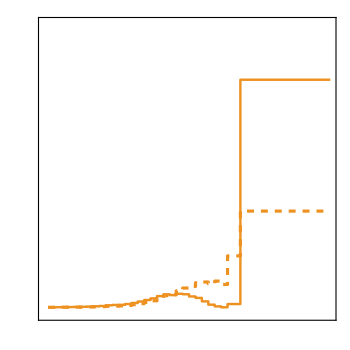

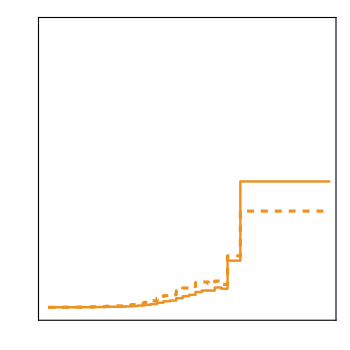

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}]
(*------------------*)
W="lq1";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)

{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]}=JacknifeEXPECTED["di-muon-CMS", 140,W,αβij,{{29,30},{31,32,33,34,35,36,37,38,39,40,41}}];


(* Plots *)

(* positive WC *)
JackPlot[W,αβij]=ListLogLinearPlot[{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                                          UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed,Thickness[0.0065]},{RGBColor[0.93,0.57,0.13],Thickness[0.005]}},
PlotRange->{{200,7000},{0.99,1.4}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lq}^{(1)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}>0",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]

(* negative WC *)
JackPlot[W,αβij]=ListLogLinearPlot[{LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                                                              LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed,Thickness[0.0065]},{RGBColor[0.93,0.57,0.13],Thickness[0.005]}},
PlotRange->{{200,7000},{0.99,1.4}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lq}^{(1)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}<0",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]
```

#### [C_lq^3]_αα11 Clipping

```mathematica
(*------------------*)
W="lq3";
WCTeX="\\mathcal{C}_{lq}^{(3)}";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)

(* linear *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(* Plots *)
plot[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13]},{RGBColor[0.93,0.57,0.13]}},
PlotRange->{{-0.06,0.06},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",True],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{0.02,0.04,0.06},True,1.25],Xticks[{0.02,0.04,0.06},False]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-2

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Clq3 {2, 2, 1, 1}, bin={288.34,312.26}, limits={-0.111658,0.031263}, {χ_min, best fit}={0.53723,{C6→-0.0401974}}

coeff = Clq3 {2, 2, 1, 1}, bin={312.26,338.16}, limits={-0.0929018,0.0280265}, {χ_min, best fit}={0.69668,{C6→-0.0324376}}

coeff = Clq3 {2, 2, 1, 1}, bin={338.16,366.21}, limits={-0.0721844,0.0303473}, {χ_min, best fit}={1.19265,{C6→-0.0209186}}

coeff = Clq3 {2, 2, 1, 1}, bin={366.21,396.59}, limits={-0.0530059,0.0340444}, {χ_min, best fit}={1.87756,{C6→-0.00948077}}

coeff = Clq3 {2, 2, 1, 1}, bin={396.59,429.49}, limits={-0.048688,0.0257073}, {χ_min, best fit}={1.90793,{C6→-0.0114904}}

coeff = Clq3 {2, 2, 1, 1}, bin={429.49,465.12}, limits={-0.0440548,0.0198024}, {χ_min, best fit}={1.91219,{C6→-0.0121262}}

coeff = Clq3 {2, 2, 1, 1}, bin={465.12,503.71}, limits={-0.043014,0.0131987}, {χ_min, best fit}={2.04171,{C6→-0.0149077}}

coeff = Clq3 {2, 2, 1, 1}, bin={503.71,545.49}, limits={-0.0340084,0.016152}, {χ_min, best fit}={2.89505,{C6→-0.00892822}}

coeff = Clq3 {2, 2, 1, 1}, bin={545.49,590.74}, limits={-0.0306817,0.014152}, {χ_min, best fit}={2.90841,{C6→-0.00826485}}

coeff = Clq3 {2, 2, 1, 1}, bin={590.74,639.75}, limits={-0.0239339,0.0159291}, {χ_min, best fit}={3.57152,{C6→-0.00400241}}

coeff = Clq3 {2, 2, 1, 1}, bin={639.75,692.82}, limits={-0.0174576,0.0178414}, {χ_min, best fit}={4.35953,{C6→0.000191908}}

coeff = Clq3 {2, 2, 1, 1}, bin={692.82,750.29}, limits={-0.0174966,0.0137924}, {χ_min, best fit}={4.59995,{C6→-0.0018521}}

coeff = Clq3 {2, 2, 1, 1}, bin={750.29,812.54}, limits={-0.0169275,0.0107683}, {χ_min, best fit}={4.7092,{C6→-0.00307965}}

coeff = Clq3 {2, 2, 1, 1}, bin={812.54,879.94}, limits={-0.0130434,0.0114816}, {χ_min, best fit}={5.19958,{C6→-0.000780893}}

coeff = Clq3 {2, 2, 1, 1}, bin={879.94,952.94}, limits={-0.0128111,0.00898697}, {χ_min, best fit}={5.35523,{C6→-0.00191208}}

coeff = Clq3 {2, 2, 1, 1}, bin={952.94,1032}, limits={-0.0111588,0.0085527}, {χ_min, best fit}={5.42103,{C6→-0.00130304}}

coeff = Clq3 {2, 2, 1, 1}, bin={1032,1117.6}, limits={-0.0104593,0.00734805}, {χ_min, best fit}={5.43475,{C6→-0.00155561}}

coeff = Clq3 {2, 2, 1, 1}, bin={1117.6,1210.3}, limits={-0.0113773,0.00473727}, {χ_min, best fit}={6.26784,{C6→-0.00332002}}

coeff = Clq3 {2, 2, 1, 1}, bin={1210.3,1310.7}, limits={-0.0100896,0.00479318}, {χ_min, best fit}={6.44947,{C6→-0.00264821}}

coeff = Clq3 {2, 2, 1, 1}, bin={1310.7,1419.4}, limits={-0.00929808,0.00449198}, {χ_min, best fit}={6.47895,{C6→-0.00240305}}

coeff = Clq3 {2, 2, 1, 1}, bin={1419.4,1537.2}, limits={-0.00740558,0.00562214}, {χ_min, best fit}={8.19572,{C6→-0.000891721}}

coeff = Clq3 {2, 2, 1, 1}, bin={1537.2,1664.7}, limits={-0.00854712,0.00363968}, {χ_min, best fit}={9.96384,{C6→-0.00245372}}

coeff = Clq3 {2, 2, 1, 1}, bin={1664.7,1802.8}, limits={-0.0090056,0.00246034}, {χ_min, best fit}={10.5682,{C6→-0.00327263}}

coeff = Clq3 {2, 2, 1, 1}, bin={1802.8,1952.4}, limits={-0.00924666,0.00170259}, {χ_min, best fit}={10.8991,{C6→-0.00377204}}

coeff = Clq3 {2, 2, 1, 1}, bin={1952.4,2289.7}, limits={-0.00848005,0.0018013}, {χ_min, best fit}={11.1019,{C6→-0.00333937}}

coeff = Clq3 {2, 2, 1, 1}, bin={2289.7,7000}, limits={-0.00718819,0.00252781}, {χ_min, best fit}={12.4862,{C6→-0.00233019}}

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Clq3 {2, 2, 1, 1}, bin={288.34,312.26}, limits={-0.116181,0.0309425}, {χ_min, best fit}={0.536279,{C6→-0.0407791}}

coeff = Clq3 {2, 2, 1, 1}, bin={312.26,338.16}, limits={-0.0965613,0.0277313}, {χ_min, best fit}={0.694049,{C6→-0.0329232}}

coeff = Clq3 {2, 2, 1, 1}, bin={338.16,366.21}, limits={-0.0748433,0.0299812}, {χ_min, best fit}={1.18943,{C6→-0.0212189}}

coeff = Clq3 {2, 2, 1, 1}, bin={366.21,396.59}, limits={-0.0547698,0.0335698}, {χ_min, best fit}={1.87612,{C6→-0.0096023}}

coeff = Clq3 {2, 2, 1, 1}, bin={396.59,429.49}, limits={-0.0503156,0.0253646}, {χ_min, best fit}={1.90614,{C6→-0.0116256}}

coeff = Clq3 {2, 2, 1, 1}, bin={429.49,465.12}, limits={-0.0455494,0.0195556}, {χ_min, best fit}={1.91039,{C6→-0.0122676}}

coeff = Clq3 {2, 2, 1, 1}, bin={465.12,503.71}, limits={-0.0445578,0.0130667}, {χ_min, best fit}={2.04096,{C6→-0.015093}}

coeff = Clq3 {2, 2, 1, 1}, bin={503.71,545.49}, limits={-0.0352184,0.0159482}, {χ_min, best fit}={2.89231,{C6→-0.00905051}}

coeff = Clq3 {2, 2, 1, 1}, bin={545.49,590.74}, limits={-0.0318045,0.0139695}, {χ_min, best fit}={2.90569,{C6→-0.00837891}}

coeff = Clq3 {2, 2, 1, 1}, bin={590.74,639.75}, limits={-0.0248007,0.0156934}, {χ_min, best fit}={3.57001,{C6→-0.0040611}}

coeff = Clq3 {2, 2, 1, 1}, bin={639.75,692.82}, limits={-0.0180287,0.0175345}, {χ_min, best fit}={4.35952,{C6→0.000194488}}

coeff = Clq3 {2, 2, 1, 1}, bin={692.82,750.29}, limits={-0.0180959,0.0135384}, {χ_min, best fit}={4.59956,{C6→-0.00187126}}

coeff = Clq3 {2, 2, 1, 1}, bin={750.29,812.54}, limits={-0.0175392,0.0105692}, {χ_min, best fit}={4.70859,{C6→-0.00310782}}

coeff = Clq3 {2, 2, 1, 1}, bin={812.54,879.94}, limits={-0.0135039,0.0112424}, {χ_min, best fit}={5.19945,{C6→-0.000788551}}

coeff = Clq3 {2, 2, 1, 1}, bin={879.94,952.94}, limits={-0.0132905,0.00879693}, {χ_min, best fit}={5.35486,{C6→-0.00192766}}

coeff = Clq3 {2, 2, 1, 1}, bin={952.94,1032}, limits={-0.0115855,0.00836104}, {χ_min, best fit}={5.42072,{C6→-0.0013142}}

coeff = Clq3 {2, 2, 1, 1}, bin={1032,1117.6}, limits={-0.0108808,0.00717845}, {χ_min, best fit}={5.43443,{C6→-0.00156828}}

coeff = Clq3 {2, 2, 1, 1}, bin={1117.6,1210.3}, limits={-0.0118816,0.00464756}, {χ_min, best fit}={6.27207,{C6→-0.00334235}}

coeff = Clq3 {2, 2, 1, 1}, bin={1210.3,1310.7}, limits={-0.0105776,0.00469304}, {χ_min, best fit}={6.45016,{C6→-0.0026764}}

coeff = Clq3 {2, 2, 1, 1}, bin={1310.7,1419.4}, limits={-0.00978517,0.00439427}, {χ_min, best fit}={6.47866,{C6→-0.0024346}}

coeff = Clq3 {2, 2, 1, 1}, bin={1419.4,1537.2}, limits={-0.00781604,0.00548465}, {χ_min, best fit}={8.19464,{C6→-0.000909901}}

coeff = Clq3 {2, 2, 1, 1}, bin={1537.2,1664.7}, limits={-0.00903812,0.00355534}, {χ_min, best fit}={9.96701,{C6→-0.0024806}}

coeff = Clq3 {2, 2, 1, 1}, bin={1664.7,1802.8}, limits={-0.00955479,0.00242431}, {χ_min, best fit}={10.5883,{C6→-0.00329787}}

coeff = Clq3 {2, 2, 1, 1}, bin={1802.8,1952.4}, limits={-0.00984696,0.0017035}, {χ_min, best fit}={10.9418,{C6→-0.00379674}}

coeff = Clq3 {2, 2, 1, 1}, bin={1952.4,2289.7}, limits={-0.00919422,0.00177988}, {χ_min, best fit}={11.1201,{C6→-0.00341084}}

coeff = Clq3 {2, 2, 1, 1}, bin={2289.7,7000}, limits={-0.0081716,0.00245469}, {χ_min, best fit}={12.4534,{C6→-0.00249364}}

-Graphics-

#### [C_lq^3]_αα11 Clipping Expected

```mathematica
(*------------------*)
W="lq3";
WCTeX="\\mathcal{C}_{lq}^{(3)}";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)

(* linear *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;


(* Plots *)
plotExp[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13]},{RGBColor[0.93,0.57,0.13]}},
PlotRange->{{-0.3,0.3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",True],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{0.1,0.2,0.3},True,1.25],Xticks[{0.1,0.2,0.3},False]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-2

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Clq3 {2, 2, 1, 1}, bin={288.34,312.26}, limits={-0.0731436,0.0731436}, {χ_min, best fit}={3.14431×10^-42,{C6→-6.61744×10^-23}}

coeff = Clq3 {2, 2, 1, 1}, bin={312.26,338.16}, limits={-0.0619065,0.0619064}, {χ_min, best fit}={3.44129×10^-41,{C6→1.85288×10^-22}}

coeff = Clq3 {2, 2, 1, 1}, bin={338.16,366.21}, limits={-0.0524981,0.0524981}, {χ_min, best fit}={4.78527×10^-41,{C6→-1.85288×10^-22}}

coeff = Clq3 {2, 2, 1, 1}, bin={366.21,396.59}, limits={-0.0445776,0.0445776}, {χ_min, best fit}={2.16713×10^-41,{C6→-1.05879×10^-22}}

coeff = Clq3 {2, 2, 1, 1}, bin={396.59,429.49}, limits={-0.0381194,0.0381193}, {χ_min, best fit}={1.15767×10^-41,{C6→6.61744×10^-23}}

coeff = Clq3 {2, 2, 1, 1}, bin={429.49,465.12}, limits={-0.0327414,0.0327413}, {χ_min, best fit}={1.0043×10^-41,{C6→-5.29396×10^-23}}

coeff = Clq3 {2, 2, 1, 1}, bin={465.12,503.71}, limits={-0.0288447,0.0288447}, {χ_min, best fit}={2.02184×10^-41,{C6→-6.61744×10^-23}}

coeff = Clq3 {2, 2, 1, 1}, bin={503.71,545.49}, limits={-0.0257332,0.0257332}, {χ_min, best fit}={1.01613×10^-40,{C6→-1.32349×10^-22}}

coeff = Clq3 {2, 2, 1, 1}, bin={545.49,590.74}, limits={-0.023011,0.023011}, {χ_min, best fit}={0.,{C6→0.}}

coeff = Clq3 {2, 2, 1, 1}, bin={590.74,639.75}, limits={-0.0204531,0.0204531}, {χ_min, best fit}={2.5736×10^-41,{C6→-5.29396×10^-23}}

coeff = Clq3 {2, 2, 1, 1}, bin={639.75,692.82}, limits={-0.0180983,0.0180983}, {χ_min, best fit}={1.84886×10^-41,{C6→-3.97047×10^-23}}

coeff = Clq3 {2, 2, 1, 1}, bin={692.82,750.29}, limits={-0.0160685,0.0160685}, {χ_min, best fit}={3.75274×10^-40,{C6→-1.58819×10^-22}}

coeff = Clq3 {2, 2, 1, 1}, bin={750.29,812.54}, limits={-0.014245,0.014245}, {χ_min, best fit}={1.62483×10^-40,{C6→9.26442×10^-23}}

coeff = Clq3 {2, 2, 1, 1}, bin={812.54,879.94}, limits={-0.0125941,0.0125941}, {χ_min, best fit}={1.06058×10^-40,{C6→-6.61744×10^-23}}

coeff = Clq3 {2, 2, 1, 1}, bin={879.94,952.94}, limits={-0.0112207,0.0112207}, {χ_min, best fit}={5.13591×10^-39,{C6→-4.10282×10^-22}}

coeff = Clq3 {2, 2, 1, 1}, bin={952.94,1032}, limits={-0.0101424,0.0101424}, {χ_min, best fit}={1.63529×10^-40,{C6→6.61744×10^-23}}

coeff = Clq3 {2, 2, 1, 1}, bin={1032,1117.6}, limits={-0.00917622,0.00917622}, {χ_min, best fit}={1.99779×10^-40,{C6→-6.61744×10^-23}}

coeff = Clq3 {2, 2, 1, 1}, bin={1117.6,1210.3}, limits={-0.00836288,0.00836288}, {χ_min, best fit}={3.84844×10^-41,{C6→-2.64698×10^-23}}

coeff = Clq3 {2, 2, 1, 1}, bin={1210.3,1310.7}, limits={-0.00770954,0.00770954}, {χ_min, best fit}={4.52835×10^-41,{C6→-2.64698×10^-23}}

coeff = Clq3 {2, 2, 1, 1}, bin={1310.7,1419.4}, limits={-0.00714396,0.00714397}, {χ_min, best fit}={5.27373×10^-41,{C6→-2.64698×10^-23}}

coeff = Clq3 {2, 2, 1, 1}, bin={1419.4,1537.2}, limits={-0.00668674,0.00668674}, {χ_min, best fit}={1.5049×10^-41,{C6→-1.32349×10^-23}}

coeff = Clq3 {2, 2, 1, 1}, bin={1537.2,1664.7}, limits={-0.0063419,0.0063419}, {χ_min, best fit}={1.67301×10^-41,{C6→1.32349×10^-23}}

coeff = Clq3 {2, 2, 1, 1}, bin={1664.7,1802.8}, limits={-0.00603145,0.00603145}, {χ_min, best fit}={2.95947×10^-40,{C6→-5.29396×10^-23}}

coeff = Clq3 {2, 2, 1, 1}, bin={1802.8,1952.4}, limits={-0.00580322,0.00580322}, {χ_min, best fit}={3.19683×10^-40,{C6→-5.29396×10^-23}}

coeff = Clq3 {2, 2, 1, 1}, bin={1952.4,2289.7}, limits={-0.00543338,0.00543337}, {χ_min, best fit}={6.58711×10^-39,{C6→-2.24993×10^-22}}

coeff = Clq3 {2, 2, 1, 1}, bin={2289.7,7000}, limits={-0.00504352,0.00504352}, {χ_min, best fit}={1.05811×10^-40,{C6→2.64698×10^-23}}

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Clq3 {2, 2, 1, 1}, bin={288.34,312.26}, limits={-0.074993,0.0714622}, {χ_min, best fit}={1.46769×10^-19,{C6→-1.4297×10^-11}}

coeff = Clq3 {2, 2, 1, 1}, bin={312.26,338.16}, limits={-0.0634087,0.0605352}, {χ_min, best fit}={2.64587×10^-19,{C6→-1.62469×10^-11}}

coeff = Clq3 {2, 2, 1, 1}, bin={338.16,366.21}, limits={-0.0537347,0.0513661}, {χ_min, best fit}={3.41948×10^-19,{C6→-1.5663×10^-11}}

coeff = Clq3 {2, 2, 1, 1}, bin={366.21,396.59}, limits={-0.0456152,0.0436264}, {χ_min, best fit}={6.43277×10^-19,{C6→-1.82418×10^-11}}

coeff = Clq3 {2, 2, 1, 1}, bin={396.59,429.49}, limits={-0.0389992,0.0373121}, {χ_min, best fit}={1.18403×10^-18,{C6→-2.11631×10^-11}}

coeff = Clq3 {2, 2, 1, 1}, bin={429.49,465.12}, limits={-0.0334925,0.0320517}, {χ_min, best fit}={4.42808×10^-18,{C6→-3.51525×10^-11}}

coeff = Clq3 {2, 2, 1, 1}, bin={465.12,503.71}, limits={-0.0295083,0.0282355}, {χ_min, best fit}={4.91517×10^-18,{C6→-3.26277×10^-11}}

coeff = Clq3 {2, 2, 1, 1}, bin={503.71,545.49}, limits={-0.0263349,0.0251815}, {χ_min, best fit}={5.84611×10^-18,{C6→-3.17453×10^-11}}

coeff = Clq3 {2, 2, 1, 1}, bin={545.49,590.74}, limits={-0.023565,0.0225041}, {χ_min, best fit}={9.67391×10^-18,{C6→-3.65165×10^-11}}

coeff = Clq3 {2, 2, 1, 1}, bin={590.74,639.75}, limits={-0.0209664,0.0199848}, {χ_min, best fit}={1.67862×10^-17,{C6→-4.2755×10^-11}}

coeff = Clq3 {2, 2, 1, 1}, bin={639.75,692.82}, limits={-0.0185688,0.0176704}, {χ_min, best fit}={2.92881×10^-17,{C6→-4.9973×10^-11}}

coeff = Clq3 {2, 2, 1, 1}, bin={692.82,750.29}, limits={-0.0165011,0.0156764}, {χ_min, best fit}={5.036×10^-17,{C6→-5.81796×10^-11}}

coeff = Clq3 {2, 2, 1, 1}, bin={750.29,812.54}, limits={-0.0146435,0.0138851}, {χ_min, best fit}={8.77002×10^-17,{C6→-6.80636×10^-11}}

coeff = Clq3 {2, 2, 1, 1}, bin={812.54,879.94}, limits={-0.012961,0.0122639}, {χ_min, best fit}={1.56071×10^-16,{C6→-8.02748×10^-11}}

coeff = Clq3 {2, 2, 1, 1}, bin={879.94,952.94}, limits={-0.0115612,0.0109156}, {χ_min, best fit}={2.67468×10^-16,{C6→-9.36288×10^-11}}

coeff = Clq3 {2, 2, 1, 1}, bin={952.94,1032}, limits={-0.010462,0.00985714}, {χ_min, best fit}={4.29458×10^-16,{C6→-1.07239×10^-10}}

coeff = Clq3 {2, 2, 1, 1}, bin={1032,1117.6}, limits={-0.00947928,0.00890701}, {χ_min, best fit}={7.00546×10^-16,{C6→-1.23918×10^-10}}

coeff = Clq3 {2, 2, 1, 1}, bin={1117.6,1210.3}, limits={-0.00865215,0.00810721}, {χ_min, best fit}={1.10782×10^-15,{C6→-1.42017×10^-10}}

coeff = Clq3 {2, 2, 1, 1}, bin={1210.3,1310.7}, limits={-0.00798961,0.00746334}, {χ_min, best fit}={1.68181×10^-15,{C6→-1.61313×10^-10}}

coeff = Clq3 {2, 2, 1, 1}, bin={1310.7,1419.4}, limits={-0.00741814,0.00690447}, {χ_min, best fit}={2.52833×10^-15,{C6→-1.83277×10^-10}}

coeff = Clq3 {2, 2, 1, 1}, bin={1419.4,1537.2}, limits={-0.00695875,0.00645075}, {χ_min, best fit}={3.67308×10^-15,{C6→-2.06767×10^-10}}

coeff = Clq3 {2, 2, 1, 1}, bin={1537.2,1664.7}, limits={-0.00661517,0.00610648}, {χ_min, best fit}={5.06342×10^-15,{C6→-2.30247×10^-10}}

coeff = Clq3 {2, 2, 1, 1}, bin={1664.7,1802.8}, limits={-0.00630842,0.00579473}, {χ_min, best fit}={6.96808×10^-15,{C6→-2.5688×10^-10}}

coeff = Clq3 {2, 2, 1, 1}, bin={1802.8,1952.4}, limits={-0.0060855,0.00556375}, {χ_min, best fit}={9.04784×10^-15,{C6→-2.81639×10^-10}}

coeff = Clq3 {2, 2, 1, 1}, bin={1952.4,2289.7}, limits={-0.00573317,0.00518334}, {χ_min, best fit}={1.48688×10^-14,{C6→-3.38033×10^-10}}

coeff = Clq3 {2, 2, 1, 1}, bin={2289.7,7000}, limits={-0.00540009,0.00475578}, {χ_min, best fit}={3.05769×10^-14,{C6→-4.49969×10^-10}}

-Graphics-

#### [C_lq^3]_αα22 Clipping Expected

```mathematica
(*------------------*)
W="lq3";
WCTeX="\\mathcal{C}_{lq}^{(3)}";
{i,j}={2,2};
αβij={α,β,i,j};
(*------------------*)
(*
(* linear *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;
*)

(* Plots *)
plotExp[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.11,0.43,0.1],Dashed},{RGBColor[0.11,0.43,0.1],Dashed},{RGBColor[0.11,0.43,0.1]},{RGBColor[0.11,0.43,0.1]}},
PlotRange->{{-3,3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",True],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{1,2.0,3},True,1.25],Xticks[{1,2,3},False]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

-Graphics-

#### [C_lq^3]_αα33 Clipping Expected

```mathematica
(*------------------*)
W="lq3";
WCTeX="\\mathcal{C}_{lq}^{(3)}";
{i,j}={3,3};
αβij={α,β,i,j};
(*------------------*)
(*
(* linear *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;
*)

(* Plots *)
plotExp[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.,0.24,0.6],Dashed},{RGBColor[0.,0.24,0.6],Dashed},{RGBColor[0.,0.24,0.6]},{RGBColor[0.,0.24,0.6]}},
PlotRange->{{-3,3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",True],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{1,2,3},True,1.25],Xticks[{1,2,3},False]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

#### [C_lq^3]_αα11 Jack-knife analysis

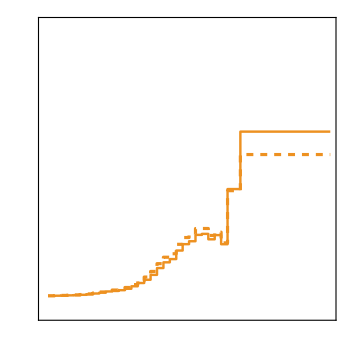

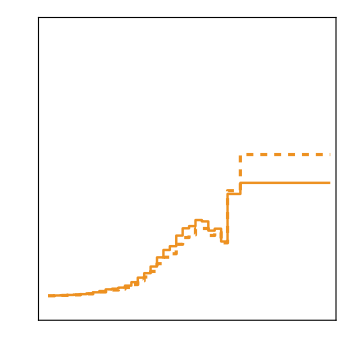

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}]
(*------------------*)
W="lq3";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)

{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]}=JacknifeEXPECTED["di-muon-CMS", 140,W,αβij,{{29,30},{31,32,33,34,35,36,37,38,39,40,41}}];


(* Plots *)

(* positive WC *)
JackPlot[W,αβij]=ListLogLinearPlot[{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                                                              UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed,Thickness[0.0065]},{RGBColor[0.93,0.57,0.13],Thickness[0.005]}},
PlotRange->{{200,7000},{0.99,1.15}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lq}^{(3)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}>0",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]

(* negative WC *)
JackPlot[W,αβij]=ListLogLinearPlot[{LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                                                              LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed,Thickness[0.0065]},{RGBColor[0.93,0.57,0.13],Thickness[0.005]}},
PlotRange->{{200,7000},{0.99,1.15}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lq}^{(3)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}<0",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]
```

#### [C_ld]_αα11 Clipping

```mathematica
(*------------------*)
W="ld";
WCTeX="\\mathcal{C}_{ld}";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)
(*
(* linear *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

*)

(* Plots *)
plot[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13]},{RGBColor[0.93,0.57,0.13]}},
PlotRange->{{-0.3,0.3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",True],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{0.1,0.2,0.3},True,1.25],Xticks[{0.1,0.2,0.3},False]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

-Graphics-

#### [C_ld]_αα11 Clipping Expected

```mathematica
(*------------------*)
W="ld";
WCTeX="\\mathcal{C}_{ld}";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)

(* linear *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;


(* Plots *)
plotExp[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13]},{RGBColor[0.93,0.57,0.13]}},
PlotRange->{{-0.3,0.3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",True],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{0.1,0.2,0.3},True,1.25],Xticks[{0.1,0.2,0.3},False]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-2

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Cld {2, 2, 1, 1}, bin={288.34,312.26}, limits={-0.929942,0.929942}, {χ_min, best fit}={7.96755×10^-43,{C6→4.23516×10^-22}}

coeff = Cld {2, 2, 1, 1}, bin={312.26,338.16}, limits={-0.78332,0.78332}, {χ_min, best fit}={7.0184×10^-44,{C6→1.05879×10^-22}}

coeff = Cld {2, 2, 1, 1}, bin={338.16,366.21}, limits={-0.656441,0.656441}, {χ_min, best fit}={2.49842×10^-42,{C6→-5.29396×10^-22}}

coeff = Cld {2, 2, 1, 1}, bin={366.21,396.59}, limits={-0.555486,0.555486}, {χ_min, best fit}={3.48907×10^-42,{C6→-5.29396×10^-22}}

coeff = Cld {2, 2, 1, 1}, bin={396.59,429.49}, limits={-0.472992,0.472992}, {χ_min, best fit}={0.,{C6→0.}}

coeff = Cld {2, 2, 1, 1}, bin={429.49,465.12}, limits={-0.407683,0.407683}, {χ_min, best fit}={2.33192×10^-42,{C6→-3.17637×10^-22}}

coeff = Cld {2, 2, 1, 1}, bin={465.12,503.71}, limits={-0.356791,0.356791}, {χ_min, best fit}={8.45725×10^-42,{C6→-5.29396×10^-22}}

coeff = Cld {2, 2, 1, 1}, bin={503.71,545.49}, limits={-0.31759,0.31759}, {χ_min, best fit}={3.84261×10^-42,{C6→3.17637×10^-22}}

coeff = Cld {2, 2, 1, 1}, bin={545.49,590.74}, limits={-0.285157,0.285157}, {χ_min, best fit}={2.1184×10^-42,{C6→-2.11758×10^-22}}

coeff = Cld {2, 2, 1, 1}, bin={590.74,639.75}, limits={-0.254655,0.254655}, {χ_min, best fit}={6.6407×10^-43,{C6→-1.05879×10^-22}}

coeff = Cld {2, 2, 1, 1}, bin={639.75,692.82}, limits={-0.225994,0.225994}, {χ_min, best fit}={8.43187×10^-43,{C6→-1.05879×10^-22}}

coeff = Cld {2, 2, 1, 1}, bin={692.82,750.29}, limits={-0.201365,0.201365}, {χ_min, best fit}={0.,{C6→0.}}

coeff = Cld {2, 2, 1, 1}, bin={750.29,812.54}, limits={-0.179187,0.179187}, {χ_min, best fit}={1.20711×10^-41,{C6→3.17637×10^-22}}

coeff = Cld {2, 2, 1, 1}, bin={812.54,879.94}, limits={-0.159079,0.159079}, {χ_min, best fit}={1.70174×10^-42,{C6→-1.05879×10^-22}}

coeff = Cld {2, 2, 1, 1}, bin={879.94,952.94}, limits={-0.142742,0.142742}, {χ_min, best fit}={8.45421×10^-42,{C6→2.11758×10^-22}}

coeff = Cld {2, 2, 1, 1}, bin={952.94,1032}, limits={-0.129428,0.129428}, {χ_min, best fit}={1.0283×10^-41,{C6→2.11758×10^-22}}

coeff = Cld {2, 2, 1, 1}, bin={1032,1117.6}, limits={-0.117546,0.117546}, {χ_min, best fit}={4.98683×10^-41,{C6→-4.23516×10^-22}}

coeff = Cld {2, 2, 1, 1}, bin={1117.6,1210.3}, limits={-0.107922,0.107922}, {χ_min, best fit}={5.19944×10^-43,{C6→3.97047×10^-23}}

coeff = Cld {2, 2, 1, 1}, bin={1210.3,1310.7}, limits={-0.0999953,0.0999953}, {χ_min, best fit}={5.45084×10^-42,{C6→-1.19114×10^-22}}

coeff = Cld {2, 2, 1, 1}, bin={1310.7,1419.4}, limits={-0.0930308,0.0930308}, {χ_min, best fit}={1.52384×10^-41,{C6→1.85288×10^-22}}

coeff = Cld {2, 2, 1, 1}, bin={1419.4,1537.2}, limits={-0.0875555,0.0875555}, {χ_min, best fit}={3.51099×10^-43,{C6→2.64698×10^-23}}

coeff = Cld {2, 2, 1, 1}, bin={1537.2,1664.7}, limits={-0.0836249,0.0836248}, {χ_min, best fit}={8.65983×10^-43,{C6→-3.97047×10^-23}}

coeff = Cld {2, 2, 1, 1}, bin={1664.7,1802.8}, limits={-0.0799503,0.0799504}, {χ_min, best fit}={0.,{C6→0.}}

coeff = Cld {2, 2, 1, 1}, bin={1802.8,1952.4}, limits={-0.0773874,0.0773874}, {χ_min, best fit}={4.04482×10^-42,{C6→-7.94093×10^-23}}

coeff = Cld {2, 2, 1, 1}, bin={1952.4,2289.7}, limits={-0.0733842,0.0733842}, {χ_min, best fit}={1.12454×10^-42,{C6→-3.97047×10^-23}}

coeff = Cld {2, 2, 1, 1}, bin={2289.7,7000}, limits={-0.0698002,0.0698002}, {χ_min, best fit}={8.83901×10^-42,{C6→-1.05879×10^-22}}

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Cld {2, 2, 1, 1}, bin={288.34,312.26}, limits={-1.00093,0.485853}, {χ_min, best fit}={1.0207×10^-20,{C6→-4.79356×10^-11}}

coeff = Cld {2, 2, 1, 1}, bin={312.26,338.16}, limits={-0.858736,0.414934}, {χ_min, best fit}={5.29121×10^-20,{C6→-9.19324×10^-11}}

coeff = Cld {2, 2, 1, 1}, bin={338.16,366.21}, limits={-0.741845,0.353593}, {χ_min, best fit}={9.62453×10^-20,{C6→-1.03905×10^-10}}

coeff = Cld {2, 2, 1, 1}, bin={366.21,396.59}, limits={-0.638647,0.302502}, {χ_min, best fit}={2.7688×10^-19,{C6→-1.49132×10^-10}}

coeff = Cld {2, 2, 1, 1}, bin={396.59,429.49}, limits={-0.548372,0.259344}, {χ_min, best fit}={2.23575×10^-16,{C6→-3.60842×10^-9}}

coeff = Cld {2, 2, 1, 1}, bin={429.49,465.12}, limits={-0.469657,0.223697}, {χ_min, best fit}={2.05129×10^-18,{C6→-2.97912×10^-10}}

coeff = Cld {2, 2, 1, 1}, bin={465.12,503.71}, limits={-0.412191,0.196292}, {χ_min, best fit}={2.64112×10^-17,{C6→-9.35536×10^-10}}

coeff = Cld {2, 2, 1, 1}, bin={503.71,545.49}, limits={-0.36178,0.17411}, {χ_min, best fit}={9.54011×10^-17,{C6→-1.58269×10^-9}}

coeff = Cld {2, 2, 1, 1}, bin={545.49,590.74}, limits={-0.315924,0.154933}, {χ_min, best fit}={2.44063×10^-16,{C6→-2.27294×10^-9}}

coeff = Cld {2, 2, 1, 1}, bin={590.74,639.75}, limits={-0.274778,0.137003}, {χ_min, best fit}={5.73717×10^-16,{C6→-3.11209×10^-9}}

coeff = Cld {2, 2, 1, 1}, bin={639.75,692.82}, limits={-0.237996,0.120348}, {χ_min, best fit}={7.06633×10^-18,{C6→-3.0651×10^-10}}

coeff = Cld {2, 2, 1, 1}, bin={692.82,750.29}, limits={-0.207412,0.106162}, {χ_min, best fit}={1.19058×10^-17,{C6→-3.54498×10^-10}}

coeff = Cld {2, 2, 1, 1}, bin={750.29,812.54}, limits={-0.179667,0.0933163}, {χ_min, best fit}={2.04189×10^-17,{C6→-4.13117×10^-10}}

coeff = Cld {2, 2, 1, 1}, bin={812.54,879.94}, limits={-0.155005,0.0817248}, {χ_min, best fit}={3.56271×10^-17,{C6→-4.84456×10^-10}}

coeff = Cld {2, 2, 1, 1}, bin={879.94,952.94}, limits={-0.134817,0.0722508}, {χ_min, best fit}={5.99165×10^-17,{C6→-5.63738×10^-10}}

coeff = Cld {2, 2, 1, 1}, bin={952.94,1032}, limits={-0.119388,0.0647159}, {χ_min, best fit}={9.53095×10^-17,{C6→-6.44686×10^-10}}

coeff = Cld {2, 2, 1, 1}, bin={1032,1117.6}, limits={-0.105282,0.0579142}, {χ_min, best fit}={1.52525×10^-16,{C6→-7.40676×10^-10}}

coeff = Cld {2, 2, 1, 1}, bin={1117.6,1210.3}, limits={-0.0931444,0.0522289}, {χ_min, best fit}={1.80495×10^-15,{C6→2.33935×10^-9}}

coeff = Cld {2, 2, 1, 1}, bin={1210.3,1310.7}, limits={-0.0830773,0.0474898}, {χ_min, best fit}={2.73185×10^-15,{C6→2.66661×10^-9}}

coeff = Cld {2, 2, 1, 1}, bin={1310.7,1419.4}, limits={-0.0746521,0.0433876}, {χ_min, best fit}={4.05673×10^-15,{C6→3.0232×10^-9}}

coeff = Cld {2, 2, 1, 1}, bin={1419.4,1537.2}, limits={-0.0671802,0.0399316}, {χ_min, best fit}={5.16517×10^-16,{C6→-1.01526×10^-9}}

coeff = Cld {2, 2, 1, 1}, bin={1537.2,1664.7}, limits={-0.0614254,0.0373139}, {χ_min, best fit}={5.54068×10^-16,{C6→-1.00431×10^-9}}

coeff = Cld {2, 2, 1, 1}, bin={1664.7,1802.8}, limits={-0.0559374,0.034788}, {χ_min, best fit}={5.71583×10^-16,{C6→-9.7524×10^-10}}

coeff = Cld {2, 2, 1, 1}, bin={1802.8,1952.4}, limits={-0.0518725,0.032925}, {χ_min, best fit}={1.16459×10^-15,{C6→-1.34744×10^-9}}

coeff = Cld {2, 2, 1, 1}, bin={1952.4,2289.7}, limits={-0.0449791,0.0297517}, {χ_min, best fit}={2.12877×10^-15,{C6→-1.7275×10^-9}}

coeff = Cld {2, 2, 1, 1}, bin={2289.7,7000}, limits={-0.0362576,0.0258367}, {χ_min, best fit}={3.77124×10^-15,{C6→-2.18701×10^-9}}

-Graphics-

#### [C_ld]_αα11 Jack-knife analysis

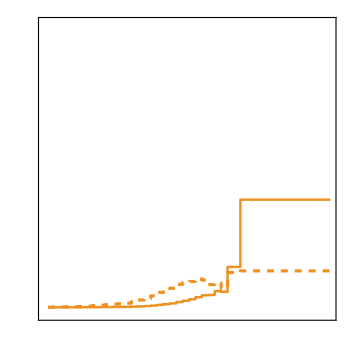

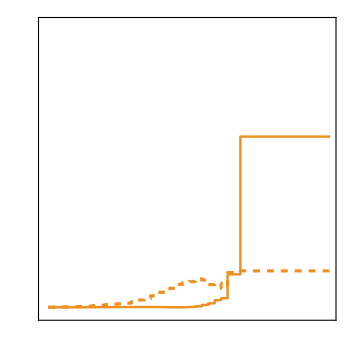

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}]
(*------------------*)
W="ld";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)
(*
{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]}=JacknifeEXPECTED[SEARCH, 140,W,αβij,{{29,30},{31,32,33,34,35,36,37,38,39,40,41}}];

*)
(* Plots *)

(* positive WC *)
JackPlot[W,αβij]=ListLogLinearPlot[{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                                          UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed,Thickness[0.0065]},{RGBColor[0.93,0.57,0.13],Thickness[0.005]}},
PlotRange->{{200,7000},{0.99,1.4}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{ld}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}>0",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]

(* negative WC *)
JackPlot[W,αβij]=ListLogLinearPlot[{LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                                                              LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed,Thickness[0.0065]},{RGBColor[0.93,0.57,0.13],Thickness[0.005]}},
PlotRange->{{200,7000},{0.99,1.4}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{ld}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}<0",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]
```

#### [C_lu]_αα11 Clipping

```mathematica
(*------------------*)
W="lu";
WCTeX="\\mathcal{C}_{lu}";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)

(* linear *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;



(* Plots *)
plot[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13]},{RGBColor[0.93,0.57,0.13]}},
PlotRange->{{-0.3,0.3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",True],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{0.1,0.2,0.3},True,1.25],Xticks[{0.1,0.2,0.3},False]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-2

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Clu {2, 2, 1, 1}, bin={288.34,312.26}, limits={-0.157806,0.565173}, {χ_min, best fit}={0.533155,{C6→0.203683}}

coeff = Clu {2, 2, 1, 1}, bin={312.26,338.16}, limits={-0.140517,0.456752}, {χ_min, best fit}={0.725378,{C6→0.158117}}

coeff = Clu {2, 2, 1, 1}, bin={338.16,366.21}, limits={-0.151244,0.347878}, {χ_min, best fit}={1.23603,{C6→0.0983172}}

coeff = Clu {2, 2, 1, 1}, bin={366.21,396.59}, limits={-0.167949,0.25138}, {χ_min, best fit}={1.90775,{C6→0.0417157}}

coeff = Clu {2, 2, 1, 1}, bin={396.59,429.49}, limits={-0.124748,0.229031}, {χ_min, best fit}={1.94071,{C6→0.0521412}}

coeff = Clu {2, 2, 1, 1}, bin={429.49,465.12}, limits={-0.093801,0.203432}, {χ_min, best fit}={1.94369,{C6→0.0548157}}

coeff = Clu {2, 2, 1, 1}, bin={465.12,503.71}, limits={-0.0609137,0.196279}, {χ_min, best fit}={2.05828,{C6→0.0676825}}

coeff = Clu {2, 2, 1, 1}, bin={503.71,545.49}, limits={-0.0745013,0.153641}, {χ_min, best fit}={2.91961,{C6→0.03957}}

coeff = Clu {2, 2, 1, 1}, bin={545.49,590.74}, limits={-0.0647281,0.13741}, {χ_min, best fit}={2.93393,{C6→0.036341}}

coeff = Clu {2, 2, 1, 1}, bin={590.74,639.75}, limits={-0.0725165,0.105154}, {χ_min, best fit}={3.59679,{C6→0.0163186}}

coeff = Clu {2, 2, 1, 1}, bin={639.75,692.82}, limits={-0.0805723,0.0753574}, {χ_min, best fit}={4.35568,{C6→-0.00260745}}

coeff = Clu {2, 2, 1, 1}, bin={692.82,750.29}, limits={-0.0613247,0.0754694}, {χ_min, best fit}={4.61272,{C6→0.00707236}}

coeff = Clu {2, 2, 1, 1}, bin={750.29,812.54}, limits={-0.0470089,0.0725019}, {χ_min, best fit}={4.7244,{C6→0.0127465}}

coeff = Clu {2, 2, 1, 1}, bin={812.54,879.94}, limits={-0.049865,0.0552231}, {χ_min, best fit}={5.20517,{C6→0.00267909}}

coeff = Clu {2, 2, 1, 1}, bin={879.94,952.94}, limits={-0.0384108,0.0539703}, {χ_min, best fit}={5.36449,{C6→0.00777973}}

coeff = Clu {2, 2, 1, 1}, bin={952.94,1032}, limits={-0.0363295,0.0466096}, {χ_min, best fit}={5.42916,{C6→0.00514009}}

coeff = Clu {2, 2, 1, 1}, bin={1032,1117.6}, limits={-0.0309571,0.0434691}, {χ_min, best fit}={5.44345,{C6→0.00625603}}

coeff = Clu {2, 2, 1, 1}, bin={1117.6,1210.3}, limits={-0.0194998,0.047206}, {χ_min, best fit}={6.25737,{C6→0.0138531}}

coeff = Clu {2, 2, 1, 1}, bin={1210.3,1310.7}, limits={-0.0197299,0.0415824}, {χ_min, best fit}={6.448,{C6→0.0109262}}

coeff = Clu {2, 2, 1, 1}, bin={1310.7,1419.4}, limits={-0.0184014,0.037994}, {χ_min, best fit}={6.4819,{C6→0.00979631}}

coeff = Clu {2, 2, 1, 1}, bin={1419.4,1537.2}, limits={-0.0230485,0.030175}, {χ_min, best fit}={8.19884,{C6→0.00356324}}

coeff = Clu {2, 2, 1, 1}, bin={1537.2,1664.7}, limits={-0.014574,0.0349019}, {χ_min, best fit}={9.93828,{C6→0.0101639}}

coeff = Clu {2, 2, 1, 1}, bin={1664.7,1802.8}, limits={-0.00966534,0.03669}, {χ_min, best fit}={10.5144,{C6→0.0135123}}

coeff = Clu {2, 2, 1, 1}, bin={1802.8,1952.4}, limits={-0.00651045,0.037561}, {χ_min, best fit}={10.8159,{C6→0.0155253}}

coeff = Clu {2, 2, 1, 1}, bin={1952.4,2289.7}, limits={-0.00699104,0.0341095}, {χ_min, best fit}={11.0506,{C6→0.0135592}}

coeff = Clu {2, 2, 1, 1}, bin={2289.7,7000}, limits={-0.0101754,0.0282205}, {χ_min, best fit}={12.5215,{C6→0.00902255}}

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Clu {2, 2, 1, 1}, bin={288.34,312.26}, limits={-0.138686,1.1653}, {χ_min, best fit}={0.502089,{C6→0.288876}}

coeff = Clu {2, 2, 1, 1}, bin={312.26,338.16}, limits={-0.11932,1.03036}, {χ_min, best fit}={0.549279,{C6→0.699779}}

coeff = Clu {2, 2, 1, 1}, bin={338.16,366.21}, limits={-0.114085,0.921351}, {χ_min, best fit}={0.553953,{C6→0.683622}}

coeff = Clu {2, 2, 1, 1}, bin={366.21,396.59}, limits={-0.115251,0.815079}, {χ_min, best fit}={0.649894,{C6→0.637962}}

coeff = Clu {2, 2, 1, 1}, bin={396.59,429.49}, limits={-0.108918,0.674079}, {χ_min, best fit}={2.0063,{C6→0.50153}}

coeff = Clu {2, 2, 1, 1}, bin={429.49,465.12}, limits={-0.0818125,0.568892}, {χ_min, best fit}={1.91597,{C6→0.0661683}}

coeff = Clu {2, 2, 1, 1}, bin={465.12,503.71}, limits={-0.0546064,0.462398}, {χ_min, best fit}={2.04323,{C6→0.082784}}

coeff = Clu {2, 2, 1, 1}, bin={503.71,545.49}, limits={-0.0650638,0.440948}, {χ_min, best fit}={2.87427,{C6→0.0499279}}

coeff = Clu {2, 2, 1, 1}, bin={545.49,590.74}, limits={-0.0564667,0.371758}, {χ_min, best fit}={2.89038,{C6→0.0456354}}

coeff = Clu {2, 2, 1, 1}, bin={590.74,639.75}, limits={-0.0614938,0.341567}, {χ_min, best fit}={3.48365,{C6→0.25987}}

coeff = Clu {2, 2, 1, 1}, bin={639.75,692.82}, limits={-0.0620564,0.306713}, {χ_min, best fit}={3.59133,{C6→0.244423}}

coeff = Clu {2, 2, 1, 1}, bin={692.82,750.29}, limits={-0.0512912,0.236774}, {χ_min, best fit}={4.60903,{C6→0.00800807}}

coeff = Clu {2, 2, 1, 1}, bin={750.29,812.54}, limits={-0.0394981,0.18864}, {χ_min, best fit}={4.71758,{C6→0.0142972}}

coeff = Clu {2, 2, 1, 1}, bin={812.54,879.94}, limits={-0.0411388,0.177542}, {χ_min, best fit}={5.20422,{C6→0.00299081}}

coeff = Clu {2, 2, 1, 1}, bin={879.94,952.94}, limits={-0.0317849,0.140023}, {χ_min, best fit}={5.36049,{C6→0.0085803}}

coeff = Clu {2, 2, 1, 1}, bin={952.94,1032}, limits={-0.0298056,0.125809}, {χ_min, best fit}={5.42596,{C6→0.00568308}}

coeff = Clu {2, 2, 1, 1}, bin={1032,1117.6}, limits={-0.0253479,0.105678}, {χ_min, best fit}={5.44005,{C6→0.00688558}}

coeff = Clu {2, 2, 1, 1}, bin={1117.6,1210.3}, limits={-0.0165969,0.0780651}, {χ_min, best fit}={6.3174,{C6→0.0144675}}

coeff = Clu {2, 2, 1, 1}, bin={1210.3,1310.7}, limits={-0.0164891,0.075561}, {χ_min, best fit}={6.45964,{C6→0.0123358}}

coeff = Clu {2, 2, 1, 1}, bin={1310.7,1419.4}, limits={-0.0152819,0.0690562}, {χ_min, best fit}={6.47993,{C6→0.0115422}}

coeff = Clu {2, 2, 1, 1}, bin={1419.4,1537.2}, limits={-0.0187194,0.0735206}, {χ_min, best fit}={8.18357,{C6→0.00476343}}

coeff = Clu {2, 2, 1, 1}, bin={1537.2,1664.7}, limits={-0.0120981,0.0515089}, {χ_min, best fit}={9.98402,{C6→0.0112546}}

coeff = Clu {2, 2, 1, 1}, bin={1664.7,1802.8}, limits={-0.00880429,0.041338}, {χ_min, best fit}={10.8135,{C6→0.012246}}

coeff = Clu {2, 2, 1, 1}, bin={1802.8,1952.4}, limits={-0.00694357,0.0360838}, {χ_min, best fit}={11.4281,{C6→0.0121954}}

coeff = Clu {2, 2, 1, 1}, bin={1952.4,2289.7}, limits={-0.00676482,0.0338422}, {χ_min, best fit}={11.4469,{C6→0.0124015}}

coeff = Clu {2, 2, 1, 1}, bin={2289.7,7000}, limits={-0.0071931,0.0314614}, {χ_min, best fit}={11.8257,{C6→0.0179358}}

-Graphics-

#### [C_lu]_αα11 Clipping Expected

```mathematica
(*------------------*)
W="lu";
WCTeX="\\mathcal{C}_{lu}";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)

(* linear *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;


(* Plots *)
plotExp[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13]},{RGBColor[0.93,0.57,0.13]}},
PlotRange->{{-0.3,0.3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",True],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{0.1,0.2,0.3},True,1.25],Xticks[{0.1,0.2,0.3},False]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-2

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Clu {2, 2, 1, 1}, bin={288.34,312.26}, limits={-0.360322,0.360322}, {χ_min, best fit}={1.19409×10^-41,{C6→-6.35275×10^-22}}

coeff = Clu {2, 2, 1, 1}, bin={312.26,338.16}, limits={-0.297659,0.297659}, {χ_min, best fit}={4.86047×10^-43,{C6→-1.05879×10^-22}}

coeff = Clu {2, 2, 1, 1}, bin={338.16,366.21}, limits={-0.248709,0.248709}, {χ_min, best fit}={6.26579×10^-42,{C6→-3.17637×10^-22}}

coeff = Clu {2, 2, 1, 1}, bin={366.21,396.59}, limits={-0.208895,0.208895}, {χ_min, best fit}={8.88183×10^-42,{C6→-3.17637×10^-22}}

coeff = Clu {2, 2, 1, 1}, bin={396.59,429.49}, limits={-0.176292,0.176292}, {χ_min, best fit}={2.21704×10^-41,{C6→-4.23516×10^-22}}

coeff = Clu {2, 2, 1, 1}, bin={429.49,465.12}, limits={-0.148152,0.148152}, {χ_min, best fit}={1.7658×10^-41,{C6→-3.17637×10^-22}}

coeff = Clu {2, 2, 1, 1}, bin={465.12,503.71}, limits={-0.128253,0.128253}, {χ_min, best fit}={4.18893×10^-41,{C6→4.23516×10^-22}}

coeff = Clu {2, 2, 1, 1}, bin={503.71,545.49}, limits={-0.113704,0.113704}, {χ_min, best fit}={2.55022×10^-42,{C6→-9.26442×10^-23}}

coeff = Clu {2, 2, 1, 1}, bin={545.49,590.74}, limits={-0.100756,0.100756}, {χ_min, best fit}={6.62819×10^-42,{C6→-1.32349×10^-22}}

coeff = Clu {2, 2, 1, 1}, bin={590.74,639.75}, limits={-0.0884938,0.0884938}, {χ_min, best fit}={8.59234×10^-44,{C6→-1.32349×10^-23}}

coeff = Clu {2, 2, 1, 1}, bin={639.75,692.82}, limits={-0.0775755,0.0775755}, {χ_min, best fit}={4.02523×10^-42,{C6→-7.94093×10^-23}}

coeff = Clu {2, 2, 1, 1}, bin={692.82,750.29}, limits={-0.0681484,0.0681484}, {χ_min, best fit}={1.44886×10^-41,{C6→-1.32349×10^-22}}

coeff = Clu {2, 2, 1, 1}, bin={750.29,812.54}, limits={-0.0596141,0.0596141}, {χ_min, best fit}={1.21177×10^-41,{C6→1.05879×10^-22}}

coeff = Clu {2, 2, 1, 1}, bin={812.54,879.94}, limits={-0.0523108,0.0523109}, {χ_min, best fit}={8.8523×10^-42,{C6→-7.94093×10^-23}}

coeff = Clu {2, 2, 1, 1}, bin={879.94,952.94}, limits={-0.0460877,0.0460877}, {χ_min, best fit}={1.26715×10^-42,{C6→-2.64698×10^-23}}

coeff = Clu {2, 2, 1, 1}, bin={952.94,1032}, limits={-0.0413457,0.0413457}, {χ_min, best fit}={9.8405×10^-42,{C6→-6.61744×10^-23}}

coeff = Clu {2, 2, 1, 1}, bin={1032,1117.6}, limits={-0.0371481,0.0371481}, {χ_min, best fit}={1.9504×10^-42,{C6→-2.64698×10^-23}}

coeff = Clu {2, 2, 1, 1}, bin={1117.6,1210.3}, limits={-0.033541,0.033541}, {χ_min, best fit}={1.93789×10^-40,{C6→-2.38228×10^-22}}

coeff = Clu {2, 2, 1, 1}, bin={1210.3,1310.7}, limits={-0.0307588,0.0307588}, {χ_min, best fit}={5.76081×10^-41,{C6→-1.19114×10^-22}}

coeff = Clu {2, 2, 1, 1}, bin={1310.7,1419.4}, limits={-0.0282848,0.0282848}, {χ_min, best fit}={3.36428×10^-42,{C6→-2.64698×10^-23}}

coeff = Clu {2, 2, 1, 1}, bin={1419.4,1537.2}, limits={-0.0264366,0.0264366}, {χ_min, best fit}={2.40695×10^-41,{C6→-6.61744×10^-23}}

coeff = Clu {2, 2, 1, 1}, bin={1537.2,1664.7}, limits={-0.0249415,0.0249415}, {χ_min, best fit}={3.9048×10^-40,{C6→-2.51463×10^-22}}

coeff = Clu {2, 2, 1, 1}, bin={1664.7,1802.8}, limits={-0.0236305,0.0236305}, {χ_min, best fit}={2.36181×10^-40,{C6→1.85288×10^-22}}

coeff = Clu {2, 2, 1, 1}, bin={1802.8,1952.4}, limits={-0.0226448,0.0226448}, {χ_min, best fit}={2.09952×10^-41,{C6→-5.29396×10^-23}}

coeff = Clu {2, 2, 1, 1}, bin={1952.4,2289.7}, limits={-0.0210366,0.0210366}, {χ_min, best fit}={1.36845×10^-41,{C6→3.97047×10^-23}}

coeff = Clu {2, 2, 1, 1}, bin={2289.7,7000}, limits={-0.0192216,0.0192217}, {χ_min, best fit}={6.55629×10^-41,{C6→-7.94093×10^-23}}

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Clu {2, 2, 1, 1}, bin={288.34,312.26}, limits={-0.284222,1.26541}, {χ_min, best fit}={3.81567×10^-20,{C6→3.5911×10^-11}}

coeff = Clu {2, 2, 1, 1}, bin={312.26,338.16}, limits={-0.237563,1.07173}, {χ_min, best fit}={7.20278×10^-20,{C6→4.07588×10^-11}}

coeff = Clu {2, 2, 1, 1}, bin={338.16,366.21}, limits={-0.199924,0.890836}, {χ_min, best fit}={3.08711×10^-19,{C6→7.05049×10^-11}}

coeff = Clu {2, 2, 1, 1}, bin={366.21,396.59}, limits={-0.168512,0.724445}, {χ_min, best fit}={5.48×10^-18,{C6→-2.495×10^-10}}

coeff = Clu {2, 2, 1, 1}, bin={396.59,429.49}, limits={-0.14289,0.610894}, {χ_min, best fit}={1.37381×10^-19,{C6→-3.33386×10^-11}}

coeff = Clu {2, 2, 1, 1}, bin={429.49,465.12}, limits={-0.121019,0.533343}, {χ_min, best fit}={1.51831×10^-20,{C6→-9.31412×10^-12}}

coeff = Clu {2, 2, 1, 1}, bin={465.12,503.71}, limits={-0.105159,0.456407}, {χ_min, best fit}={1.1864×10^-18,{C6→7.12745×10^-11}}

coeff = Clu {2, 2, 1, 1}, bin={503.71,545.49}, limits={-0.0929992,0.355809}, {χ_min, best fit}={1.97493×10^-18,{C6→8.15278×10^-11}}

coeff = Clu {2, 2, 1, 1}, bin={545.49,590.74}, limits={-0.0822132,0.282746}, {χ_min, best fit}={3.29408×10^-18,{C6→9.33018×10^-11}}

coeff = Clu {2, 2, 1, 1}, bin={590.74,639.75}, limits={-0.0719446,0.233451}, {χ_min, best fit}={9.69043×10^-18,{C6→-1.40552×10^-10}}

coeff = Clu {2, 2, 1, 1}, bin={639.75,692.82}, limits={-0.0628033,0.204787}, {χ_min, best fit}={1.15762×10^-17,{C6→1.34667×10^-10}}

coeff = Clu {2, 2, 1, 1}, bin={692.82,750.29}, limits={-0.0549582,0.18234}, {χ_min, best fit}={2.03696×10^-17,{C6→1.56928×10^-10}}

coeff = Clu {2, 2, 1, 1}, bin={750.29,812.54}, limits={-0.0479494,0.163445}, {χ_min, best fit}={2.64403×10^-16,{C6→-4.94577×10^-10}}

coeff = Clu {2, 2, 1, 1}, bin={812.54,879.94}, limits={-0.041874,0.141763}, {χ_min, best fit}={6.49807×10^-17,{C6→2.15147×10^-10}}

coeff = Clu {2, 2, 1, 1}, bin={879.94,952.94}, limits={-0.0367648,0.125689}, {χ_min, best fit}={6.36864×10^-18,{C6→-5.93417×10^-11}}

coeff = Clu {2, 2, 1, 1}, bin={952.94,1032}, limits={-0.0328197,0.110654}, {χ_min, best fit}={1.94812×10^-16,{C6→2.94435×10^-10}}

coeff = Clu {2, 2, 1, 1}, bin={1032,1117.6}, limits={-0.0293239,0.0975337}, {χ_min, best fit}={3.18198×10^-16,{C6→3.38094×10^-10}}

coeff = Clu {2, 2, 1, 1}, bin={1117.6,1210.3}, limits={-0.0262883,0.0854377}, {χ_min, best fit}={5.17514×10^-16,{C6→3.89304×10^-10}}

coeff = Clu {2, 2, 1, 1}, bin={1210.3,1310.7}, limits={-0.0239219,0.0757326}, {χ_min, best fit}={7.94354×10^-16,{C6→4.42312×10^-10}}

coeff = Clu {2, 2, 1, 1}, bin={1310.7,1419.4}, limits={-0.0218178,0.067557}, {χ_min, best fit}={1.2102×10^-15,{C6→5.02034×10^-10}}

coeff = Clu {2, 2, 1, 1}, bin={1419.4,1537.2}, limits={-0.0201688,0.0596546}, {χ_min, best fit}={1.58508×10^-15,{C6→5.37011×10^-10}}

coeff = Clu {2, 2, 1, 1}, bin={1537.2,1664.7}, limits={-0.0188426,0.0541509}, {χ_min, best fit}={2.20181×10^-15,{C6→5.97124×10^-10}}

coeff = Clu {2, 2, 1, 1}, bin={1664.7,1802.8}, limits={-0.0176264,0.0485034}, {χ_min, best fit}={3.07712×10^-15,{C6→6.68802×10^-10}}

coeff = Clu {2, 2, 1, 1}, bin={1802.8,1952.4}, limits={-0.0166965,0.044388}, {χ_min, best fit}={4.0529×10^-15,{C6→7.35535×10^-10}}

coeff = Clu {2, 2, 1, 1}, bin={1952.4,2289.7}, limits={-0.015091,0.0371498}, {χ_min, best fit}={1.82825×10^-18,{C6→-1.45126×10^-11}}

coeff = Clu {2, 2, 1, 1}, bin={2289.7,7000}, limits={-0.0128767,0.0267002}, {χ_min, best fit}={8.53508×10^-19,{C6→-9.06038×10^-12}}

-Graphics-

#### [C_lu]_αα11 Jack-knife analysis

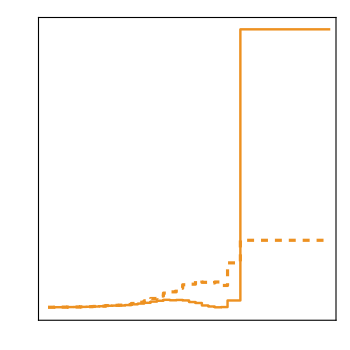

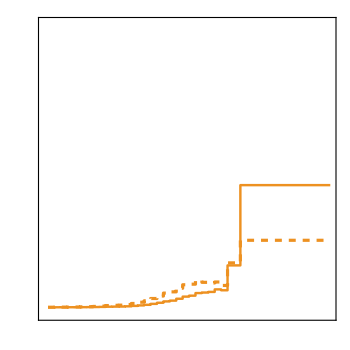

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}]
(*------------------*)
W="lu";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)

(*
{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]}=JacknifeEXPECTED[SEARCH, 140,W,αβij,{{29,30},{31,32,33,34,35,36,37,38,39,40,41}}];
*)

(* Plots *)

(* positive WC *)
JackPlot[W,αβij]=ListLogLinearPlot[{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                                          UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed,Thickness[0.0065]},{RGBColor[0.93,0.57,0.13],Thickness[0.005]}},
PlotRange->{{200,7000},{0.99,1.4}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lu}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}>0",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]

(* negative WC *)
JackPlot[W,αβij]=ListLogLinearPlot[{LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                                                              LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed,Thickness[0.0065]},{RGBColor[0.93,0.57,0.13],Thickness[0.005]}},
PlotRange->{{200,7000},{0.99,1.4}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lu}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}<0",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]
```

#### [C_ledq]_αα11 Clipping

```mathematica
(*------------------*)
W="ledq";
WCTeX="\\mathcal{C}_{ledq}";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)
(*
(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;
*)


(* Plots *)
plot[W,ToString[αβij]]=ListPlot[{  
                    Append[  UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.93,0.57,0.13]},{RGBColor[0.93,0.57,0.13]}},
PlotRange->{{-0.3,0.3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",False],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{0.1,0.2,0.3},True,1.25],Xticks[{0.1,0.2,0.3},False]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

-Graphics-

#### [C_ledq]_αα11 Clipping Expected

```mathematica
(*------------------*)
W="ledq";
WCTeX="\\mathcal{C}_{ledq}";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)

(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;


(* Plots *)
plotExp[W,ToString[αβij]]=ListPlot[{ 
                    Append[  UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.93,0.57,0.13]},{RGBColor[0.93,0.57,0.13]}},
PlotRange->{{-0.3,0.3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",False],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{0.1,0.2,0.3},True,1.25],Xticks[{0.1,0.2,0.3},False]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Cledq {2, 2, 1, 1}, bin={288.34,312.26}, limits={-0.545889,0.545889}, {χ_min, best fit}={5.26287×10^-24,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={312.26,338.16}, limits={-0.471626,0.471626}, {χ_min, best fit}={9.44601×10^-24,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={338.16,366.21}, limits={-0.40582,0.40582}, {χ_min, best fit}={1.72309×10^-23,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={366.21,396.59}, limits={-0.349686,0.349686}, {χ_min, best fit}={3.12555×10^-23,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={396.59,429.49}, limits={-0.301558,0.301558}, {χ_min, best fit}={5.65142×10^-23,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={429.49,465.12}, limits={-0.25993,0.25993}, {χ_min, best fit}={1.0238×10^-22,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={465.12,503.71}, limits={-0.229043,0.229043}, {χ_min, best fit}={1.69813×10^-22,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={503.71,545.49}, limits={-0.203089,0.203089}, {χ_min, best fit}={2.74725×10^-22,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={545.49,590.74}, limits={-0.179106,0.179106}, {χ_min, best fit}={4.54156×10^-22,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={590.74,639.75}, limits={-0.156606,0.156606}, {χ_min, best fit}={7.76977×10^-22,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={639.75,692.82}, limits={-0.136742,0.136742}, {χ_min, best fit}={1.33671×10^-21,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={692.82,750.29}, limits={-0.119995,0.119995}, {χ_min, best fit}={2.2542×10^-21,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={750.29,812.54}, limits={-0.104972,0.104972}, {χ_min, best fit}={3.84899×10^-21,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={812.54,879.94}, limits={-0.0912955,0.0912955}, {χ_min, best fit}={6.72733×10^-21,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={879.94,952.94}, limits={-0.0803014,0.0803014}, {χ_min, best fit}={1.12395×10^-20,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={952.94,1032}, limits={-0.0713282,0.0713282}, {χ_min, best fit}={1.80549×10^-20,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={1032,1117.6}, limits={-0.063456,0.063456}, {χ_min, best fit}={2.88237×10^-20,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={1117.6,1210.3}, limits={-0.0568029,0.0568029}, {χ_min, best fit}={4.48909×10^-20,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={1210.3,1310.7}, limits={-0.05131,0.05131}, {χ_min, best fit}={6.7427×10^-20,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={1310.7,1419.4}, limits={-0.0464091,0.0464091}, {χ_min, best fit}={1.00746×10^-19,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={1419.4,1537.2}, limits={-0.0423137,0.0423137}, {χ_min, best fit}={1.45787×10^-19,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={1537.2,1664.7}, limits={-0.03916,0.03916}, {χ_min, best fit}={1.98733×10^-19,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={1664.7,1802.8}, limits={-0.0361824,0.0361824}, {χ_min, best fit}={2.72678×10^-19,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={1802.8,1952.4}, limits={-0.0338787,0.0338787}, {χ_min, best fit}={3.54759×10^-19,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={1952.4,2289.7}, limits={-0.0300318,0.0300318}, {χ_min, best fit}={5.74537×10^-19,{C6→5.9059×10^-7}}

coeff = Cledq {2, 2, 1, 1}, bin={2289.7,7000}, limits={-0.0253636,0.0253636}, {χ_min, best fit}={1.12926×10^-18,{C6→5.9059×10^-7}}

-Graphics-

#### [C_ledq]_αα11 Jack-knife analysis

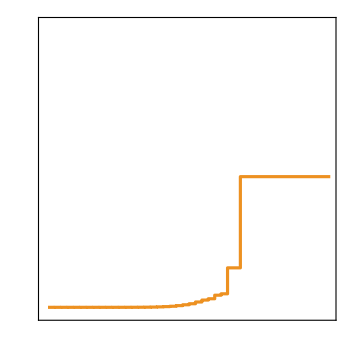

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}]
(*------------------*)
W="ledq";
WCTeX="\\mathcal{C}_{ledq}";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)

(*UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]=JacknifeEXPECTED4[SEARCH, 140,W,αβij,{{29,30},{31,32,33,34,35,36,37,38,39,40,41}}];
*)
(* Plots *)

JackPlot[W,αβij]=ListLogLinearPlot[{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Thickness[0.0065]}},
PlotRange->{{200,7000},{0.99,1.4}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]
```

#### [C_lequ^3]_αα11 Clipping

```mathematica
(*------------------*)
W="lequ3";
WCTeX="\\mathcal{C}_{lequ}^{(3)}";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)
(*
(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

*)

(* Plots *)
plot[W,ToString[αβij]]=ListPlot[{  
                    Append[  UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.93,0.57,0.13]},{RGBColor[0.93,0.57,0.13]}},
PlotRange->{{-0.06,0.06},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",False],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{0.02,0.04,0.06},True,1.25],Xticks[{0.1,0.2,0.3},False]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

-Graphics-

#### [C_lequ^3]_αα11 Clipping Expected

```mathematica
(*------------------*)
W="lequ3";
WCTeX="\\mathcal{C}_{lequ}^{(3)}";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)


(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;


(* Plots *)
plotExp[W,ToString[αβij]]=ListPlot[{ 
                    Append[  UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.93,0.57,0.13]},{RGBColor[0.93,0.57,0.13]}},
PlotRange->{{-0.06,0.06},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",False],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{0.02,0.04,0.06},True,1.25],Xticks[{0.02,0.04,0.06},False]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Clequ3 {2, 2, 1, 1}, bin={288.34,312.26}, limits={-0.256868,0.256868}, {χ_min, best fit}={1.0735×10^-22,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={312.26,338.16}, limits={-0.219135,0.219135}, {χ_min, best fit}={2.02673×10^-22,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={338.16,366.21}, limits={-0.185233,0.185233}, {χ_min, best fit}={3.96977×10^-22,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={366.21,396.59}, limits={-0.158374,0.158374}, {χ_min, best fit}={7.42865×10^-22,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={396.59,429.49}, limits={-0.133521,0.133521}, {χ_min, best fit}={1.47041×10^-21,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={429.49,465.12}, limits={-0.113982,0.113982}, {χ_min, best fit}={2.76881×10^-21,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={465.12,503.71}, limits={-0.0989238,0.0989238}, {χ_min, best fit}={4.88021×10^-21,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={503.71,545.49}, limits={-0.0863826,0.0863826}, {χ_min, best fit}={8.39336×10^-21,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={545.49,590.74}, limits={-0.075604,0.075604}, {χ_min, best fit}={1.43041×10^-20,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={590.74,639.75}, limits={-0.0654917,0.0654917}, {χ_min, best fit}={2.54036×10^-20,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={639.75,692.82}, limits={-0.0561325,0.0561325}, {χ_min, best fit}={4.70743×10^-20,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={692.82,750.29}, limits={-0.0487382,0.0487382}, {χ_min, best fit}={8.28251×10^-20,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={750.29,812.54}, limits={-0.0420293,0.0420293}, {χ_min, best fit}={1.49773×10^-19,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={812.54,879.94}, limits={-0.0360808,0.0360808}, {χ_min, best fit}={2.75764×10^-19,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={879.94,952.94}, limits={-0.0312743,0.0312743}, {χ_min, best fit}={4.88526×10^-19,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={952.94,1032}, limits={-0.0275682,0.0275682}, {χ_min, best fit}={8.09112×10^-19,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={1032,1117.6}, limits={-0.0241902,0.0241902}, {χ_min, best fit}={1.36483×10^-18,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={1117.6,1210.3}, limits={-0.0213758,0.0213758}, {χ_min, best fit}={2.23849×10^-18,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={1210.3,1310.7}, limits={-0.0190562,0.0190562}, {χ_min, best fit}={3.54401×10^-18,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={1310.7,1419.4}, limits={-0.0170569,0.0170569}, {χ_min, best fit}={5.52135×10^-18,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={1419.4,1537.2}, limits={-0.015374,0.015374}, {χ_min, best fit}={8.36557×10^-18,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={1537.2,1664.7}, limits={-0.0140112,0.0140112}, {χ_min, best fit}={1.21267×10^-17,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={1664.7,1802.8}, limits={-0.0127734,0.0127734}, {χ_min, best fit}={1.75557×10^-17,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={1802.8,1952.4}, limits={-0.0118095,0.0118095}, {χ_min, best fit}={2.40275×10^-17,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={1952.4,2289.7}, limits={-0.0101374,0.0101374}, {χ_min, best fit}={4.42514×10^-17,{C6→5.9059×10^-7}}

coeff = Clequ3 {2, 2, 1, 1}, bin={2289.7,7000}, limits={-0.00754171,0.00754171}, {χ_min, best fit}={1.44464×10^-16,{C6→5.9059×10^-7}}

-Graphics-

#### [C_lequ^3]_αα11 Jack-knife analysis

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

limit full spectrum = {-0.00740656, 0.00740656}

limit removing 1 bin = 1.

limit removing 2 bin = 1.

limit removing 3 bin = 1.

limit removing 4 bin = 1.

limit removing 5 bin = 1.

limit removing 6 bin = 1.

limit removing 7 bin = 1.

limit removing 8 bin = 1.

limit removing 9 bin = 1.

limit removing 10 bin = 1.

limit removing 11 bin = 1.

limit removing 12 bin = 1.00001

limit removing 13 bin = 1.00001

limit removing 14 bin = 1.00002

limit removing 15 bin = 1.00004

limit removing 16 bin = 1.00006

limit removing 17 bin = 1.00011

limit removing 18 bin = 1.00022

limit removing 19 bin = 1.00037

limit removing 20 bin = 1.00055

limit removing 21 bin = 1.00096

limit removing 22 bin = 1.00151

limit removing 23 bin = 1.00226

limit removing 24 bin = 1.00343

limit removing 25 bin = 1.00496

limit removing 26 bin = 1.0066

limit removing 27 bin = 1.0096

limit removing 28 bin = 1.0115

limit removing 29 bin = 1.03838

limit removing 30 bin = 1.345

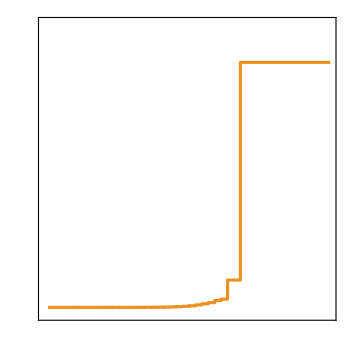

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}]
(*------------------*)
W="lequ3";
WCTeX="\\mathcal{C}_{lequ}^{(3)}";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)

UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]=JacknifeEXPECTED4[SEARCH, 140,W,αβij,{{29,30},{31,32,33,34,35,36,37,38,39,40,41}}];

(* Plots *)

JackPlot[W,αβij]=ListLogLinearPlot[{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Thickness[0.0065]}},
PlotRange->{{200,7000},{0.99,1.4}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]
```

#### [C_dW]_αα11 Clipping Expected

```mathematica
(*------------------*)
W="dW";
WCTeX="\\mathcal{C}_{dW}";
{i,j}={1,1};
ij={i,j};
αβij={α,β,i,j};


(*------------------*)
(* observed limits: *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]
(*-----------*)

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,Luminosity->141, OperatorDimension->OPERATORDIM,Coefficients->{WC[W,ij ]}]/.{WC[W,ij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(*----- Plots ------*)

plotExp[W,ToString[αβij]]=ListPlot[{
                    Append[ UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[ LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.93,0.57,0.13]},{RGBColor[0.93,0.57,0.13]}},
PlotRange->{{-3,3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",True],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{1,2,3},True,1.25],Xticks[{1,2,3},False, 1.25]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = CdW {2, 2, 1, 1}, bin={288.34,312.26}, limits={-1.41638,1.41638}, {χ_min, best fit}={1.16125×10^-25,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={312.26,338.16}, limits={-1.31666,1.31666}, {χ_min, best fit}={1.55503×10^-25,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={338.16,366.21}, limits={-1.22444,1.22444}, {χ_min, best fit}={2.0792×10^-25,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={366.21,396.59}, limits={-1.14104,1.14104}, {χ_min, best fit}={2.75705×10^-25,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={396.59,429.49}, limits={-1.06523,1.06523}, {χ_min, best fit}={3.62964×10^-25,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={429.49,465.12}, limits={-0.999487,0.999487}, {χ_min, best fit}={4.68309×10^-25,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={465.12,503.71}, limits={-0.946651,0.946651}, {χ_min, best fit}={5.81943×10^-25,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={503.71,545.49}, limits={-0.900762,0.900762}, {χ_min, best fit}={7.09905×10^-25,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={545.49,590.74}, limits={-0.858187,0.858187}, {χ_min, best fit}={8.61615×10^-25,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={590.74,639.75}, limits={-0.815563,0.815563}, {χ_min, best fit}={1.05636×10^-24,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={639.75,692.82}, limits={-0.774262,0.774262}, {χ_min, best fit}={1.30044×10^-24,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={692.82,750.29}, limits={-0.736242,0.736242}, {χ_min, best fit}={1.59059×10^-24,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={750.29,812.54}, limits={-0.699781,0.699781}, {χ_min, best fit}={1.94891×10^-24,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={812.54,879.94}, limits={-0.66324,0.66324}, {χ_min, best fit}={2.41523×10^-24,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={879.94,952.94}, limits={-0.631446,0.631446}, {χ_min, best fit}={2.93965×10^-24,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={952.94,1032}, limits={-0.604709,0.604709}, {χ_min, best fit}={3.49507×10^-24,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={1032,1117.6}, limits={-0.579381,0.579381}, {χ_min, best fit}={4.14747×10^-24,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={1117.6,1210.3}, limits={-0.556926,0.556926}, {χ_min, best fit}={4.85792×10^-24,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={1210.3,1310.7}, limits={-0.53858,0.53858}, {χ_min, best fit}={5.55444×10^-24,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={1310.7,1419.4}, limits={-0.52184,0.52184}, {χ_min, best fit}={6.30219×10^-24,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={1419.4,1537.2}, limits={-0.507556,0.507556}, {χ_min, best fit}={7.04217×10^-24,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={1537.2,1664.7}, limits={-0.496818,0.496818}, {χ_min, best fit}={7.671×10^-24,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={1664.7,1802.8}, limits={-0.486927,0.486927}, {χ_min, best fit}={8.31353×10^-24,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={1802.8,1952.4}, limits={-0.479548,0.479548}, {χ_min, best fit}={8.83714×10^-24,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={1952.4,2289.7}, limits={-0.468182,0.468182}, {χ_min, best fit}={9.72705×10^-24,{C6→5.9059×10^-7}}

coeff = CdW {2, 2, 1, 1}, bin={2289.7,7000}, limits={-0.458897,0.458897}, {χ_min, best fit}={1.05385×10^-23,{C6→5.9059×10^-7}}

-Graphics-

```mathematica
Export["CdW_2211_Clipped.pdf",Rasterize[plotExp["dW",ToString[{2,2,1,1}]],ImageResolution->400]];
```

#### [C_lq^1]_αα22 Clipping Expected

```mathematica
(*------------------*)
W="lq1";
WCTeX="\\mathcal{C}_{lq}^{(1)}";
{i,j}={2,2};
αβij={α,β,i,j};
(*------------------*)

(*(* linear *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;
*)

(* Plots *)
plotExp[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.11,0.43,0.1],Dashed},{RGBColor[0.11,0.43,0.1],Dashed},{RGBColor[0.11,0.43,0.1]},{RGBColor[0.11,0.43,0.1]}},
PlotRange->{{-3,3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",True],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{1,2,3},True,1.25],Xticks[{1,2,3},False,1.25]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]//Quiet
```

-Graphics-

```mathematica
Export["Clq1_2222_Clipped.pdf",Rasterize[plotExp["lq1",ToString[{2,2,2,2}]],ImageResolution->400]];
```

#### [C_lq^1]_αα33 Clipping Expected

```mathematica
(*------------------*)
W="lq1";
WCTeX="\\mathcal{C}_{lq}^{(1)}";
{i,j}={3,3};
αβij={α,β,i,j};
(*------------------*)

(* linear *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(* quadratic *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}, Luminosity-> LUMINOSITY]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;


(* Plots *)
plotExp[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsExp[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.,0.24,0.6],Dashed},{RGBColor[0.,0.24,0.6],Dashed},{RGBColor[0.,0.24,0.6]},{RGBColor[0.,0.24,0.6]}},
PlotRange->{{-3,3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> ClippedEpi["\\mu\\mu",True],
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{1,2,3},True,1.25],Xticks[{1,2,3},False,1.25]} },
FrameLabel->{MaTeX["["<>WCTeX<>"]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-2

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Clq1 {2, 2, 3, 3}, bin={288.34,312.26}, limits={-2.35275,2.35275}, {χ_min, best fit}={3.85235×10^-17,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={312.26,338.16}, limits={-2.08331,2.08331}, {χ_min, best fit}={4.91323×10^-17,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={338.16,366.21}, limits={-1.8585,1.8585}, {χ_min, best fit}={6.17381×10^-17,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={366.21,396.59}, limits={-1.67374,1.67374}, {χ_min, best fit}={7.61202×10^-17,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={396.59,429.49}, limits={-1.5212,1.5212}, {χ_min, best fit}={9.21517×10^-17,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={429.49,465.12}, limits={-1.3969,1.3969}, {χ_min, best fit}={3.86786×10^-18,{C6→-1.4017×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={465.12,503.71}, limits={-1.30586,1.30586}, {χ_min, best fit}={1.25049×10^-16,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={503.71,545.49}, limits={-1.23274,1.23274}, {χ_min, best fit}={1.40324×10^-16,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={545.49,590.74}, limits={-1.16999,1.16999}, {χ_min, best fit}={1.55781×10^-16,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={590.74,639.75}, limits={-1.11199,1.11199}, {χ_min, best fit}={1.72455×10^-16,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={639.75,692.82}, limits={-1.05835,1.05835}, {χ_min, best fit}={1.90379×10^-16,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={692.82,750.29}, limits={-1.01272,1.01272}, {χ_min, best fit}={2.07922×10^-16,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={750.29,812.54}, limits={-0.970466,0.970466}, {χ_min, best fit}={2.2642×10^-16,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={812.54,879.94}, limits={-0.931357,0.931357}, {χ_min, best fit}={0.,{C6→0.}}

coeff = Clq1 {2, 2, 3, 3}, bin={879.94,952.94}, limits={-0.899488,0.899488}, {χ_min, best fit}={2.60809×10^-42,{C6→-7.41154×10^-22}}

coeff = Clq1 {2, 2, 3, 3}, bin={952.94,1032}, limits={-0.874093,0.874093}, {χ_min, best fit}={5.6364×10^-44,{C6→1.05879×10^-22}}

coeff = Clq1 {2, 2, 3, 3}, bin={1032,1117.6}, limits={-0.851833,0.851833}, {χ_min, best fit}={0.,{C6→0.}}

coeff = Clq1 {2, 2, 3, 3}, bin={1117.6,1210.3}, limits={-0.83378,0.83378}, {χ_min, best fit}={2.47784×10^-43,{C6→2.11758×10^-22}}

coeff = Clq1 {2, 2, 3, 3}, bin={1210.3,1310.7}, limits={-0.81997,0.81997}, {χ_min, best fit}={1.0248×10^-42,{C6→-4.23516×10^-22}}

coeff = Clq1 {2, 2, 3, 3}, bin={1310.7,1419.4}, limits={-0.808727,0.808727}, {χ_min, best fit}={2.63374×10^-43,{C6→2.11758×10^-22}}

coeff = Clq1 {2, 2, 3, 3}, bin={1419.4,1537.2}, limits={-0.799966,0.799966}, {χ_min, best fit}={2.69174×10^-43,{C6→-2.11758×10^-22}}

coeff = Clq1 {2, 2, 3, 3}, bin={1537.2,1664.7}, limits={-0.794227,0.794227}, {χ_min, best fit}={0.,{C6→0.}}

coeff = Clq1 {2, 2, 3, 3}, bin={1664.7,1802.8}, limits={-0.789725,0.789725}, {χ_min, best fit}={1.72625×10^-42,{C6→-5.29396×10^-22}}

coeff = Clq1 {2, 2, 3, 3}, bin={1802.8,1952.4}, limits={-0.786867,0.786867}, {χ_min, best fit}={2.78211×10^-43,{C6→-2.11758×10^-22}}

coeff = Clq1 {2, 2, 3, 3}, bin={1952.4,2289.7}, limits={-0.783212,0.783212}, {χ_min, best fit}={1.12325×10^-42,{C6→-4.23516×10^-22}}

coeff = Clq1 {2, 2, 3, 3}, bin={2289.7,7000}, limits={-0.781192,0.781192}, {χ_min, best fit}={1.12907×10^-42,{C6→-4.23516×10^-22}}

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Clq1 {2, 2, 3, 3}, bin={288.34,312.26}, limits={-4.14494,1.52686}, {χ_min, best fit}={2.01569×10^-21,{C6→5.38939×10^-11}}

coeff = Clq1 {2, 2, 3, 3}, bin={312.26,338.16}, limits={-3.64501,1.35592}, {χ_min, best fit}={3.18784×10^-21,{C6→6.00144×10^-11}}

coeff = Clq1 {2, 2, 3, 3}, bin={338.16,366.21}, limits={-3.18033,1.20732}, {χ_min, best fit}={5.07089×10^-21,{C6→6.75236×10^-11}}

coeff = Clq1 {2, 2, 3, 3}, bin={366.21,396.59}, limits={-2.75595,1.07961}, {χ_min, best fit}={7.61219×10^-17,{C6→-7.45067×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={396.59,429.49}, limits={-2.40484,0.972006}, {χ_min, best fit}={9.21559×10^-17,{C6→-7.45075×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={429.49,465.12}, limits={-2.0953,0.880447}, {χ_min, best fit}={1.12129×10^-16,{C6→-7.54705×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={465.12,503.71}, limits={-1.88345,0.81343}, {χ_min, best fit}={1.2505×10^-16,{C6→-7.4506×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={503.71,545.49}, limits={-1.68915,0.756174}, {χ_min, best fit}={1.40325×10^-16,{C6→-7.45063×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={545.49,590.74}, limits={-1.52167,0.705665}, {χ_min, best fit}={1.55784×10^-16,{C6→-7.45067×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={590.74,639.75}, limits={-1.36106,0.65692}, {χ_min, best fit}={1.72461×10^-16,{C6→-7.45071×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={639.75,692.82}, limits={-1.21121,0.610031}, {χ_min, best fit}={1.90389×10^-16,{C6→-7.45077×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={692.82,750.29}, limits={-1.08777,0.569213}, {χ_min, best fit}={2.07937×10^-16,{C6→-7.45084×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={750.29,812.54}, limits={-0.979139,0.530992}, {χ_min, best fit}={2.26441×10^-16,{C6→-7.45093×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={812.54,879.94}, limits={-0.880283,0.494716}, {χ_min, best fit}={2.45865×10^-16,{C6→-7.45104×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={879.94,952.94}, limits={-0.799513,0.464116}, {χ_min, best fit}={2.63605×10^-16,{C6→-7.45116×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={952.94,1032}, limits={-0.734648,0.438831}, {χ_min, best fit}={2.79154×10^-16,{C6→-7.45129×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={1032,1117.6}, limits={-0.675632,0.415435}, {χ_min, best fit}={2.93945×10^-16,{C6→-7.45143×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={1117.6,1210.3}, limits={-0.622998,0.394579}, {χ_min, best fit}={3.06824×10^-16,{C6→-7.45158×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={1210.3,1310.7}, limits={-0.582265,0.377855}, {χ_min, best fit}={3.17158×10^-16,{C6→-7.45054×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={1310.7,1419.4}, limits={-0.546277,0.362947}, {χ_min, best fit}={3.26042×10^-16,{C6→-7.45058×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={1419.4,1537.2}, limits={-0.516662,0.350426}, {χ_min, best fit}={3.33347×10^-16,{C6→-7.45198×10^-9}}

coeff = Clq1 {2, 2, 3, 3}, bin={1537.2,1664.7}, limits={-0.492911,0.340618}, {χ_min, best fit}={1.17337×10^-19,{C6→-1.38808×10^-10}}

coeff = Clq1 {2, 2, 3, 3}, bin={1664.7,1802.8}, limits={-0.471172,0.331654}, {χ_min, best fit}={1.30065×10^-19,{C6→-1.45314×10^-10}}

coeff = Clq1 {2, 2, 3, 3}, bin={1802.8,1952.4}, limits={-0.454883,0.324945}, {χ_min, best fit}={3.25755×10^-21,{C6→-2.29139×10^-11}}

coeff = Clq1 {2, 2, 3, 3}, bin={1952.4,2289.7}, limits={-0.428808,0.314167}, {χ_min, best fit}={1.5715×10^-19,{C6→-1.58412×10^-10}}

coeff = Clq1 {2, 2, 3, 3}, bin={2289.7,7000}, limits={-0.399801,0.302564}, {χ_min, best fit}={1.73533×10^-19,{C6→-1.66036×10^-10}}

-Graphics-

```mathematica
Export["Clq1_2233_Clipped.pdf",Rasterize[plotExp["lq1",ToString[{2,2,3,3}]],ImageResolution->400]];
```

## Mono-electrons

```mathematica
(*--------------------------------------------------------------------*)
Λ=1000;
{α,β}={1,1};
SEARCH="mono-electron-ATLAS";
LUMINOSITY=140;
DefaultBins["mono-electron-ATLAS"]={207.519,221.857,237.186,253.575,271.095,289.827,309.852,331.261,354.15,378.62,404.781,432.749,462.65,494.616,528.792,565.329,604.39,646.15,690.796,738.526,789.555,844.109,902.433,964.786,1031.45,1102.72,1178.91,1260.36,1347.45,1440.55,1540.09,1646.5,1760.26,2011.92,10000};
{bmin,bmax}={5,Length[DefaultBins["mono-electron-ATLAS"]]-1}; 
(*--------------------------------------------------------------------*)

LHCSearch[SEARCH]
```

#### [C_lq^3]_αα11 Jack-knife analysis

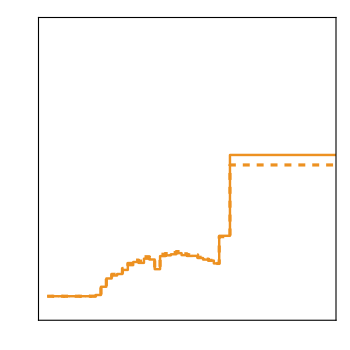

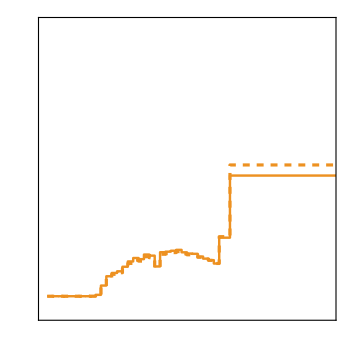

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}]
(*------------------*)
W="lq3";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)

{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]}=JacknifeEXPECTED[SEARCH, 140,W,αβij,{{33,34},{35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58}}];


(* Plots *)

(* positive WC *)
JackPlot[W,αβij]=ListLogLinearPlot[{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                                                              UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed,Thickness[0.0065]},{RGBColor[0.93,0.57,0.13],Thickness[0.005]}},
PlotRange->{{200,7000},{0.99,1.15}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lq}^{(3)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}>0",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]

(* negative WC *)
JackPlot[W,αβij]=ListLogLinearPlot[{LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                                                              LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed,Thickness[0.0065]},{RGBColor[0.93,0.57,0.13],Thickness[0.005]}},
PlotRange->{{200,7000},{0.99,1.15}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lq}^{(3)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}<0",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]
```

## Mono-muon χ^2 extractions

```mathematica
(*--------------------------------------------------------------------*)
Λ=1000;
{α,β}={2,2};
SEARCH="mono-muon-ATLAS";
LUMINOSITY=140;
DefaultBins["mono-muon-ATLAS"]={214.564,233.253,253.57,275.657,299.667,325.769,354.144,384.991,418.524,454.979,494.609,537.69,584.525,635.438,690.786,750.956,816.366,887.473,964.775,1048.81,1140.16,1239.47,1347.44,1464.8,1592.39,1731.09,1881.87,2223.98,10000};
{bmin,bmax}={5,Length[DefaultBins["mono-muon-ATLAS"]]-1}; 
(*--------------------------------------------------------------------*)

LHCSearch[SEARCH]
```

#### [C_lq^3]_αα11 Jack-knife analysis

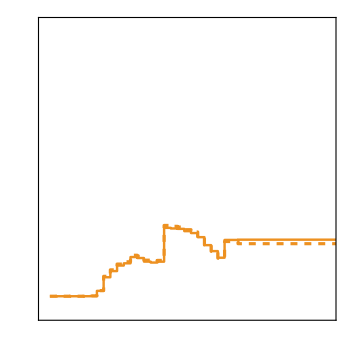

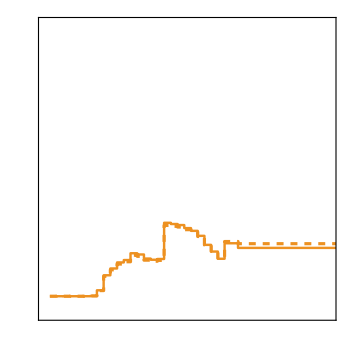

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}]
(*------------------*)
W="lq3";
{i,j}={1,1};
αβij={α,β,i,j};
(*------------------*)

{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]}=JacknifeEXPECTED[SEARCH, 140,W,αβij,{{27,28},{29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46}}];


(* Plots *)

(* positive WC *)
JackPlot[W,αβij]=ListLogLinearPlot[{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                                                              UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed,Thickness[0.0065]},{RGBColor[0.93,0.57,0.13],Thickness[0.005]}},
PlotRange->{{200,7000},{0.99,1.15}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lq}^{(3)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}>0",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]

(* negative WC *)
JackPlot[W,αβij]=ListLogLinearPlot[{LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                                                              LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed,Thickness[0.0065]},{RGBColor[0.93,0.57,0.13],Thickness[0.005]}},
PlotRange->{{200,7000},{0.99,1.15}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lq}^{(3)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}<0",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]
```

## Dimuon χ^2 extractions [OLD]

```mathematica
(*--------------------------------------------------------------------*)
Λ=1000;
{α,β}={2,2};
SEARCH="di-muon-CMS";
LUMINOSITY=141;
{bmin,bmax}={5,30}; 
(*--------------------------------------------------------------------*)

LHCSearch[SEARCH]
DefaultBins["di-muon-CMS"]={209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2289.7,7000};
{DefaultBins[SEARCH][[bmin]],DefaultBins[SEARCH][[bmax]]}
```

<|INFO→<|ARXIV→[arXiv:2103.02708](https://arxiv.org/abs/2103.02708),SOURCE→[hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4),DESCRIPTION→The invariant mass spectra of dimuon events.,EXPERIMENT→CMS,PROCESS→p p > μ^- μ^+,FINALSTATE→{e[2],e[2]},OBSERVABLE→m_μμ,LUMINOSITY→140,CMENERGY→13000,BINS→<|OBSERVABLE→{209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000},MLL→{200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000},PT→{0,∞}|>|>,DATA→{49128,41800,32648,26435,21188,16797,13170,10490,7650,6128,4613,3457,2635,1979,1478,1016,759,574,389,295,202,132,107,71,59,27,18,13,11,5,5,4,2,1,1,0,0,0,0,0,0},BACKGROUND→{50469.3,41839.9,32989.,26921.1,21531.6,16912.7,13098.5,10333.8,7769.34,6219.57,4759.3,3379.58,2662.33,1926.39,1417.98,1048.48,781.922,553.886,403.303,292.15,206.536,148.227,105.5,71.9137,49.5856,35.7306,22.9439,16.5921,9.79576,6.26511,3.93946,2.75556,1.43541,0.856615,0.536371,0.271383,0.139182,0.110295,0.0306152,0.00583208,0.00094739},ERROR-BKG→{1391.01,1108.09,905.112,739.993,613.787,503.444,396.767,311.091,242.262,193.881,167.365,140.151,112.668,85.8949,64.8728,50.746,37.1769,26.5778,20.075,16.0183,10.9671,7.77697,5.86035,4.02962,2.83474,2.4225,1.34904,1.13735,0.622781,0.441341,0.27607,0.253813,0.110243,0.0698684,0.056433,0.0338829,0.0167852,0.0198925,0.0064995,0.00203296,0.00051924},DEFAULT-BINNING→{{29,30},{31,32,33,34,35,36,37,38,39,40,41}}|>

#### [C_lq^1]_αα11

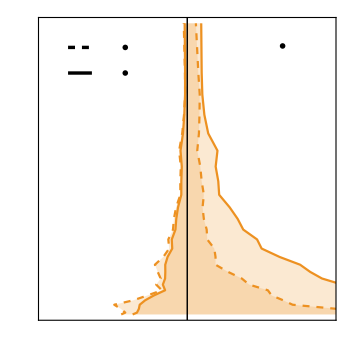

```mathematica
W="lq1";
{i,j}={1,1};
αβij={α,β,i,j};
(*
(*------------------*)
(* observed limits: *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]
(*------------------*)

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]},CombineBins-> {{29,30},{31,32,33,34,35,36,37,38,39,40,41}}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(*-----------*)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]
(*-----------*)

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]},CombineBins-> {{29,30},{31,32,33,34,35,36,37,38,39,40,41}}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;
*)
(*----- Plots ------*)

plot[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13],Dashed},{RGBColor[0.93,0.57,0.13]},{RGBColor[0.93,0.57,0.13]}},
PlotRange->{{-0.30,0.30},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog->{{Directive[{Thickness[0.003],Black}],Line[{{0,0},{0,3000}}],Directive[{Thickness[0.007],Black}],Line[{{-0.25,1950},{-0.20,1950}}],Directive[{Thickness[0.007],Black,Dashed}],Line[{{-0.25,2125},{-0.20,2125}}]}, 
                   Text[MaTeX["\\mathcal{O}(1/\\Lambda^2)",Magnification->1.2],{-0.13,2125},Center],
                   Text[MaTeX["\\mathcal{O}(1/\\Lambda^4)",Magnification->1.2],{-0.13,1950},Center],
                   Text[MaTeX["pp\\to \mu\mu",Magnification->1.4],{0.2,2135},Center]},
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{0.1,0.2,0.3},True,1.25],Xticks[{0.1,0.2,0.3},False]} },
FrameLabel->{MaTeX["[\\mathcal{C}_{lq}^{(1)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

#### [C_lq^1]_αα22

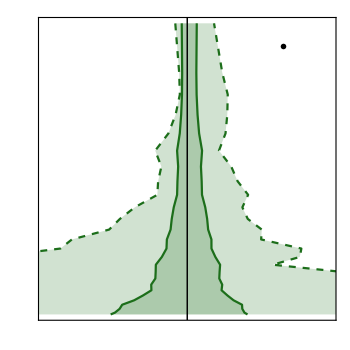

```mathematica
W="lq1";
{i,j}={2,2};
αβij={α,β,i,j};
(*
(*------------------*)
(* observed limits: *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]
(*------------------*)

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(*-----------*)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]
(*-----------*)

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;
*)
(*----- Plots ------*)

plot[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.11,0.43,0.1],Dashed},{RGBColor[0.11,0.43,0.1],Dashed},{RGBColor[0.11,0.43,0.1]},{RGBColor[0.11,0.43,0.1]}},
PlotRange->{{-1.5,1.5},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog->{{Directive[{Thickness[0.003],Black}],Line[{{0,0},{0,3000}}],Directive[{Thickness[0.007],Black}]},Text[MaTeX["pp\\to \mu\mu",Magnification->1.4
],{1.,2135},Center]},
FrameTicks->{{Yticks[False,1.3],Yticks[False,1.3]},{Xticks[{0.5,1.0,1.5},True,1.3],Xticks[{0.5,1.0,1.3},False]} },
FrameLabel->{MaTeX["[\\mathcal{C}_{lq}^{(1)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75]}
]
```

#### [C_lq^1]_αα33

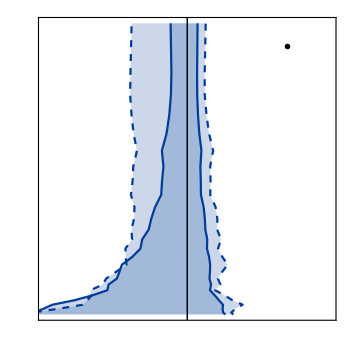

```mathematica
W="lq1";
{i,j}={3,3};
αβij={α,β,i,j};

(*(*------------------*)
(* observed limits: *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]
(*------------------*)

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;

(*-----------*)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]
(*-----------*)

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;
*)
(*----- Plots ------*)

plot[W,ToString[αβij]]=ListPlot[{  Append[ UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.,0.24,0.6],Dashed},{RGBColor[0.,0.24,0.6],Dashed},{RGBColor[0.,0.24,0.6]},{RGBColor[0.,0.24,0.6]}},
PlotRange->{{-3,3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog->{{Directive[{Thickness[0.003],Black}],Line[{{0,0},{0,3000}}],Directive[{Thickness[0.007],Black}]},Text[MaTeX["pp\\to \mu\mu",Magnification->1.4],{2.1,2135},Center]},
FrameTicks->{{Yticks[False,1.3],Yticks[False,1.3]},{Xticks[{1,2,3},True,1.3],Xticks[{1,2,3},False]} },
FrameLabel->{MaTeX["[\\mathcal{C}_{lq}^{(1)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75]}
]
```

#### [C_lq^1]_αα12

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-2

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

Part::partd: Part specification 0⟦{29,30}⟧ is longer than depth of object.

Part::partd: Part specification 0⟦{31,32,33,34,35,36,37,38,39,40,41}⟧ is longer than depth of object.

Thread::tdlen: Objects of unequal length in {1.93491×10^6,1.22787×10^6,819228.,547590.,376735.,253456.,157424.,96777.7,58691.1,37589.7,28011.,19642.3,12694.1,7377.94,4208.48,2575.16,1382.13,706.382,403.006,256.587,120.277,60.4813,34.3437,16.2378,8.03575,5.86851,1.81992,1.29356,0.582638,0.162728}+{16,13} cannot be combined.

Thread::tdlen: Objects of unequal length in {16,13}+{1.93491×10^6,1.22787×10^6,819228.,547590.,376735.,253456.,157424.,96777.7,58691.1,37589.7,28011.,19642.3,12694.1,7377.94,4208.48,2575.16,1382.13,706.382,403.006,256.587,120.277,60.4813,34.3437,16.2378,8.03575,5.86851,1.81992,1.29356,0.582638,0.162728} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Part::partw: Part 3 of {{844.534 Re[1/({16,13}+{1.93491×10^6,1.22787×10^6,819228.,547590.,376735.,253456.,157424.,96777.7,58691.1,37589.7,28011.,19642.3,12694.1,7377.94,4208.48,2575.16,1382.13,706.382,403.006,256.587,120.277,60.4813,34.3437,16.2378,8.03575,5.86851,1.81992,1.29356,0.582638,0.162728})],903.656 Re[1/({16,13}+{1.93491×10^6,1.22787×10^6,819228.,547590.,376735.,253456.,157424.,96777.7,58691.1,«13»,34.3437,16.2378,8.03575,5.86851,1.81992,1.29356,0.582638,0.162728})]},{788.58 Re[1/({16,13}+{1.93491×10^6,1.22787×10^6,819228.,«24»,1.29356,0.582638,0.162728})],845.744 Re[1/({16,13}+{«1»})],904.907 Re[1/(«1»)],«6»,1375.05 Re[1/({16,13}+{«1»})],1450.21 Re[1/({16,13}+{1.93491×10^6,«28»,0.162728})]}} does not exist.

Part::partw: Part 4 of {{844.534 Re[1/({16,13}+{1.93491×10^6,1.22787×10^6,819228.,547590.,376735.,253456.,157424.,96777.7,58691.1,37589.7,28011.,19642.3,12694.1,7377.94,4208.48,2575.16,1382.13,706.382,403.006,256.587,120.277,60.4813,34.3437,16.2378,8.03575,5.86851,1.81992,1.29356,0.582638,0.162728})],903.656 Re[1/({16,13}+{1.93491×10^6,1.22787×10^6,819228.,547590.,376735.,253456.,157424.,96777.7,58691.1,«13»,34.3437,16.2378,8.03575,5.86851,1.81992,1.29356,0.582638,0.162728})]},{788.58 Re[1/({16,13}+{1.93491×10^6,1.22787×10^6,819228.,«24»,1.29356,0.582638,0.162728})],845.744 Re[1/({16,13}+{«1»})],904.907 Re[1/(«1»)],«6»,1375.05 Re[1/({16,13}+{«1»})],1450.21 Re[1/({16,13}+{1.93491×10^6,«28»,0.162728})]}} does not exist.

Part::partw: Part 5 of {{844.534 Re[1/({16,13}+{1.93491×10^6,1.22787×10^6,819228.,547590.,376735.,253456.,157424.,96777.7,58691.1,37589.7,28011.,19642.3,12694.1,7377.94,4208.48,2575.16,1382.13,706.382,403.006,256.587,120.277,60.4813,34.3437,16.2378,8.03575,5.86851,1.81992,1.29356,0.582638,0.162728})],903.656 Re[1/({16,13}+{1.93491×10^6,1.22787×10^6,819228.,547590.,376735.,253456.,157424.,96777.7,58691.1,«13»,34.3437,16.2378,8.03575,5.86851,1.81992,1.29356,0.582638,0.162728})]},{788.58 Re[1/({16,13}+{1.93491×10^6,1.22787×10^6,819228.,«24»,1.29356,0.582638,0.162728})],845.744 Re[1/({16,13}+{«1»})],904.907 Re[1/(«1»)],«6»,1375.05 Re[1/({16,13}+{«1»})],1450.21 Re[1/({16,13}+{1.93491×10^6,«28»,0.162728})]}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {844.534 Re[1/({16,13}+{1.93491×10^6,1.22787×10^6,819228.,547590.,376735.,253456.,157424.,96777.7,58691.1,37589.7,28011.,19642.3,12694.1,7377.94,4208.48,2575.16,1382.13,706.382,403.006,256.587,120.277,60.4813,34.3437,16.2378,8.03575,5.86851,1.81992,1.29356,0.582638,0.162728})],903.656 Re[1/({16,13}+{1.93491×10^6,1.22787×10^6,819228.,547590.,376735.,253456.,157424.,96777.7,58691.1,«13»,34.3437,16.2378,8.03575,5.86851,1.81992,1.29356,0.582638,0.162728})]}+«3»+{{844.534 Re[1/Plus[«2»]],903.656 Re[1/Plus[«2»]]},«1»}⟦5⟧ cannot be combined.

Thread::tdlen: Objects of unequal length in {16,13}+{1.93491×10^6,1.22787×10^6,819228.,547590.,376735.,253456.,157424.,96777.7,58691.1,37589.7,28011.,19642.3,12694.1,7377.94,4208.48,2575.16,1382.13,706.382,403.006,256.587,120.277,60.4813,34.3437,16.2378,8.03575,5.86851,1.81992,1.29356,0.582638,0.162728} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

NMinimize::nnum: The function value {844.534 Re[1/({16,13}+{1.93491×10^6,1.22787×10^6,819228.,547590.,376735.,253456.,157424.,96777.7,58691.1,37589.7,28011.,19642.3,12694.1,7377.94,4208.48,2575.16,1382.13,706.382,403.006,256.587,120.277,60.4813,34.3437,16.2378,8.03575,5.86851,1.81992,1.29356,0.582638,0.162728})],903.656 Re[1/({16,13}+{1.93491×10^6,1.22787×10^6,819228.,547590.,376735.,253456.,157424.,96777.7,58691.1,«13»,34.3437,16.2378,8.03575,5.86851,1.81992,1.29356,0.582638,0.162728})]}+«3»+{{844.534 Re[1/Plus[«2»]],903.656 Re[1/Plus[«2»]]},«1»}⟦5⟧ is not a number at {C6} = {-0.829053}.

Set::shape: Lists {χsqrMin,bestfit} and … are not the same shape.

NMinimize::nnum: The function value {844.534 Re[1/({16,13}+{1.93491×10^6,1.22787×10^6,819228.,547590.,376735.,253456.,157424.,96777.7,58691.1,37589.7,28011.,19642.3,12694.1,7377.94,4208.48,2575.16,1382.13,706.382,403.006,256.587,120.277,60.4813,34.3437,16.2378,8.03575,5.86851,1.81992,1.29356,0.582638,0.162728})],903.656 Re[1/({16,13}+{1.93491×10^6,1.22787×10^6,819228.,547590.,376735.,253456.,157424.,96777.7,58691.1,«13»,34.3437,16.2378,8.03575,5.86851,1.81992,1.29356,0.582638,0.162728})]}+«3»+{{844.534 Re[1/Plus[«2»]],903.656 Re[1/Plus[«2»]]},«1»}⟦5⟧ is not a number at {C6} = {-0.829053}.

ImplicitRegion::msgs: Evaluation of … generated message(s) {General::stop,Part::partw,Thread::tdlen}.

coeff = Clq1 {2, 2, 1, 2}, bin={288.34,312.26}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

NMinimize::nnum: The function value {844.534 Re[1/({16,13}+{1.93491×10^6,1.22787×10^6,819228.,547590.,376735.,253456.,157424.,96777.7,58691.1,37589.7,28011.,19642.3,12694.1,7377.94,4208.48,2575.16,1382.13,706.382,403.006,256.587,120.277,60.4813,34.3437,16.2378,8.03575,5.86851,1.81992,1.29356,0.582638,0.162728})],903.656 Re[1/({16,13}+{1.93491×10^6,1.22787×10^6,819228.,547590.,376735.,253456.,157424.,96777.7,58691.1,«13»,34.3437,16.2378,8.03575,5.86851,1.81992,1.29356,0.582638,0.162728})]}+{«1»}+«2»+«1»⟦5⟧+{{844.534 Re[1/Plus[«2»]],903.656 Re[1/Plus[«2»]]},{788.58 Re[1/Plus[«2»]],845.744 Re[1/Plus[«2»]],904.907 Re[1/Plus[«2»]],966.07 Re[1/Plus[«2»]],«4»,1301.89 Re[1/Plus[«2»]],1375.05 Re[1/Plus[«2»]],1450.21 Re[1/Plus[«2»]]}}⟦6⟧ is not a number at {C6} = {-0.829053}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

Set::shape: Lists {χsqrMin,bestfit} and … are not the same shape.

ImplicitRegion::msgs: Evaluation of … generated message(s) {General::stop,Part::partw,Thread::tdlen}.

General::stop: Further output of ImplicitRegion::msgs will be suppressed during this calculation.

coeff = Clq1 {2, 2, 1, 2}, bin={312.26,338.16}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

Set::shape: Lists {χsqrMin,bestfit} and … are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

coeff = Clq1 {2, 2, 1, 2}, bin={338.16,366.21}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={366.21,396.59}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={396.59,429.49}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={429.49,465.12}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={465.12,503.71}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={503.71,545.49}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={545.49,590.74}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={590.74,639.75}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={639.75,692.82}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={692.82,750.29}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={750.29,812.54}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={812.54,879.94}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={879.94,952.94}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={952.94,1032}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={1032,1117.6}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={1117.6,1210.3}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={1210.3,1310.7}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={1310.7,1419.4}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={1419.4,1537.2}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={1537.2,1664.7}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={1664.7,1802.8}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={1802.8,1952.4}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={1952.4,2289.7}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

coeff = Clq1 {2, 2, 1, 2}, bin={2289.7,7000}, limits=Region[…], {χ_min, best fit}={12.0251,{C6→0.02046}}

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

coeff = Clq1 {2, 2, 1, 2}, bin={288.34,312.26}, limits={-0.352036,0.352037}, {χ_min, best fit}={1.75275,{C6→-5.42009×10^-13}}

coeff = Clq1 {2, 2, 1, 2}, bin={312.26,338.16}, limits={-0.313584,0.313584}, {χ_min, best fit}={1.80228,{C6→4.20345×10^-14}}

coeff = Clq1 {2, 2, 1, 2}, bin={338.16,366.21}, limits={-0.294642,0.294642}, {χ_min, best fit}={1.83224,{C6→1.45097×10^-13}}

coeff = Clq1 {2, 2, 1, 2}, bin={366.21,396.59}, limits={-0.285931,0.285931}, {χ_min, best fit}={2.05982,{C6→-8.2286×10^-9}}

coeff = Clq1 {2, 2, 1, 2}, bin={396.59,429.49}, limits={-0.229881,0.229881}, {χ_min, best fit}={2.27448,{C6→1.19942×10^-13}}

coeff = Clq1 {2, 2, 1, 2}, bin={429.49,465.12}, limits={-0.190884,0.190884}, {χ_min, best fit}={2.46629,{C6→5.45483×10^-13}}

coeff = Clq1 {2, 2, 1, 2}, bin={465.12,503.71}, limits={-0.154608,0.154608}, {χ_min, best fit}={3.12241,{C6→6.10266×10^-13}}

coeff = Clq1 {2, 2, 1, 2}, bin={503.71,545.49}, limits={-0.155697,0.155697}, {χ_min, best fit}={3.38186,{C6→1.31816×10^-12}}

coeff = Clq1 {2, 2, 1, 2}, bin={545.49,590.74}, limits={-0.137055,0.137055}, {χ_min, best fit}={3.43059,{C6→1.53881×10^-12}}

coeff = Clq1 {2, 2, 1, 2}, bin={590.74,639.75}, limits={-0.135599,0.135599}, {χ_min, best fit}={3.72642,{C6→1.79453×10^-11}}

coeff = Clq1 {2, 2, 1, 2}, bin={639.75,692.82}, limits={-0.134323,0.134323}, {χ_min, best fit}={4.14148,{C6→-0.0589442}}

coeff = Clq1 {2, 2, 1, 2}, bin={692.82,750.29}, limits={-0.107348,0.107348}, {χ_min, best fit}={4.65311,{C6→-0.0123057}}

coeff = Clq1 {2, 2, 1, 2}, bin={750.29,812.54}, limits={-0.0868169,0.086817}, {χ_min, best fit}={4.89919,{C6→6.48538×10^-12}}

coeff = Clq1 {2, 2, 1, 2}, bin={812.54,879.94}, limits={-0.0848629,0.0848629}, {χ_min, best fit}={5.19828,{C6→-0.021158}}

coeff = Clq1 {2, 2, 1, 2}, bin={879.94,952.94}, limits={-0.06895,0.06895}, {χ_min, best fit}={5.47346,{C6→1.52159×10^-11}}

coeff = Clq1 {2, 2, 1, 2}, bin={952.94,1032}, limits={-0.0637601,0.0637601}, {χ_min, best fit}={5.48818,{C6→3.94694×10^-11}}

coeff = Clq1 {2, 2, 1, 2}, bin={1032,1117.6}, limits={-0.0551227,0.0551226}, {χ_min, best fit}={5.55202,{C6→2.15903×10^-11}}

coeff = Clq1 {2, 2, 1, 2}, bin={1117.6,1210.3}, limits={-0.042093,0.042093}, {χ_min, best fit}={6.92007,{C6→7.03952×10^-12}}

coeff = Clq1 {2, 2, 1, 2}, bin={1210.3,1310.7}, limits={-0.0404704,0.0404704}, {χ_min, best fit}={6.93598,{C6→1.11903×10^-11}}

coeff = Clq1 {2, 2, 1, 2}, bin={1310.7,1419.4}, limits={-0.0374174,0.0374174}, {χ_min, best fit}={6.94555,{C6→1.47879×10^-11}}

coeff = Clq1 {2, 2, 1, 2}, bin={1419.4,1537.2}, limits={-0.0410702,0.0410702}, {χ_min, best fit}={8.26514,{C6→-0.00652353}}

coeff = Clq1 {2, 2, 1, 2}, bin={1537.2,1664.7}, limits={-0.030343,0.030343}, {χ_min, best fit}={10.5868,{C6→1.56639×10^-11}}

coeff = Clq1 {2, 2, 1, 2}, bin={1664.7,1802.8}, limits={-0.0250757,0.0250757}, {χ_min, best fit}={11.82,{C6→1.17034×10^-11}}

coeff = Clq1 {2, 2, 1, 2}, bin={1802.8,1952.4}, limits={-0.022,0.022}, {χ_min, best fit}={12.7227,{C6→1.08456×10^-11}}

coeff = Clq1 {2, 2, 1, 2}, bin={1952.4,2289.7}, limits={-0.0210302,0.0210302}, {χ_min, best fit}={12.7229,{C6→1.63597×10^-11}}

coeff = Clq1 {2, 2, 1, 2}, bin={2289.7,7000}, limits={-0.0221918,0.0221918}, {χ_min, best fit}={13.37,{C6→6.88662×10^-11}}

ImplicitRegion::msgs: Evaluation of … generated message(s) {General::stop,Part::partw,Thread::tdlen}.

Part::partw: Part 2 of … does not exist.

ImplicitRegion::msgs: Evaluation of … generated message(s) {General::stop,Part::partw,Thread::tdlen}.

Part::partw: Part 2 of … does not exist.

ImplicitRegion::msgs: Evaluation of «1» generated message(s) {General::stop,Part::partw,Thread::tdlen}.

General::stop: Further output of ImplicitRegion::msgs will be suppressed during this calculation.

Part::partw: Part 2 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {16.,13.}+{1.93491×10^6,1.22787×10^6,819228.,547590.,376735.,253456.,157424.,96777.7,58691.1,37589.7,28011.,19642.3,12694.1,7377.94,4208.48,2575.16,1382.13,706.382,403.006,256.587,120.277,60.4813,34.3437,16.2378,8.03575,5.86851,1.81992,1.29356,0.582638,0.162728} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

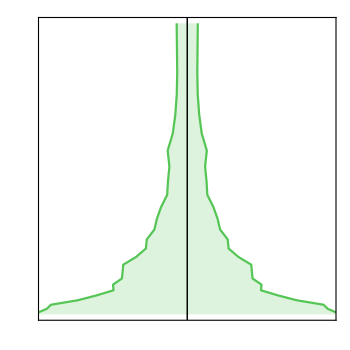

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}]

W="lq1";
{i,j}={1,2};
αβij={α,β,i,j};

(* observed limits: *)
EFTORDER = 2;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]
(*------------------*)

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;


(*-----------*)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]
(*-----------*)

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;


(*----- Plots ------*)

plot[W,ToString[αβij]]=ListPlot[{ 
		Append[  UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],{0,3000}],
		Append[  UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]
},
PlotStyle->{{Lighter[Darker[Green]],Dashed},{Lighter[Darker[Green]],Dashed},{Lighter[Darker[Green]]},{Lighter[Darker[Green]]}},
PlotRange->{{-0.3,0.3},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog->{Directive[{Thickness[0.003],Black}],Line[{{0,0},{0,3000}}]},
FrameTicks->{{Yticks[True,1.5],Yticks[False,1.75]},{Xticks[{0.1,0.2,0.3},True,1.5],Xticks[{0.1,0.2,0.3},False]} },
FrameLabel->{MaTeX["[\\mathcal{C}_{lq}^{(1)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}",Magnification->2.],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->2.]}]
```

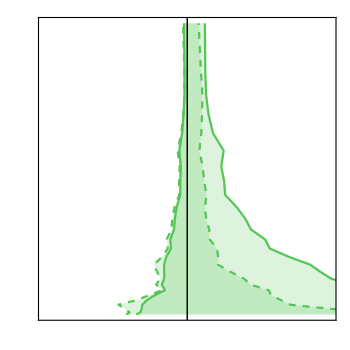

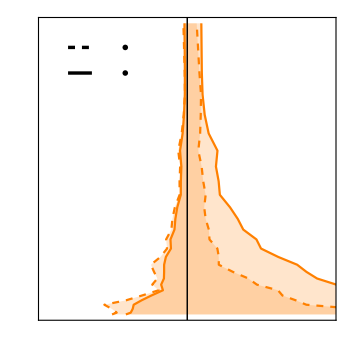

#### [C_lq^1]_αα23

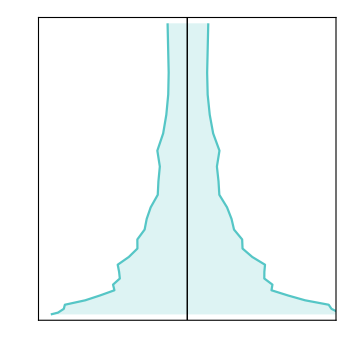

```mathematica
W="lq1";
{i,j}={2,3};
αβij={α,β,i,j};
(*
(*-----------*)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]
(*-----------*)

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;
*)
(*----- Plots ------*)

plot[W,ToString[αβij]]=ListPlot[{ Append[  UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{Lighter[Darker[Cyan]]},{Lighter[Darker[Cyan]]}},
PlotRange->{{-0.9,0.9},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog->{Directive[{Thickness[0.003],Black}],Line[{{0,0},{0,3000}}]},
FrameTicks->{{Yticks[False],Yticks[False]},{Xticks[{0.3,0.6,0.9},True,1.5],Xticks[{0.3,0.6,0.9},False]} },
FrameLabel->{MaTeX["[\\mathcal{C}_{lq}^{(1)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}",Magnification->2.],MaTeX[" ",Magnification->2.]} 
]
```

#### [C_lq^1]_αα13

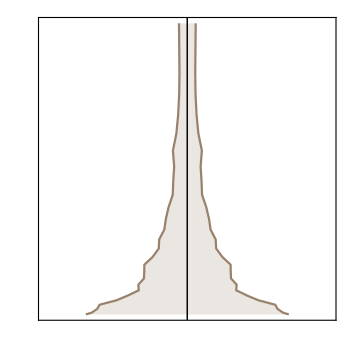

```mathematica
W="lq1";
{i,j}={1,3};
αβij={α,β,i,j};

(*(*-----------*)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]
(*-----------*)

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,αβij ]}]/.{WC[W,αβij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;
*)
(*----- Plots ------*)

plot[W,ToString[αβij]]=ListPlot[{ Append[  UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{Lighter[Darker[Brown]]},{Lighter[Darker[Brown]]}},
PlotRange->{{-0.9,0.9},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog->{Directive[{Thickness[0.003],Black}],Line[{{0,0},{0,3000}}]},
FrameTicks->{{Yticks[False],Yticks[False]},{Xticks[{0.3,0.6,0.9},True,1.5],Xticks[{0.3,0.6,0.9},False]} },
FrameLabel->{MaTeX["[\\mathcal{C}_{lq}^{(1)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}",Magnification->2.],MaTeX[" ",Magnification->2.]}]
```

#### [C_dW]_11

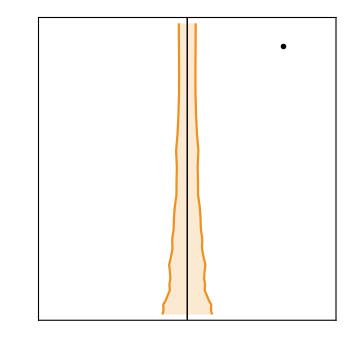

```mathematica
W="dW";
{i,j}={1,1};
ij={i,j};
αβij={α,β,i,j};

(*(*------------------*)
(* observed limits: *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]
(*-----------*)

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,ij ]}]/.{WC[W,ij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;
*)
(*----- Plots ------*)

plot[W,ToString[αβij]]=ListPlot[{  
                    Append[  UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.93,0.57,0.13]},{RGBColor[0.93,0.57,0.13]}},
PlotRange->{{-6,6},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog->{{Directive[{Thickness[0.003],Black}],Line[{{0,0},{0,3000}}],Directive[{Thickness[0.007],Black}]},,Text[MaTeX["pp\\to \mu\mu",Magnification->1.4],{4,2135},Center]},
FrameTicks->{{Yticks[True,1.3],Yticks[False,1.3]},{Xticks[{2,4,6},True,1.3],Xticks[{2,4,6},False]} },
FrameLabel->{MaTeX["[\\mathcal{C}_{dW}]_{"<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75],MaTeX[" M_{\\mathrm{cut}}~ \\mathrm{[GeV]}",Magnification->1.75]}
]
```

#### [C_dW]_22

Syntax::stresc: Unknown string escape \m.

Syntax::stresc: Unknown string escape \L.

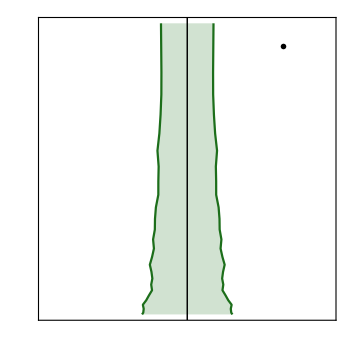

```mathematica
W="dW";
{i,j}={2,2};
ij={i,j};
αβij={α,β,i,j};

(*(* observed limits: *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]
(*-----------*)

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,ij ]}]/.{WC[W,ij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;
*)
(*----- Plots ------*)

plot[W,ToString[αβij]]=ListPlot[{  
                    Append[  UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.11,0.43,0.1]},{RGBColor[0.11,0.43,0.1]}},
PlotRange->{{-6,6},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog->{Directive[{Thickness[0.003],Black}],Line[{{0,0},{0,3000}}],Text[MaTeX["pp\\to \mu\mu",Magnification->1.4],{4.,2135},Center]},
FrameTicks->{{Yticks[False],Yticks[False]},{Xticks[{2,4,6},True,1.3],Xticks[{2,4,6},False,1.3]} },
FrameLabel->{MaTeX["[\\mathcal{C}_{dW}]_{"<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75]}
]
```

#### [C_dW]_33

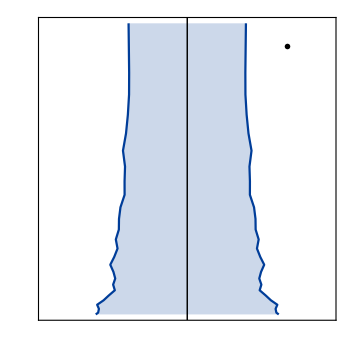

```mathematica
W="dW";
{i,j}={3,3};
ij={i,j};
αβij={α,β,i,j};
(*
(* observed limits: *)
EFTORDER = 4;
OPERATORDIM=6;
InitializeModel["SMEFT",EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Scale->Λ]
(*-----------*)

χ2[C6_]:=ChiSquareLHC[SEARCH,EFTorder->EFTORDER ,OperatorDimension->OPERATORDIM,Coefficients->{WC[W,ij ]}]/.{WC[W,ij]->C6}//Chop
UpperLims={};
LowerLims={};
χsqr=Re[χ2[C6]];
For[b=bmin,b≤bmax,b++,
χsqr1=Sum[χsqr[[i]],{i,1,b}];
{χsqrMin, bestfit}=NMinimize[χsqr1,C6];
res=RegionBounds@Region@ImplicitRegion[χsqr1<χsqrMin+InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First;
AppendTo[UpperLims,{res[[2]],DefaultBins[SEARCH][[b]]}];
AppendTo[LowerLims,{res[[1]],DefaultBins[SEARCH][[b]]}];
Print["coeff = C"<>W<>" "<>ToString[αβij], ", bin=",{DefaultBins[SEARCH][[b]],DefaultBins[SEARCH][[b+1]]},", limits=",res, ", {χ_min, best fit}=",{χsqrMin,bestfit}]
]
UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=UpperLims;
LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→"<>ToString[EFTORDER]]=LowerLims;
*)
(*----- Plots ------*)

plot[W,ToString[αβij]]=ListPlot[{  
                    Append[  UpperLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}],
                    Append[  LowerLimitsObs[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],{0,3000}]},
PlotStyle->{{RGBColor[0.,0.24,0.6]},{RGBColor[0.,0.24,0.6]}},
PlotRange->{{-6,6},{300,2289.7}}, Joined->True, Frame->True, AspectRatio->1,Filling ->Axis,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog->{Directive[{Thickness[0.003],Black}],Line[{{0,0},{0,3000}}],Text[MaTeX["pp\\to \mu\mu",Magnification->1.4],{4.2,2135},Center]},
FrameTicks->{{Yticks[False],Yticks[False]},{Xticks[{2,4,6},True,1.3],Xticks[{2,4,6},False,1.3]} },
FrameLabel->{MaTeX["[\\mathcal{C}_{dW}]_{"<>ToString[i]<>ToString[j]<>"}\\,/\Lambda^2\\ \\,[\\rm{TeV}^{-2}]",Magnification->1.75]}
]
```

#### C_lq^1 Plots

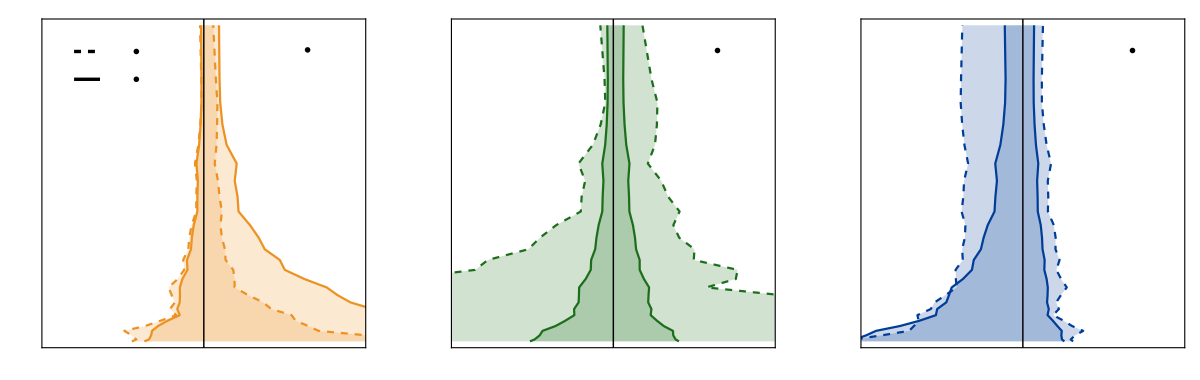

```mathematica
Clipped=GraphicsRow[{plot["lq1","{2, 2, 1, 1}"],plot["lq1","{2, 2, 2, 2}"],plot["lq1","{2, 2, 3, 3}"]},ImageSize->1200]
```

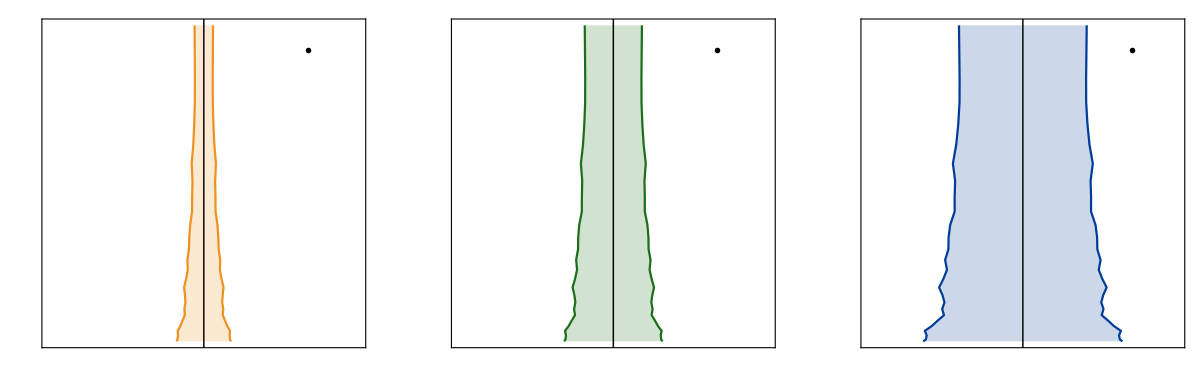

```mathematica
Clipped2=GraphicsRow[{plot["dW","{2, 2, 1, 1}"],plot["dW","{2, 2, 2, 2}"],plot["dW","{2, 2, 3, 3}"]},ImageSize->1200]
```

```mathematica
Export["Clq1_Clipped.pdf",Rasterize[Clipped,ImageResolution->400]];
Export["CdW_Clipped.pdf",Rasterize[Clipped2,ImageResolution->400]];
```

## Dimuon Jack-knife [OLD]

#### [C_lq^1]_αα11 Jack-knife analysis

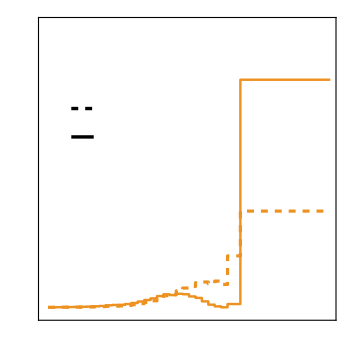

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}]

W="lq1";
{i,j}={1,1};
αβij={α,β,i,j};

(*{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]}=JacknifeEXPECTED["di-muon-CMS", 140,W,αβij,{{29,30},{31,32,33,34,35,36,37,38,39,40,41}}];
*)
(*----- Plots ------*)


JackPlot[W,αβij]=ListLogLinearPlot[{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                                          UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Dashed,Thickness[0.0065]},{RGBColor[0.93,0.57,0.13],Thickness[0.005]}},
PlotRange->{{200,7000},{0.99,1.4}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lq}^{(1)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
		{{Directive[{Thickness[0.007],Black,Dashed}],Line[{{Log[280],1.28},{Log[380],1.28}}]},{Directive[{Thickness[0.007],Black}],Line[{{Log[280],1.24},{Log[370],1.24}}]}},
                   Text[MaTeX["\\mathcal{O}(1/\\Lambda^2)",Magnification->1.2],Scaled[{0.3,0.7}],Center],
                   Text[MaTeX["\\mathcal{O}(1/\\Lambda^4)",Magnification->1.2],Scaled[{0.3,0.6}],Center],
Text[MaTeX["pp\\to \mu\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]
```

```mathematica
Directive[{Thickness[0.007],Black,Dashed}],
```

#### [C_lq^1]_αα22 Jack-knife analysis

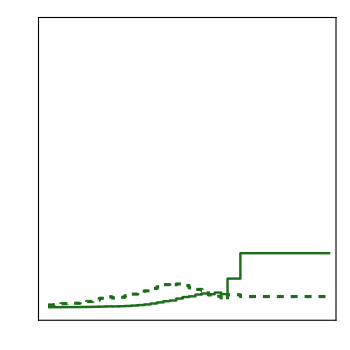

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}]

W="lq1";
{i,j}={2,2};
αβij={α,β,i,j};

(*{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]}=JacknifeEXPECTED["di-muon-CMS", 140,W,αβij,{{29,30},{31,32,33,34,35,36,37,38,39,40,41}}];
*)
(*----- Plots ------*)

JackPlot[W,αβij]=ListLogLinearPlot[{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                                          UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.11,0.43,0.1],Dashed,Thickness[0.0065]},{RGBColor[0.11,0.43,0.1],Thickness[0.005]}},
PlotRange->{{200,7000},{0.99,1.4}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lq}^{(1)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,Text[MaTeX["pp\\to \mu\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]
```

#### [C_lq^1]_αα33 Jack-knife analysis

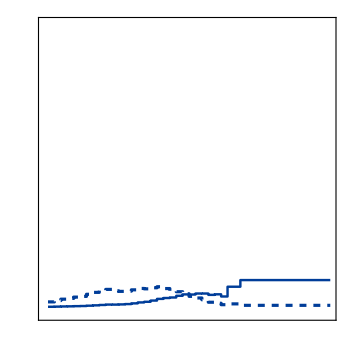

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}]

W="lq1";
{i,j}={3,3};
αβij={α,β,i,j};

(*
{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],
LowerLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]}=JacknifeEXPECTED["di-muon-CMS", 140,W,αβij,{{29,30},{31,32,33,34,35,36,37,38,39,40,41}}];
*)
(*----- Plots ------*)

JackPlot[W,αβij]=ListLogLinearPlot[{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                                                          UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.,0.24,0.6],Dashed,Thickness[0.0065]},{RGBColor[0.,0.24,0.6],Thickness[0.005]}},
PlotRange->{{200,7000},{0.99,1.4}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks1[ True,1.25],Xticks1[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lq}^{(1)}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,Text[MaTeX["pp\\to \mu\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]
```

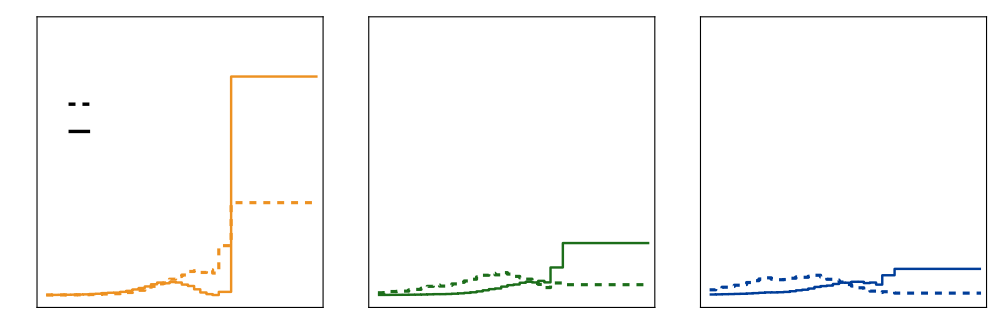

```mathematica
Jacknkife=GraphicsRow[{JackPlot["lq1",{2,2,1,1}],JackPlot["lq1",{2, 2, 2, 2}],JackPlot["lq1",{2, 2, 3, 3}]},ImageSize->1000,Spacings->-5]
```

```mathematica
Export["Clq1_Jack-knife.pdf",Rasterize[Jacknkife,ImageResolution->400]];
```

#### [C_ld]_αα11 Jack-knife analysis

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-2

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

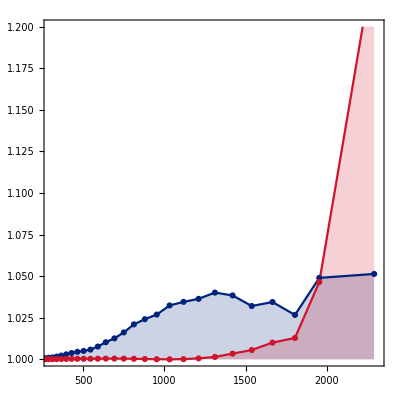

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}]

W="ld";
{i,j}={1,1};
αβij={α,β,i,j};

{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]}=JacknifeEXPECTED["di-muon-CMS", 140,W,αβij];

(*----- Plots ------*)

ListPlot[{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                  UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{azul},{rojo}},
PlotRange->{{300,2310},{1,1.2}}, Joined->True, Frame->True, AspectRatio->1,Mesh-> All,Filling->Axis,
Frame->{True,True,True,True},ImageSize->400,
FrameStyle->Directive[Black,Thickness[0.001]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->2],MaTeX["\\sigma_{\\rm Jack}/\\sigma_{\\rm tot}",Magnification->1.75]},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{ld}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}",Magnification->1.75],Scaled[{0.15,0.925}],Center] }]
```

#### [C_ld]_αα22 Jack-knife analysis

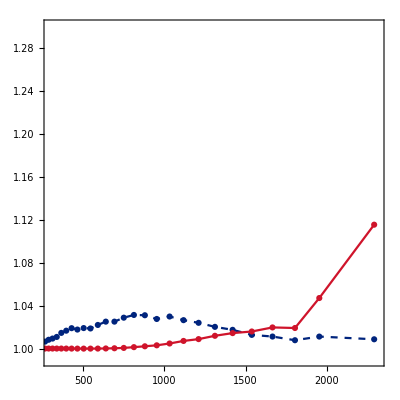

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}]

W="ld";
{i,j}={2,2};
αβij={α,β,i,j};

(*{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]}=JacknifeEXPECTED["di-muon-CMS", 140,W,αβij];
*)
(*----- Plots ------*)

ListPlot[{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                  UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{azul, Dashed},{rojo}},
PlotRange->{{300,2310},{0.99,1.3}}, Joined->True, Frame->True, AspectRatio->1, Mesh-> All,
Frame->{True,True,True,True},ImageSize->400,
FrameStyle->Directive[Black,Thickness[0.001]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->2],MaTeX["\\sigma_{\\rm Jack}/\\sigma_{\\rm tot}",Magnification->1.75]},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{ld}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}",Magnification->1.75],Scaled[{0.15,0.925}],Center] }]
```

#### [C_ld]_αα33 Jack-knife analysis

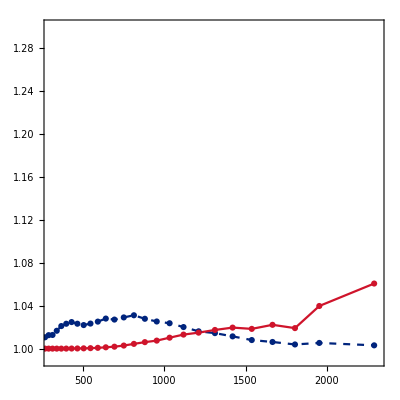

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}]

W="ld";
{i,j}={3,3};
αβij={α,β,i,j};
(*
{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]}=JacknifeEXPECTED["di-muon-CMS", 140,W,αβij];
*)
(*----- Plots ------*)

ListPlot[{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                  UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{azul, Dashed},{rojo}},
PlotRange->{{300,2310},{0.99,1.3}}, Joined->True, Frame->True, AspectRatio->1, Mesh-> All,
Frame->{True,True,True,True},ImageSize->400,
FrameStyle->Directive[Black,Thickness[0.001]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->2],MaTeX["\\sigma_{\\rm Jack}/\\sigma_{\\rm tot}",Magnification->1.75]},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{ld}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}",Magnification->1.75],Scaled[{0.15,0.925}],Center] }]
```

#### [C_lu]_αα11 Jack-knife analysis

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-2

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

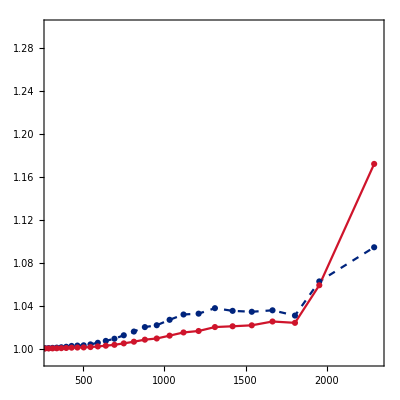

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}]

W="lu";
{i,j}={1,1};
αβij={α,β,i,j};

{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]}=JacknifeEXPECTED["di-muon-CMS", 140,W,αβij];

(*----- Plots ------*)

ListPlot[{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                  UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{azul, Dashed},{rojo}},
PlotRange->{{300,2310},{0.99,1.3}}, Joined->True, Frame->True, AspectRatio->1, Mesh-> All,
Frame->{True,True,True,True},ImageSize->400,
FrameStyle->Directive[Black,Thickness[0.001]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->2],MaTeX["\\sigma_{\\rm Jack}/\\sigma_{\\rm tot}",Magnification->1.75]},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lu}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}",Magnification->1.75],Scaled[{0.15,0.925}],Center] }]
```

#### [C_lu]_αα22 Jack-knife analysis

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-2

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

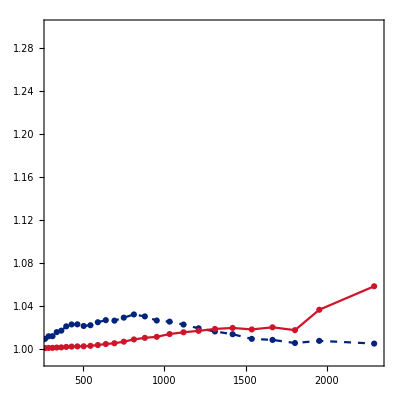

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}]

W="lu";
{i,j}={2,2};
αβij={α,β,i,j};

{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"],
UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]}=JacknifeEXPECTED["di-muon-CMS", 140,W,αβij];

(*----- Plots ------*)

ListPlot[{UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→2"],       
                  UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{azul, Dashed},{rojo}},
PlotRange->{{300,2310},{0.99,1.3}}, Joined->True, Frame->True, AspectRatio->1, Mesh-> All,
Frame->{True,True,True,True},ImageSize->400,
FrameStyle->Directive[Black,Thickness[0.001]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->2],MaTeX["\\sigma_{\\rm Jack}/\\sigma_{\\rm tot}",Magnification->1.75]},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{lu}]_{"<>ToString[α]<>ToString[β]<>ToString[i]<>ToString[j]<>"}",Magnification->1.75],Scaled[{0.15,0.925}],Center] }]
```

#### [C_dW]_αα11 Jack-knife analysis

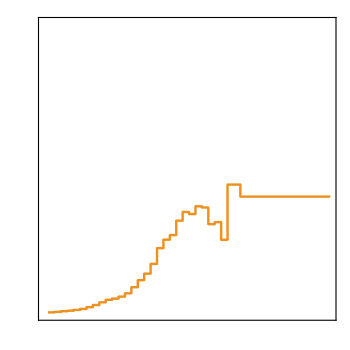

```mathematica
W="dW";
{i,j}={1,1};
ij={i,j};
αβij={α,β,i,j};

(*UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]=JacknifeEXPECTED["di-muon-CMS", 140,W,ij,{{29,30},{31,32,33,34,35,36,37,38,39,40,41}}];
*)

(*----- Plots ------*)

JackPlot[W,αβij]=ListLogLinearPlot[{ UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.93,0.57,0.13],Thickness[0.005]}},
PlotRange->{{200,7000},{1,1.05}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks2[ True,1.25],Xticks2[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{dW}]_{"<>ToString[i]<>ToString[j]<>"}",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to \mu\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]
```

#### [C_dW]_αα22 Jack-knife analysis

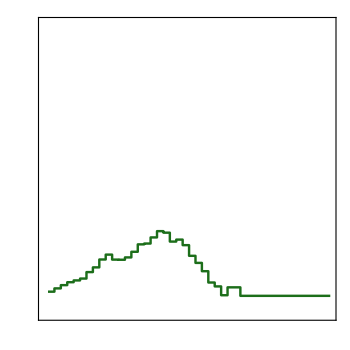

```mathematica
W="dW";
{i,j}={2,2};
ij={i,j};
αβij={α,β,i,j};

(*UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]=JacknifeEXPECTED["di-muon-CMS", 140,W,ij,{{29,30},{31,32,33,34,35,36,37,38,39,40,41}}];
*)
(*----- Plots ------*)

JackPlot[W,αβij]=ListLogLinearPlot[{ UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.11,0.43,0.1],Thickness[0.005]}},
PlotRange->{{200,7000},{1,1.05}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks2[ True,1.25],Xticks2[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{dW}]_{"<>ToString[i]<>ToString[j]<>"}",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to \mu\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]
```

#### [C_dW]_αα33 Jack-knife analysis

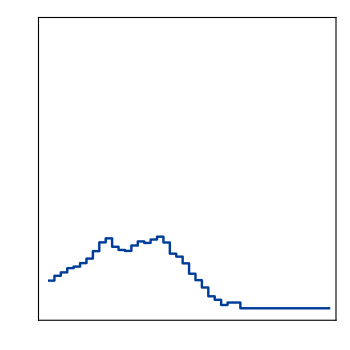

```mathematica
W="dW";
{i,j}={3,3};
ij={i,j};
αβij={α,β,i,j};

(*UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]=JacknifeEXPECTED["di-muon-CMS", 140,W,ij,{{29,30},{31,32,33,34,35,36,37,38,39,40,41}}];
*)

(*----- Plots ------*)

JackPlot[W,αβij]=ListLogLinearPlot[{ UpperLimitsExpJackRatio[W,ToString[αβij],ToString[IntegerPart[Λ/1000]]<>"TEV","EFTorder→4"]},
PlotStyle->{{RGBColor[0.,0.24,0.6],Thickness[0.005]}},
PlotRange->{{200,7000},{1,1.05}}, Frame->True, AspectRatio->1,Joined->True,
Frame->{True,True,True,True},ImageSize->350,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{MaTeX["m_{\\mu\\mu}\\ \\rm[GeV]",Magnification->1.75],MaTeX["R_{\\rm Jack}",Magnification->1.75]},
FrameTicks->{{Xticks2[ True,1.25],Xticks2[False,1.25]} ,{Yticks1[True,1.25],Yticks1[False,1.25]}},
Epilog->{ Text[MaTeX["[\\mathcal{C}_{dW}]_{"<>ToString[i]<>ToString[j]<>"}",Magnification->1.75],Scaled[{0.225,0.9}],Center] ,
Text[MaTeX["pp\\to \mu\mu",Magnification->1.4],Scaled[{0.82,0.9}],Center]}]
```

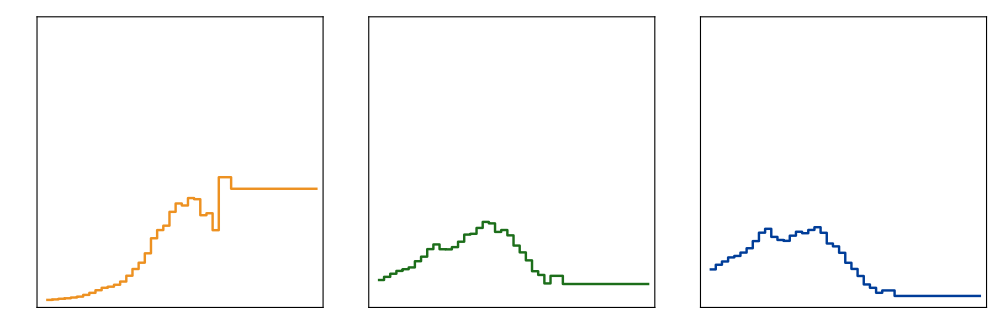

```mathematica
Jacknkife2=GraphicsRow[{JackPlot["dW",{2,2,1,1}],JackPlot["dW",{2, 2, 2, 2}],JackPlot["dW",{2, 2, 3, 3}]},ImageSize->1000,Spacings->-5]
```

```mathematica
Export["CdW_Jack-knife.pdf",Rasterize[Jacknkife2,ImageResolution->400]];
```

## χ^2 check ups [OLD]

22

```mathematica
LHCSearch["mono-tau-ATLAS"]
DefineParameters["Wolfenstein"->{0,0,0,0}]
```

<|INFO→<|ARXIV→[ATLAS-CONF-2021-025](https://cds.cern.ch/record/2773301/),SOURCE→[Figure 5](https://atlas.web.cern.ch/Atlas/GROUPS/PHYSICS/CONFNOTES/ATLAS-CONF-2021-025/fig_05.pdf),DESCRIPTION→Final states with a tau lepton and missing transverse momentum. The tau lepton is reconstructed in hadronic decay modes.,EXPERIMENT→ATLAS,PROCESS→p p > τ ν,FINALSTATE→{e[3],ν} | {ν,e[3]},OBSERVABLE→m_T,LUMINOSITY→139,CMENERGY→13000,BINS→<|OBSERVABLE→{200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1750,2000,10000},MLL→{400,10000},PT→{200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1750,2000,10000}|>|>,DATA→{2936,10560,3049,979,400,187,95,55,22,13,10,4,1,7,0,1},BACKGROUND→{2940.33,10575.8,3018.15,1007.49,403.793,184.418,93.503,48.663,25.996,14.632,8.236,5.014,3.133,3.971,1.511,1.215},ERROR-BKG→{141.996,541.685,181.089,69.296,28.955,14.304,7.8,4.202,3.158,2.505,1.724,1.152,0.72,0.971,0.409,0.389},DEFAULT-BINNING→{{12,13,14,15,16}}|>

```mathematica
(*--------------------------------------------------------------------*)
Λ=1000;
{α,β}={2,2};
SEARCH="di-muon-CMS";
LUMINOSITY=141;
{bmin,bmax}={5,30}; 
(*--------------------------------------------------------------------*)

LHCSearch[SEARCH]
DefaultBins["di-muon-CMS"]={209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2289.7,7000};
```

<|INFO→<|ARXIV→[arXiv:2103.02708](https://arxiv.org/abs/2103.02708),SOURCE→[hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4),DESCRIPTION→The invariant mass spectra of dimuon events.,EXPERIMENT→CMS,PROCESS→p p > μ^- μ^+,FINALSTATE→{e[2],e[2]},OBSERVABLE→m_μμ,LUMINOSITY→140,CMENERGY→13000,BINS→<|OBSERVABLE→{209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000},MLL→{200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000},PT→{0,∞}|>|>,DATA→{49128,41800,32648,26435,21188,16797,13170,10490,7650,6128,4613,3457,2635,1979,1478,1016,759,574,389,295,202,132,107,71,59,27,18,13,11,5,5,4,2,1,1,0,0,0,0,0,0},BACKGROUND→{50469.3,41839.9,32989.,26921.1,21531.6,16912.7,13098.5,10333.8,7769.34,6219.57,4759.3,3379.58,2662.33,1926.39,1417.98,1048.48,781.922,553.886,403.303,292.15,206.536,148.227,105.5,71.9137,49.5856,35.7306,22.9439,16.5921,9.79576,6.26511,3.93946,2.75556,1.43541,0.856615,0.536371,0.271383,0.139182,0.110295,0.0306152,0.00583208,0.00094739},ERROR-BKG→{1391.01,1108.09,905.112,739.993,613.787,503.444,396.767,311.091,242.262,193.881,167.365,140.151,112.668,85.8949,64.8728,50.746,37.1769,26.5778,20.075,16.0183,10.9671,7.77697,5.86035,4.02962,2.83474,2.4225,1.34904,1.13735,0.622781,0.441341,0.27607,0.253813,0.110243,0.0698684,0.056433,0.0338829,0.0167852,0.0198925,0.0064995,0.00203296,0.00051924},DEFAULT-BINNING→{{29,30},{31,32,33,34,35,36,37,38,39,40,41}}|>

{288.34,2289.7}

```mathematica
W="lq1";
αβij={2,2,2,2};
bin=-1;
ChiSquareLHC[SEARCH,EFTorder->2 ,OperatorDimension->6,Coefficients->{WC[W,αβij]},Luminosity->140] /.{WC[W,αβij]->c}//Chop//Simplify
ChiSquareLHC[SEARCH,EFTorder->4 ,OperatorDimension->6,Coefficients->{WC[W,αβij]},Luminosity->140]/.{WC[W,αβij]->c}//Chop//Simplify
```

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{0.00241478 c^2,0.00154404 c^2,0.00245027 c^2,0.00179775 c^2,0.00100024 c^2,0.00139166 c^2,0.000453909 c^2,0.0000826602 c^2,0.0000302124 c^2,0.000202239 c^2,0.00186834 c^2,0.00290608 c^2,0.00530194 c^2,0.0115427 c^2,0.0233164 c^2,0.0364091 c^2,0.0570473 c^2,0.094936 c^2,0.128607 c^2,0.16041 c^2,0.217089 c^2,0.281016 c^2,0.325962 c^2,0.401403 c^2,0.422133 c^2,0.416014 c^2,0.473799 c^2,0.428614 c^2,0.893612 c^2,1.43004 c^2}

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{0.000881342 c^2 (1.65526+1. c)^2,0.00159776 c^2 (0.983043+1. c)^2,0.00271379 c^2 (0.950208+1. c)^2,0.00441083 c^2 (0.638417+1. c)^2,0.00689305 c^2 (0.380931+1. c)^2,0.0108207 c^2 (0.358624+1. c)^2,0.018655 c^2 (0.155987+1. c)^2,0.0313524 c^2 (0.0513467+1. c)^2,0.0509445 c^2 (0.0243525+1. c)^2,0.0786496 (0.0507089-1. c)^2 c^2,0.104116 (0.133958-1. c)^2 c^2,0.144077 (0.142022-1. c)^2 c^2,0.216333 (0.156551-1. c)^2 c^2,0.338664 (0.184616-1. c)^2 c^2,0.529178 (0.209908-1. c)^2 c^2,0.773013 (0.217026-1. c)^2 c^2,1.21579 (0.216615-1. c)^2 c^2,1.87069 (0.225276-1. c)^2 c^2,2.59704 (0.222532-1. c)^2 c^2,3.35065 (0.218802-1. c)^2 c^2,4.84085 (0.211767-1. c)^2 c^2,6.49688 (0.207976-1. c)^2 c^2,7.85555 (0.203702-1. c)^2 c^2,10.3922 (0.196534-1. c)^2 c^2,12.3504 (0.184878-1. c)^2 c^2,13.3898 (0.176266-1. c)^2 c^2,16.6674 (0.168602-1. c)^2 c^2,16.8717 (0.159387-1. c)^2 c^2,41.0709 (0.147505-1. c)^2 c^2,105.076 (0.11666-1. c)^2 c^2}

```mathematica
1/0.11666007664589328
```

8.57191

```mathematica
1.43 c^2(1- 8.572c)^2
```

```mathematica
χ2lin["lq1","2222" ,][c_]:=1.43 c^2
χ2quad["lq1","2222" ][c_,δ_]:=χ2lin["lq1","2222" ][c](1-δ c)^2
```

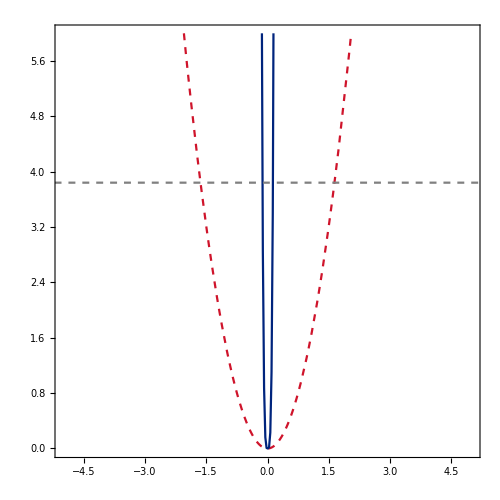

```mathematica
factor=0;
Plot[{χ2lin["lq1","2222" ][c],χ2quad["lq1","2222" ][c,100],InverseCDF[ChiSquareDistribution[1],0.95]},{c,-50,50},
PlotStyle->{{rojo,Dashed},{azul},{Gray,Dashed}},
PlotRange->{{-5,5},{-0.01,6}},  Frame->True, AspectRatio->1,
Frame->{True,True,True,True},ImageSize->500,
FrameStyle->Directive[Black,Thickness[0.003]],
(*FrameTicks->{{Yticks[True,1.5],Yticks[False,1.5]},{Xticks[{0.2,0.4,0.6},True,1.5],Xticks[{0.2,0.4,0.6},False]} },*)
FrameLabel->{MaTeX["C",Magnification->2.5],MaTeX["\\chi^2",Magnification->2.5]}
]
```

## Dimension-8 marginalizaiton

```mathematica
Dim8Limits[Current_,Search_, Λ0_,αβij0_,XY0_,Cmax0_]:=Module[{CURRENT=Current, SEARCH=Search,Λ=Λ0,αβij=αβij0 , XY=XY0,Cmax=Cmax0,C6,Results,Limits,ΛNP}, 

vev=1/(10^3 √(√2 GF))/.{GF-> 1.16 10^-5} (*TeV*);

If[CURRENT=="NC",
χ2=Total[ChiSquareLHC[search,FF->True, EFTorder->4,OperatorDimension->8,Coefficients-> {
FF[Vector,{"ZBoson",SM},XY,αβij],
FF[Vector,{"Photon",SM},XY,αβij],
FF[Vector,{"regular",{0,0}},XY,αβij],
FF[Vector,{"regular",{1,0}},XY,αβij],
FF[Vector,{"regular",{0,1}},XY,αβij]}]]/.SubstitutionRulesMediators["ZBoson"]/.SubstitutionRulesMediators["Photon"]/.ReplaceConstants[]//Chop,
χ2=Total[ChiSquareLHC[search,FF->True, EFTorder->4,OperatorDimension->8,Coefficients-> {
FF[Vector,{"WBoson",SM},XY,αβij],
FF[Vector,{"regular",{0,0}},XY,αβij],
FF[Vector,{"regular",{1,0}},XY,αβij],
FF[Vector,{"regular",{0,1}},XY,αβij]}]]/.SubstitutionRulesMediators["WBoson"]/.ReplaceConstants[]//Chop;
];

χ2FF[Λ_,C6lq13_,C8lq13_,C8lq24_]:=χ2/.{FF[Vector,{"regular",{0,0}},XY,αβij]->(vev/Λ)^2 C6lq13,FF[Vector,{"regular",{1,0}},XY,αβij]->(vev/Λ)^4(C8lq13+C8lq24),FF[Vector,{"regular",{0,1}},XY,αβij]->(vev/Λ)^4 2*C8lq24}//Chop;
Results={};
For[k=1,k≤Length[Λ],k++,
ΛNP=Λ[[k]];
{χ2min ,bestfit}=NMinimize[{Re[χ2FF[ΛNP,C6,0,0]],-Cmax<C6<Cmax},{C6},MaxIterations->500];
{χ2min1 ,bestfit1}=NMinimize[{Re[χ2FF[ΛNP,C6,C6,0]],-Cmax<C6<Cmax},{C6},MaxIterations->500];
{χ2min2 ,bestfit2}=NMinimize[{Re[χ2FF[ΛNP,C6,C8lq13,C8lq24]],-Cmax<C6<Cmax,-Cmax<C8lq13<Cmax,-Cmax<C8lq24<Cmax},{C6,C8lq13,C8lq24},MaxIterations->500];
grid=Table[{C6,First[NMinimize[{Re[χ2FF[ΛNP,C6,C8lq13,C8lq24]],-Cmax<C8lq13<Cmax,-Cmax<C8lq24<Cmax},{C8lq13,C8lq24},MaxIterations->500]]},{C6,-Cmax,Cmax,Cmax/50.}];
FVLL00margin =Interpolation[grid];
Limits={ΛNP,
               RegionBounds@Region@ImplicitRegion[Re[χ2FF[ ΛNP,C6,0,0]]<χ2min +InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First,
	      RegionBounds@Region@ImplicitRegion[Re[χ2FF[ ΛNP,C6,C6,0]]<χ2min1 +InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First,
	     RegionBounds@Region@ImplicitRegion[FVLL00margin[C6]<χ2min2 +InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First};
AppendTo[Results,Limits];
];
Results
]


Dim8LimitsEXPECTED[Current_,Search_, Λ0_,αβij0_,XY0_,Cmax0_]:=Module[{CURRENT=Current, SEARCH=Search,Λ=Λ0,αβij=αβij0 , XY=XY0,Cmax=Cmax0,C6,Results,Limits,ΛNP}, 

vev=1/(10^3 √(√2 GF))/.{GF-> 1.16 10^-5} (*TeV*);

If[CURRENT=="NC",
χ2=Total[ChiSquareLHC[search,FF->True, EFTorder->4,OperatorDimension->8,Coefficients-> {
FF[Vector,{ZBoson,SM},XY,αβij],
FF[Vector,{Photon,SM},XY,αβij],
FF[Vector,{"regular",{0,0}},XY,αβij],
FF[Vector,{"regular",{1,0}},XY,αβij],
FF[Vector,{"regular",{0,1}},XY,αβij]},
     Luminosity->141]]/.SubstitutionRulesMediators[ZBoson]/.SubstitutionRulesMediators[Photon]/.ReplaceConstants[]//Chop,
χ2=Total[ChiSquareLHC[search,FF->True, EFTorder->4,OperatorDimension->8,Coefficients-> {
FF[Vector,{WBoson,SM},XY,αβij],
FF[Vector,{"regular",{0,0}},XY,αβij],
FF[Vector,{"regular",{1,0}},XY,αβij],
FF[Vector,{"regular",{0,1}},XY,αβij]},
     Luminosity->141]]/.SubstitutionRulesMediators[WBoson]/.ReplaceConstants[]//Chop;
];

χ2FF[Λ_,C6lq13_,C8lq13_,C8lq24_]:=χ2/.{FF[Vector,{"regular",{0,0}},XY,αβij]->(vev/Λ)^2 C6lq13,FF[Vector,{"regular",{1,0}},XY,αβij]->(vev/Λ)^4(C8lq13+C8lq24),FF[Vector,{"regular",{0,1}},XY,αβij]->(vev/Λ)^4 2*C8lq24}//Chop;
Results={};
For[k=1,k≤Length[Λ],k++,
ΛNP=Λ[[k]];
{χ2min ,bestfit}=NMinimize[{Re[χ2FF[ΛNP,C6,0,0]],-Cmax<C6<Cmax},{C6},MaxIterations->500];
{χ2min1 ,bestfit1}=NMinimize[{Re[χ2FF[ΛNP,C6,C6,0]],-Cmax<C6<Cmax},{C6},MaxIterations->500];
{χ2min2 ,bestfit2}=NMinimize[{Re[χ2FF[ΛNP,C6,C8lq13,C8lq24]],-Cmax<C6<Cmax,-Cmax<C8lq13<Cmax,-Cmax<C8lq24<Cmax},{C6,C8lq13,C8lq24},MaxIterations->500];
grid=Table[{C6,First[NMinimize[{Re[χ2FF[ΛNP,C6,C8lq13,C8lq24]],(*-Cmax<C6<Cmax,*)-Cmax<C8lq13<Cmax,-Cmax<C8lq24<Cmax},{C8lq13,C8lq24},MaxIterations->500]]},{C6,-Cmax,Cmax,Cmax/50.}];
FVLL00margin =Interpolation[grid];
Limits={ΛNP,
               RegionBounds@Region@ImplicitRegion[Re[χ2FF[ ΛNP,C6,0,0]]<χ2min +InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First,
	      RegionBounds@Region@ImplicitRegion[Re[χ2FF[ ΛNP,C6,C6,0]]<χ2min1 +InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First,
	     RegionBounds@Region@ImplicitRegion[FVLL00margin[C6]<χ2min2 +InverseCDF[ChiSquareDistribution[1],0.95],{C6}]//First};
AppendTo[Results,Limits];
];
Results
]
```

#### ee

```mathematica
search="di-electron-CMS"
Lim[search,e[1],e[1],d[1],d[1]]=Dim8Limits["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[1],e[1],d[1],d[1]},{Left,Left},4π]
Lim[search,e[1],e[1],d[2],d[2]]=Dim8Limits["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[1],e[1],d[2],d[2]},{Left,Left},4π]
Lim[search,e[1],e[1],d[3],d[3]]=Dim8Limits["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[1],e[1],d[3],d[3]},{Left,Left},4π]
Lim[search,e[1],e[1],u[1],u[1]]=Dim8Limits["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[1],e[1],u[1],u[1]},{Left,Left},4π]
Lim[search,e[1],e[1],u[2],u[2]]=Dim8Limits["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[1],e[1],u[2],u[2]},{Left,Left},4π]
```

di-electron-CMS

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

$Aborted

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

$Aborted

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

$Aborted

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

$Aborted

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

$Aborted

#### μμ

```mathematica
search="di-muon-CMS"
Lim[search,e[2],e[2],d[1],d[1]]=Dim8Limits["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[2],e[2],d[1],d[1]},{Left,Left},4π]
Lim[search,e[2],e[2],d[2],d[2]]=Dim8Limits["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[2],e[2],d[2],d[2]},{Left,Left},4π]
Lim[search,e[2],e[2],d[3],d[3]]=Dim8Limits["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[2],e[2],d[3],d[3]},{Left,Left},4π]
Lim[search,e[2],e[2],u[1],u[1]]=Dim8Limits["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[2],e[2],u[1],u[1]},{Left,Left},4π]
Lim[search,e[2],e[2],u[2],u[2]]=Dim8Limits["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[2],e[2],u[2],u[2]},{Left,Left},4π]
```

di-muon-CMS

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-0.152548,0.0276698},{-0.0632589,0.0212582},{-0.138859,0.143662}},{3.,{-0.343234,0.062257},{-0.225754,0.0555966},{-0.316873,0.221706}},{4.,{-0.610194,0.110679},{-0.502172,0.104019},{-0.593846,0.253014}},{5.,{-0.953428,0.172936},{-0.863873,0.166282},{-0.94991,0.335833}},{6.,{-1.37294,0.249028},{-1.29654,0.242374},{-1.37547,0.444962}},{7.,{-1.86872,0.338955},{-1.80064,0.332297},{-1.87522,0.565233}},{8.,{-2.44078,0.442716},{-2.3781,0.436054},{-2.45095,0.711379}}}

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-0.616766,0.23969},{-0.720503,0.192044},{-1.03443,0.605115}},{3.,{-1.38772,0.539302},{-1.48813,0.487429},{-2.28407,1.12533}},{4.,{-2.46707,0.95876},{-2.56635,0.905515},{-3.09464,1.52299}},{5.,{-3.85479,1.49806},{-3.95356,1.4442},{-4.26124,1.86332}},{6.,{-5.5509,2.15721},{-5.6494,2.10302},{-5.82089,2.39622}},{7.,{-7.55539,2.9362},{-7.65372,2.88181},{-7.74949,3.10697}},{8.,{-9.86826,3.83504},{-9.96649,3.78052},{-10.0153,3.96398}}}

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-1.3873,0.859305},{-1.48891,0.783001},{-2.33536,1.77398}},{3.,{-3.12142,1.93344},{-3.22174,1.85584},{-3.564,2.35002}},{4.,{-5.5492,3.43722},{-5.64907,3.35919},{-5.78049,3.65121}},{5.,{-8.67062,5.37066},{-8.77029,5.29242},{-8.81529,5.50391}},{6.,{-12.4857,7.73375},{-12.5852,7.6554},{-12.5853,7.82537}},{7.,{-16.9944,10.5265},{-17.0939,10.4481},{-17.0964,10.5935}},{8.,{-22.1968,13.7489},{-22.2962,13.6704},{-22.5057,13.8003}}}

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-0.0143758,0.0505128},{-0.0104923,0.0217406},{-0.0721332,0.0701584}},{3.,{-0.0323456,0.113654},{-0.0283607,0.0725142},{-0.178246,0.158393}},{4.,{-0.0575034,0.202051},{-0.0536507,0.154104},{-0.178214,0.283444}},{5.,{-0.0898489,0.315705},{-0.0861124,0.264026},{-0.182226,0.465247}},{6.,{-0.129382,0.454615},{-0.125727,0.40077},{-0.209649,0.673797}},{7.,{-0.176104,0.618781},{-0.172504,0.563595},{-0.254519,0.920784}},{8.,{-0.230013,0.808204},{-0.226453,0.752137},{-0.310384,1.19583}}}

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-0.400962,0.937548},{-0.333861,1.0624},{-0.992261,1.73497}},{3.,{-0.902165,2.10948},{-0.831376,2.23133},{-1.66969,2.94779}},{4.,{-1.60385,3.75019},{-1.53184,3.87101},{-2.05606,4.24163}},{5.,{-2.50601,5.85968},{-2.43346,5.98003},{-2.77181,6.15351}},{6.,{-3.60866,8.43794},{-3.53581,8.55804},{-3.78722,8.63644}},{7.,{-4.91178,11.485},{-4.83876,11.6049},{-5.0411,11.6291}},{8.,{-6.41539,15.0008},{-6.34225,15.1206},{-6.51371,15.1177}}}

#### ττ

```mathematica
search="di-tau-ATLAS"
Lim[search,e[3],e[3],d[1],d[1]]=Dim8Limits["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[3],e[3],d[1],d[1]},{Left,Left},4π]
Lim[search,e[3],e[3],d[2],d[2]]=Dim8Limits["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[3],e[3],d[2],d[2]},{Left,Left},4π]
Lim[search,e[3],e[3],d[3],d[3]]=Dim8Limits["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[3],e[3],d[3],d[3]},{Left,Left},4π]
Lim[search,e[3],e[3],u[1],u[1]]=Dim8Limits["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[3],e[3],u[1],u[1]},{Left,Left},4π]
Lim[search,e[3],e[3],u[2],u[2]]=Dim8Limits["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[3],e[3],u[2],u[2]},{Left,Left},4π]
```

di-tau-ATLAS

PROCESS | : | pp → τ^-τ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:2002.12223](https://arxiv.org/abs/2002.12223)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.93071.v4/t3)
OBSERVABLE | : | m_T^tot
BINNING m_T^tot [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
EVENTS OBSERVED | : | {1167, 1568, 1409, 1455, 1292, 650, 377, 288, 92, 57, 27, 14, 11, 13}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-0.566886,0.0258966},{-0.700635,0.0467455},{-0.815157,0.201238}},{3.,{-1.27549,0.0582666},{-1.40348,0.0711393},{-1.63675,0.206316}},{4.,{-2.26755,0.103585},{-2.39253,0.111877},{-2.78371,0.292845}},{5.,{-3.54304,0.161852},{-3.66671,0.167997},{-3.99374,0.429337}},{6.,{-5.10198,0.233066},{-5.22494,0.238046},{-5.44119,0.48584}},{7.,{-6.94436,0.317229},{-7.06691,0.321506},{-7.20135,0.517425}},{8.,{-9.07018,0.41434},{-9.19246,0.418162},{-9.26876,0.570961}}}

PROCESS | : | pp → τ^-τ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:2002.12223](https://arxiv.org/abs/2002.12223)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.93071.v4/t3)
OBSERVABLE | : | m_T^tot
BINNING m_T^tot [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
EVENTS OBSERVED | : | {1167, 1568, 1409, 1455, 1292, 650, 377, 288, 92, 57, 27, 14, 11, 13}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-1.35341,0.484126},{-1.45855,0.420824},{-2.24356,1.2403}},{3.,{-3.04518,1.08928},{-3.14884,1.02448},{-3.45682,1.43945}},{4.,{-5.41366,1.93651},{-5.51681,1.87119},{-5.62762,2.11267}},{5.,{-8.45884,3.02579},{-8.56176,2.96025},{-8.59241,3.13489}},{6.,{-12.1807,4.35714},{-12.2835,4.29147},{-12.2726,4.43201}},{7.,{-16.5793,5.93055},{-16.682,5.86481},{-16.6761,5.98528}},{8.,{-21.6546,7.74602},{-21.7573,7.68023},{-22.0067,7.78782}}}

PROCESS | : | pp → τ^-τ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:2002.12223](https://arxiv.org/abs/2002.12223)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.93071.v4/t3)
OBSERVABLE | : | m_T^tot
BINNING m_T^tot [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
EVENTS OBSERVED | : | {1167, 1568, 1409, 1455, 1292, 650, 377, 288, 92, 57, 27, 14, 11, 13}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-3.19101,2.14152},{-3.28975,2.05754},{-3.47406,2.41148}},{3.,{-7.17976,4.81843},{-7.27808,4.73403},{-7.29641,4.92871}},{4.,{-12.764,8.56609},{-12.8622,8.48155},{-12.8288,8.62726}},{5.,{-19.9438,13.3845},{-20.0419,13.2999},{-20.0727,13.4236}},{6.,{-28.719,19.2737},{-28.8171,19.1891},{-29.4019,19.3218}},{7.,{-39.0898,26.2337},{-39.1879,26.149},{-41.1144,26.3844}},{8.,{-51.0561,34.2644},{-51.1541,34.1797},{-55.3761,34.6462}}}

PROCESS | : | pp → τ^-τ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:2002.12223](https://arxiv.org/abs/2002.12223)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.93071.v4/t3)
OBSERVABLE | : | m_T^tot
BINNING m_T^tot [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
EVENTS OBSERVED | : | {1167, 1568, 1409, 1455, 1292, 650, 377, 288, 92, 57, 27, 14, 11, 13}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-0.0244304,0.362591},{-0.0285659,0.163341},{-0.192824,0.521376}},{3.,{-0.0549684,0.81583},{-0.0621076,0.528925},{-0.123022,0.91009}},{4.,{-0.0977216,1.45036},{-0.106398,1.13622},{-0.114407,1.52909}},{5.,{-0.15269,2.26619},{-0.162198,1.96098},{-0.134232,2.35115}},{6.,{-0.219873,3.26332},{-0.229869,2.97435},{-0.172966,3.36851}},{7.,{-0.299272,4.44174},{-0.309574,4.16636},{-0.290288,4.60145}},{8.,{-0.390886,5.80146},{-0.401393,5.53608},{-0.406165,5.98207}}}

PROCESS | : | pp → τ^-τ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:2002.12223](https://arxiv.org/abs/2002.12223)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.93071.v4/t3)
OBSERVABLE | : | m_T^tot
BINNING m_T^tot [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
EVENTS OBSERVED | : | {1167, 1568, 1409, 1455, 1292, 650, 377, 288, 92, 57, 27, 14, 11, 13}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-0.817541,1.98106},{-0.732235,2.10927},{-1.56314,2.77105}},{3.,{-1.83947,4.45739},{-1.75278,4.58424},{-2.10575,4.75858}},{4.,{-3.27016,7.92425},{-3.18301,8.05063},{-3.41062,8.08499}},{5.,{-5.10963,12.3816},{-5.02226,12.5078},{-5.19796,12.483}},{6.,{-7.35787,17.8296},{-7.27038,17.9556},{-7.41882,17.9559}},{7.,{-10.0149,24.268},{-9.92732,24.394},{-10.0595,24.8237}},{8.,{-13.0807,31.697},{-12.9931,31.8229},{-13.1148,33.4793}}}

#### eν

```mathematica
search="mono-electron-ATLAS"
Lim[search,e[1],ν[1],u[1],d[1]]=Dim8Limits["CC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[1],ν[1],u[1],d[1]},{Left,Left},4π]
Lim[search,e[1],ν[1],u[2],d[2]]=Dim8Limits["CC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[1],ν[1],u[2],d[2]},{Left,Left},4π]
```

mono-electron-ATLAS

PROCESS | : | pp → e^-ν̄
pp → νe^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:1906.05609](https://arxiv.org/abs/1906.05609)
SOURCE | : | [hepdata: Table 1](https://doi.org/10.17182/hepdata.90193.v1/t1)
OBSERVABLE | : | m_T
BINNING m_T [GeV] | : | {207.519,221.857,237.186,253.575,271.095,289.827,309.852,331.261,354.15,378.62,404.781,432.749,462.65,494.616,528.792,565.329,604.39,646.15,690.796,738.526,789.555,844.109,902.433,964.786,1031.45,1102.72,1178.91,1260.36,1347.45,1440.55,1540.09,1646.5,1760.26,1881.89,2011.92,2150.93,2299.55,2458.43,2628.3,2809.9,3004.05,3211.62,3433.52,3670.76,3924.39,4195.55,4485.44,4795.36,5126.69,5480.92,5859.63,6264.5,6697.34,7160.09,7654.82,8183.73,8749.18,9353.71,10000}
EVENTS OBSERVED | : | {140146, 107018, 82526, 62571, 48409, 37169, 28815, 21919, 16774, 12897, 9953, 7535, 5773, 4547, 3389, 2610, 2012, 1457, 1127, 843, 623, 518, 337, 294, 232, 141, 94, 85, 62, 39, 19, 16, 16, 6, 9, 7, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {200,10000}
BINNING p_T [GeV] | : | {100,200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}

{{2.,{-0.0615817,0.0414282},{-0.0458295,0.0291524},{-0.203656,0.258298}},{3.,{-0.138559,0.0932134},{-0.121036,0.0788725},{-0.256293,0.305469}},{4.,{-0.246327,0.165713},{-0.228216,0.150514},{-0.352919,0.421941}},{5.,{-0.384885,0.258926},{-0.366523,0.243304},{-0.507624,0.606816}},{6.,{-0.554235,0.372854},{-0.535743,0.356994},{-0.707991,0.835145}},{7.,{-0.754375,0.507495},{-0.735808,0.49149},{-0.950864,0.928229}},{8.,{-0.985306,0.662851},{-0.966692,0.64675},{-1.19856,1.00436}}}

PROCESS | : | pp → e^-ν̄
pp → νe^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:1906.05609](https://arxiv.org/abs/1906.05609)
SOURCE | : | [hepdata: Table 1](https://doi.org/10.17182/hepdata.90193.v1/t1)
OBSERVABLE | : | m_T
BINNING m_T [GeV] | : | {207.519,221.857,237.186,253.575,271.095,289.827,309.852,331.261,354.15,378.62,404.781,432.749,462.65,494.616,528.792,565.329,604.39,646.15,690.796,738.526,789.555,844.109,902.433,964.786,1031.45,1102.72,1178.91,1260.36,1347.45,1440.55,1540.09,1646.5,1760.26,1881.89,2011.92,2150.93,2299.55,2458.43,2628.3,2809.9,3004.05,3211.62,3433.52,3670.76,3924.39,4195.55,4485.44,4795.36,5126.69,5480.92,5859.63,6264.5,6697.34,7160.09,7654.82,8183.73,8749.18,9353.71,10000}
EVENTS OBSERVED | : | {140146, 107018, 82526, 62571, 48409, 37169, 28815, 21919, 16774, 12897, 9953, 7535, 5773, 4547, 3389, 2610, 2012, 1457, 1127, 843, 623, 518, 337, 294, 232, 141, 94, 85, 62, 39, 19, 16, 16, 6, 9, 7, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {200,10000}
BINNING p_T [GeV] | : | {100,200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}

{{2.,{-0.44088,0.356248},{-0.407796,0.302633},{-0.517867,0.845608}},{3.,{-0.991981,0.801559},{-0.963524,0.744743},{-0.977612,1.5953}},{4.,{-1.76352,1.42499},{-1.73711,1.36703},{-1.68146,1.95377}},{5.,{-2.7555,2.22655},{-2.73012,2.16805},{-2.68367,2.55979}},{6.,{-3.96792,3.20624},{-3.94311,3.14744},{-3.93289,3.43597}},{7.,{-5.40078,4.36404},{-5.37633,4.30507},{-5.37958,4.53225}},{8.,{-7.05409,5.69998},{-7.02986,5.64089},{-7.03946,5.82854}}}

#### μν

```mathematica
search="mono-muon-ATLAS"
Lim[search,e[2],ν[2],u[1],d[1]]=Dim8Limits["CC",search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[2],ν[2],u[1],d[1]},{Left,Left},4π]
Lim[search,e[2],ν[2],u[2],d[2]]=Dim8Limits["CC",search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[2],ν[2],u[2],d[2]},{Left,Left},4π]
```

mono-muon-ATLAS

PROCESS | : | pp → μ^-ν̄
pp → νμ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:1906.05609](https://arxiv.org/abs/1906.05609)
SOURCE | : | [hepdata: Table 2](https://doi.org/10.17182/hepdata.90193.v1/t2)
OBSERVABLE | : | m_T
BINNING m_T [GeV] | : | {214.564,233.253,253.57,275.657,299.667,325.769,354.144,384.991,418.524,454.979,494.609,537.69,584.525,635.438,690.786,750.956,816.366,887.473,964.775,1048.81,1140.16,1239.47,1347.44,1464.8,1592.39,1731.09,1881.87,2045.79,2223.98,2417.69,2628.28,2857.21,3106.08,3376.63,3670.74,3990.47,4338.05,4715.91,5126.68,5573.22,6058.67,6586.39,7160.08,7783.74,8461.73,9198.76,10000}
EVENTS OBSERVED | : | {119462, 83461, 59443, 42137, 30145, 21500, 15241, 10752, 7843, 5457, 4013, 2761, 2050, 1401, 1056, 673, 531, 339, 237, 150, 105, 96, 53, 36, 29, 18, 9, 5, 8, 3, 2, 1, 0, 1, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {400,10000}
BINNING p_T [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}

{{2.,{-0.0340482,0.0591985},{-0.0182851,0.0421381},{-0.169343,0.103432}},{3.,{-0.0766084,0.133197},{-0.0559183,0.114111},{-0.337174,0.236629}},{4.,{-0.136193,0.236794},{-0.113084,0.217081},{-0.420503,0.332646}},{5.,{-0.212801,0.369991},{-0.188408,0.350029},{-0.554962,0.449698}},{6.,{-0.306434,0.532786},{-0.281294,0.512704},{-0.745258,0.6093}},{7.,{-0.41709,0.725182},{-0.391483,0.705033},{-0.979753,0.806518}},{8.,{-0.544771,0.947176},{-0.518853,0.926988},{-1.07526,1.04064}}}

PROCESS | : | pp → μ^-ν̄
pp → νμ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:1906.05609](https://arxiv.org/abs/1906.05609)
SOURCE | : | [hepdata: Table 2](https://doi.org/10.17182/hepdata.90193.v1/t2)
OBSERVABLE | : | m_T
BINNING m_T [GeV] | : | {214.564,233.253,253.57,275.657,299.667,325.769,354.144,384.991,418.524,454.979,494.609,537.69,584.525,635.438,690.786,750.956,816.366,887.473,964.775,1048.81,1140.16,1239.47,1347.44,1464.8,1592.39,1731.09,1881.87,2045.79,2223.98,2417.69,2628.28,2857.21,3106.08,3376.63,3670.74,3990.47,4338.05,4715.91,5126.68,5573.22,6058.67,6586.39,7160.08,7783.74,8461.73,9198.76,10000}
EVENTS OBSERVED | : | {119462, 83461, 59443, 42137, 30145, 21500, 15241, 10752, 7843, 5457, 4013, 2761, 2050, 1401, 1056, 673, 531, 339, 237, 150, 105, 96, 53, 36, 29, 18, 9, 5, 8, 3, 2, 1, 0, 1, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {400,10000}
BINNING p_T [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}

{{2.,{-1.17076,0.506952},{-0.536628,0.44472},{-1.24014,0.614273}},{3.,{-2.6342,1.14064},{-2.42783,1.07657},{-2.43265,1.14031}},{4.,{-4.68303,2.02781},{-4.58825,1.9633},{-4.23764,1.97416}},{5.,{-7.31724,3.16845},{-7.25301,3.1038},{-6.96101,3.22327}},{6.,{-10.5368,4.56257},{-10.4863,4.49786},{-10.284,4.61748}},{7.,{-14.3418,6.21016},{-14.2987,6.14542},{-14.1614,6.2553}},{8.,{-18.7321,8.11123},{-18.6936,8.04648},{-18.9286,8.14751}}}

#### τν

```mathematica
search="mono-tau-ATLAS"
Lim[search,e[3],ν[3],u[1],d[1]]=Dim8Limits["CC",search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[3],ν[3],u[1],d[1]},{Left,Left},4π]
Lim[search,e[3],ν[3],u[2],d[2]]=Dim8Limits["CC",search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[3],ν[3],u[2],d[2]},{Left,Left},4π]
```

mono-tau-ATLAS

PROCESS | : | pp → τ^-ν̄
pp → ντ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [ATLAS-CONF-2021-025](https://cds.cern.ch/record/2773301/)
SOURCE | : | [Figure 5](https://atlas.web.cern.ch/Atlas/GROUPS/PHYSICS/CONFNOTES/ATLAS-CONF-2021-025/fig_05.pdf)
OBSERVABLE | : | m_T
BINNING m_T [GeV] | : | {200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1750,2000,10000}
EVENTS OBSERVED | : | {2936, 10560, 3049, 979, 400, 187, 95, 55, 22, 13, 10, 4, 1, 7, 0, 1}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {400,10000}
BINNING p_T [GeV] | : | {200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1750,2000,10000}

{{2.,{-0.301984,0.136939},{-0.147682,0.0892607},{-0.727468,0.591287}},{3.,{-0.679463,0.308113},{-0.47149,0.250866},{-0.953142,1.0405}},{4.,{-1.20793,0.547756},{-0.982942,0.486412},{-1.4238,1.69401}},{5.,{-1.8874,0.855868},{-1.66114,0.792478},{-2.10868,1.84467}},{6.,{-2.71785,1.23245},{-2.49454,1.16791},{-2.97643,1.99113}},{7.,{-3.6993,1.6775},{-3.47935,1.61225},{-4.02253,2.25853}},{8.,{-4.83174,2.19102},{-4.61468,2.1253},{-5.20137,2.64143}}}

PROCESS | : | pp → τ^-ν̄
pp → ντ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [ATLAS-CONF-2021-025](https://cds.cern.ch/record/2773301/)
SOURCE | : | [Figure 5](https://atlas.web.cern.ch/Atlas/GROUPS/PHYSICS/CONFNOTES/ATLAS-CONF-2021-025/fig_05.pdf)
OBSERVABLE | : | m_T
BINNING m_T [GeV] | : | {200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1750,2000,10000}
EVENTS OBSERVED | : | {2936, 10560, 3049, 979, 400, 187, 95, 55, 22, 13, 10, 4, 1, 7, 0, 1}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {400,10000}
BINNING p_T [GeV] | : | {200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1750,2000,10000}

{{2.,{-1.77765,1.10776},{-2.0299,0.965357},{-3.17557,2.59994}},{3.,{-3.99972,2.49247},{-4.24559,2.34312},{-4.83395,3.35809}},{4.,{-7.11062,4.43105},{-7.35421,4.27924},{-7.59663,4.93693}},{5.,{-11.1103,6.92352},{-11.3529,6.77056},{-11.419,7.24592}},{6.,{-15.9989,9.96987},{-16.2408,9.81629},{-16.2388,10.1928}},{7.,{-21.7763,13.5701},{-22.0179,13.4161},{-22.3469,13.7337}},{8.,{-28.4425,17.7242},{-28.6838,17.57},{-30.3309,17.8658}}}

#### ee EXPECTED

```mathematica
search="di-electron-CMS"
LimEXPECTED[search,e[1],e[1],d[1],d[1]]=Dim8LimitsEXPECTED["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[1],e[1],d[1],d[1]},{Left,Left},4π]
LimEXPECTED[search,e[1],e[1],d[2],d[2]]=Dim8LimitsEXPECTED["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[1],e[1],d[2],d[2]},{Left,Left},4π]
LimEXPECTED[search,e[1],e[1],d[3],d[3]]=Dim8LimitsEXPECTED["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[1],e[1],d[3],d[3]},{Left,Left},4π]
LimEXPECTED[search,e[1],e[1],u[1],u[1]]=Dim8LimitsEXPECTED["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[1],e[1],u[1],u[1]},{Left,Left},4π]
LimEXPECTED[search,e[1],e[1],u[2],u[2]]=Dim8LimitsEXPECTED["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[1],e[1],u[2],u[2]},{Left,Left},4π]
```

di-electron-CMS

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-0.109778,0.0670351},{-0.056386,0.044816},{-0.120902,0.120943}},{3.,{-0.247,0.150829},{-0.180906,0.124804},{-0.270169,0.270584}},{4.,{-0.439111,0.26814},{-0.3721,0.240595},{-0.477294,0.4781}},{5.,{-0.686111,0.418969},{-0.62096,0.390692},{-0.744081,0.745367}},{6.,{-0.988,0.603316},{-0.924708,0.574634},{-1.07054,1.08592}},{7.,{-1.34478,0.82118},{-1.28292,0.792252},{-1.45657,1.32319}},{8.,{-1.75644,1.07256},{-1.69563,1.04347},{-1.90209,1.49941}}}

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-0.698139,0.44713},{-0.785404,0.392786},{-0.941102,0.955601}},{3.,{-1.57081,1.00604},{-1.65756,0.949244},{-2.13225,1.7848}},{4.,{-2.79256,1.78852},{-2.87898,1.73085},{-3.27164,2.31439}},{5.,{-4.36337,2.79457},{-4.44963,2.73648},{-4.6962,3.15351}},{6.,{-6.28325,4.02417},{-6.36941,3.96587},{-6.52168,4.27997}},{7.,{-8.55221,5.47735},{-8.63831,5.41891},{-8.7298,5.66748}},{8.,{-11.1702,7.15409},{-11.2563,7.09556},{-11.3071,7.3005}}}

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-1.83113,1.38858},{-1.93426,1.31413},{-2.62286,2.18547}},{3.,{-4.12005,3.12431},{-4.22189,3.04853},{-4.53611,3.54248}},{4.,{-7.32453,5.55432},{-7.42592,5.47808},{-7.56757,5.79853}},{5.,{-11.4446,8.67863},{-11.5458,8.60217},{-11.6019,8.83665}},{6.,{-16.4802,12.4972},{-16.5813,12.4206},{-16.6202,12.6074}},{7.,{-22.4314,17.0101},{-22.5324,16.9335},{-22.9192,17.109}},{8.,{-29.2981,22.2173},{-29.3991,22.1406},{-30.9804,22.4292}}}

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-0.0336031,0.0431326},{-0.0191354,0.0208659},{-0.0571929,0.0571379}},{3.,{-0.075607,0.0970482},{-0.057413,0.0669796},{-0.128674,0.128551}},{4.,{-0.134412,0.17253},{-0.114579,0.138845},{-0.228759,0.228541}},{5.,{-0.210019,0.269578},{-0.189369,0.234171},{-0.357322,0.35697}},{6.,{-0.302428,0.388193},{-0.281321,0.351885},{-0.514359,0.513847}},{7.,{-0.411638,0.528373},{-0.390251,0.49155},{-0.699951,0.699251}},{8.,{-0.537649,0.69012},{-0.51608,0.652978},{-0.919065,0.913201}}}

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-0.725026,1.12561},{-0.655164,1.23743},{-1.65269,1.58785}},{3.,{-1.63131,2.53261},{-1.559,2.64329},{-2.32584,3.17189}},{4.,{-2.9001,4.50242},{-2.82693,4.61263},{-3.3338,4.91128}},{5.,{-4.53141,7.03504},{-4.45783,7.14501},{-4.81857,7.30708}},{6.,{-6.52523,10.1305},{-6.45143,10.2403},{-6.72725,10.3222}},{7.,{-8.88156,13.7887},{-8.80763,13.8984},{-9.03084,13.9318}},{8.,{-11.6004,18.0097},{-11.5264,18.1194},{-11.715,18.213}}}

#### μμ EXPECTED

```mathematica
search="di-muon-CMS"
LimEXPECTED[search,e[2],e[2],d[1],d[1]]=Dim8LimitsEXPECTED["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[2],e[2],d[1],d[1]},{Left,Left},4π]
LimEXPECTED[search,e[2],e[2],d[2],d[2]]=Dim8LimitsEXPECTED["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[2],e[2],d[2],d[2]},{Left,Left},4π]
LimEXPECTED[search,e[2],e[2],d[3],d[3]]=Dim8LimitsEXPECTED["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[2],e[2],d[3],d[3]},{Left,Left},4π]
LimEXPECTED[search,e[2],e[2],u[1],u[1]]=Dim8LimitsEXPECTED["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[2],e[2],u[1],u[1]},{Left,Left},4π]
LimEXPECTED[search,e[2],e[2],u[2],u[2]]=Dim8LimitsEXPECTED["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[2],e[2],u[2],u[2]},{Left,Left},4π]
```

di-muon-CMS

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-0.0802692,0.0530685},{-0.0412183,0.0347007},{-0.141614,0.141944}},{3.,{-0.180606,0.119404},{-0.129149,0.0975681},{-0.305954,0.306605}},{4.,{-0.321077,0.212274},{-0.264578,0.189008},{-0.456807,0.457658}},{5.,{-0.501682,0.331678},{-0.443169,0.307713},{-0.657582,0.655495}},{6.,{-0.722423,0.477616},{-0.66304,0.453262},{-0.915339,0.888863}},{7.,{-0.983297,0.650089},{-0.923504,0.625497},{-1.22496,1.14997}},{8.,{-1.28431,0.849095},{-1.2243,0.824348},{-1.5749,1.30314}}}

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-0.61908,0.380427},{-0.705261,0.328435},{-0.885435,0.902461}},{3.,{-1.39293,0.85596},{-1.4792,0.801239},{-1.85728,1.68227}},{4.,{-2.47632,1.52171},{-2.56239,1.466},{-3.00978,2.11557}},{5.,{-3.86925,2.37767},{-3.95519,2.32151},{-4.25145,2.7906}},{6.,{-5.57172,3.42384},{-5.65758,3.36743},{-5.8485,3.72055}},{7.,{-7.58373,4.66023},{-7.66955,4.60367},{-7.79089,4.88164}},{8.,{-9.90528,6.08683},{-9.99106,6.03017},{-10.0654,6.25767}}}

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-1.59372,1.20027},{-1.69688,1.12681},{-2.47835,2.08575}},{3.,{-3.58587,2.70062},{-3.68758,2.62564},{-4.0686,3.18354}},{4.,{-6.37489,4.8011},{-6.47609,4.72559},{-6.66016,5.08647}},{5.,{-9.96076,7.50171},{-10.0617,7.42596},{-10.1461,7.68707}},{6.,{-14.3435,10.8025},{-14.4443,10.7266},{-14.4761,10.9319}},{7.,{-19.5231,14.7034},{-19.6238,14.6274},{-19.7762,14.8008}},{8.,{-25.4996,19.2044},{-25.6003,19.1284},{-26.4159,19.3316}}}

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-0.0258545,0.0310763},{-0.0147737,0.0157483},{-0.0713531,0.0712627}},{3.,{-0.0581726,0.0699217},{-0.0441694,0.0494016},{-0.167316,0.16703}},{4.,{-0.103418,0.124305},{-0.0881,0.101265},{-0.268691,0.268514}},{5.,{-0.161591,0.194227},{-0.145608,0.169896},{-0.351461,0.35134}},{6.,{-0.232691,0.279687},{-0.216333,0.254632},{-0.461496,0.460453}},{7.,{-0.316717,0.380685},{-0.300129,0.355189},{-0.591019,0.597469}},{8.,{-0.413672,0.497221},{-0.396932,0.471438},{-0.735935,0.756168}}}

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-0.621385,0.985574},{-0.553481,1.09702},{-1.39063,1.42334}},{3.,{-1.39812,2.21754},{-1.32746,2.32798},{-2.17464,2.9243}},{4.,{-2.48554,3.9423},{-2.41391,4.05227},{-2.98513,4.41598}},{5.,{-3.88365,6.15984},{-3.81157,6.26958},{-4.21818,6.47909}},{6.,{-5.59246,8.87017},{-5.52013,8.97978},{-5.82889,9.09628}},{7.,{-7.61196,12.0733},{-7.53948,12.1828},{-7.78703,12.2409}},{8.,{-9.94216,15.7692},{-9.86957,15.8787},{-10.0767,15.9194}}}

#### ττ EXPECTED

```mathematica
search="di-tau-ATLAS"
LimEXPECTED[search,e[3],e[3],d[1],d[1]]=Dim8LimitsEXPECTED["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[3],e[3],d[1],d[1]},{Left,Left},4π]
LimEXPECTED[search,e[3],e[3],d[2],d[2]]=Dim8LimitsEXPECTED["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[3],e[3],d[2],d[2]},{Left,Left},4π]
LimEXPECTED[search,e[3],e[3],d[3],d[3]]=Dim8LimitsEXPECTED["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[3],e[3],d[3],d[3]},{Left,Left},4π]
LimEXPECTED[search,e[3],e[3],u[1],u[1]]=Dim8LimitsEXPECTED["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[3],e[3],u[1],u[1]},{Left,Left},4π]
LimEXPECTED[search,e[3],e[3],u[2],u[2]]=Dim8LimitsEXPECTED["NC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[3],e[3],u[2],u[2]},{Left,Left},4π]
```

di-tau-ATLAS

PROCESS | : | pp → τ^-τ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:2002.12223](https://arxiv.org/abs/2002.12223)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.93071.v4/t3)
OBSERVABLE | : | m_T^tot
BINNING m_T^tot [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
EVENTS OBSERVED | : | {1167, 1568, 1409, 1455, 1292, 650, 377, 288, 92, 57, 27, 14, 11, 13}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-0.36747,0.168736},{-0.225953,0.139181},{-0.513474,0.512925}},{3.,{-0.826807,0.379655},{-0.682224,0.347678},{-0.918401,0.919056}},{4.,{-1.46988,0.674942},{-1.34569,0.642055},{-1.55949,1.32051}},{5.,{-2.29669,1.0546},{-2.18609,1.02128},{-2.40525,1.52967}},{6.,{-3.30723,1.51862},{-3.20448,1.48506},{-3.44727,1.86829}},{7.,{-4.5015,2.06701},{-4.40354,2.03331},{-4.67596,2.33101}},{8.,{-5.87951,2.69977},{-5.78464,2.66597},{-6.05383,2.90471}}}

PROCESS | : | pp → τ^-τ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:2002.12223](https://arxiv.org/abs/2002.12223)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.93071.v4/t3)
OBSERVABLE | : | m_T^tot
BINNING m_T^tot [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
EVENTS OBSERVED | : | {1167, 1568, 1409, 1455, 1292, 650, 377, 288, 92, 57, 27, 14, 11, 13}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-1.46379,0.899927},{-1.56556,0.840139},{-2.1894,1.72452}},{3.,{-3.29354,2.02483},{-3.39417,1.96362},{-3.72985,2.48461}},{4.,{-5.85518,3.59971},{-5.95539,3.53799},{-6.11606,3.87299}},{5.,{-9.14871,5.62454},{-9.24873,5.56259},{-9.31874,5.80238}},{6.,{-13.1741,8.09934},{-13.2741,8.03726},{-13.2933,8.2236}},{7.,{-17.9315,11.0241},{-18.0313,10.9619},{-18.1187,11.1156}},{8.,{-23.4207,14.3988},{-23.5205,14.3366},{-24.2148,14.4698}}}

PROCESS | : | pp → τ^-τ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:2002.12223](https://arxiv.org/abs/2002.12223)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.93071.v4/t3)
OBSERVABLE | : | m_T^tot
BINNING m_T^tot [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
EVENTS OBSERVED | : | {1167, 1568, 1409, 1455, 1292, 650, 377, 288, 92, 57, 27, 14, 11, 13}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-4.03053,3.2244},{-4.1333,3.14365},{-4.41451,3.61664}},{3.,{-9.06869,7.2549},{-9.17084,7.17351},{-9.24667,7.43652}},{4.,{-16.1221,12.8976},{-16.2241,12.816},{-16.2445,13.0005}},{5.,{-25.1908,20.1525},{-25.2926,20.0708},{-25.9853,20.3083}},{6.,{-36.2748,29.0196},{-36.3765,28.9378},{-39.8665,29.7042}},{7.,{-49.374,39.4989},{-49.4757,39.4171},{-57.2721,41.4376}},{8.,{-64.4885,51.5904},{-64.5902,51.5085},{-87.7901,55.6173}}}

PROCESS | : | pp → τ^-τ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:2002.12223](https://arxiv.org/abs/2002.12223)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.93071.v4/t3)
OBSERVABLE | : | m_T^tot
BINNING m_T^tot [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
EVENTS OBSERVED | : | {1167, 1568, 1409, 1455, 1292, 650, 377, 288, 92, 57, 27, 14, 11, 13}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-0.0920622,0.125866},{-0.0716628,0.0860077},{-0.356715,0.35453}},{3.,{-0.20714,0.283199},{-0.184412,0.235442},{-0.52312,0.519515}},{4.,{-0.368249,0.503464},{-0.344612,0.452346},{-0.830094,0.822901}},{5.,{-0.575389,0.786663},{-0.551314,0.733887},{-1.12917,1.24194}},{6.,{-0.82856,1.13279},{-0.804243,1.0791},{-1.26682,1.72982}},{7.,{-1.12776,1.54186},{-1.1033,1.4876},{-1.46774,2.07537}},{8.,{-1.473,2.01386},{-1.44843,1.95923},{-1.74056,2.44816}}}

PROCESS | : | pp → τ^-τ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:2002.12223](https://arxiv.org/abs/2002.12223)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.93071.v4/t3)
OBSERVABLE | : | m_T^tot
BINNING m_T^tot [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
EVENTS OBSERVED | : | {1167, 1568, 1409, 1455, 1292, 650, 377, 288, 92, 57, 27, 14, 11, 13}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
BINNING p_T [GeV] | : | {0,∞}

{{2.,{-1.43709,2.2575},{-1.35938,2.38452},{-2.19464,2.97533}},{3.,{-3.23345,5.07938},{-3.15426,5.20511},{-3.62163,5.45272}},{4.,{-5.74836,9.03},{-5.66865,9.15527},{-5.97349,9.247}},{5.,{-8.98181,14.1094},{-8.90186,14.2344},{-9.12718,14.2524}},{6.,{-12.9338,20.3175},{-12.8537,20.4424},{-13.0351,20.6881}},{7.,{-17.6044,27.6544},{-17.5242,27.7792},{-17.6961,29.3669}},{8.,{-22.9934,36.12},{-22.9132,36.2448},{-23.1731,41.5586}}}

#### eν EXPECTED

```mathematica
search="mono-electron-ATLAS"
LimEXPECTED[search,e[1],ν[1],u[1],d[1]]=Dim8LimitsEXPECTED["CC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[1],ν[1],u[1],d[1]},{Left,Left},4π]
LimEXPECTED[search,e[1],ν[1],u[2],d[2]]=Dim8LimitsEXPECTED["CC", search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[1],ν[1],u[2],d[2]},{Left,Left},4π]
```

mono-electron-ATLAS

PROCESS | : | pp → e^-ν̄
pp → νe^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:1906.05609](https://arxiv.org/abs/1906.05609)
SOURCE | : | [hepdata: Table 1](https://doi.org/10.17182/hepdata.90193.v1/t1)
OBSERVABLE | : | m_T
BINNING m_T [GeV] | : | {207.519,221.857,237.186,253.575,271.095,289.827,309.852,331.261,354.15,378.62,404.781,432.749,462.65,494.616,528.792,565.329,604.39,646.15,690.796,738.526,789.555,844.109,902.433,964.786,1031.45,1102.72,1178.91,1260.36,1347.45,1440.55,1540.09,1646.5,1760.26,1881.89,2011.92,2150.93,2299.55,2458.43,2628.3,2809.9,3004.05,3211.62,3433.52,3670.76,3924.39,4195.55,4485.44,4795.36,5126.69,5480.92,5859.63,6264.5,6697.34,7160.09,7654.82,8183.73,8749.18,9353.71,10000}
EVENTS OBSERVED | : | {140146, 107018, 82526, 62571, 48409, 37169, 28815, 21919, 16774, 12897, 9953, 7535, 5773, 4547, 3389, 2610, 2012, 1457, 1127, 843, 623, 518, 337, 294, 232, 141, 94, 85, 62, 39, 19, 16, 16, 6, 9, 7, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {400,10000}
BINNING p_T [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}

{{2.,{-0.0543992,0.047878},{-0.0324522,0.0304956},{-0.128728,0.128725}},{3.,{-0.122398,0.107725},{-0.0956564,0.087005},{-0.284588,0.284679}},{4.,{-0.217597,0.191512},{-0.189062,0.169475},{-0.390143,0.390596}},{5.,{-0.339995,0.299237},{-0.310682,0.27658},{-0.519913,0.520497}},{6.,{-0.489593,0.430902},{-0.459887,0.407908},{-0.696373,0.697131}},{7.,{-0.666391,0.586505},{-0.636462,0.56331},{-0.916424,0.918682}},{8.,{-0.870388,0.766047},{-0.840321,0.742722},{-1.17698,1.14176}}}

PROCESS | : | pp → e^-ν̄
pp → νe^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:1906.05609](https://arxiv.org/abs/1906.05609)
SOURCE | : | [hepdata: Table 1](https://doi.org/10.17182/hepdata.90193.v1/t1)
OBSERVABLE | : | m_T
BINNING m_T [GeV] | : | {207.519,221.857,237.186,253.575,271.095,289.827,309.852,331.261,354.15,378.62,404.781,432.749,462.65,494.616,528.792,565.329,604.39,646.15,690.796,738.526,789.555,844.109,902.433,964.786,1031.45,1102.72,1178.91,1260.36,1347.45,1440.55,1540.09,1646.5,1760.26,1881.89,2011.92,2150.93,2299.55,2458.43,2628.3,2809.9,3004.05,3211.62,3433.52,3670.76,3924.39,4195.55,4485.44,4795.36,5126.69,5480.92,5859.63,6264.5,6697.34,7160.09,7654.82,8183.73,8749.18,9353.71,10000}
EVENTS OBSERVED | : | {140146, 107018, 82526, 62571, 48409, 37169, 28815, 21919, 16774, 12897, 9953, 7535, 5773, 4547, 3389, 2610, 2012, 1457, 1127, 843, 623, 518, 337, 294, 232, 141, 94, 85, 62, 39, 19, 16, 16, 6, 9, 7, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {400,10000}
BINNING p_T [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}

{{2.,{-0.728189,0.436154},{-0.605841,0.366213},{-0.926147,0.93387}},{3.,{-1.63842,0.981347},{-1.56434,0.906925},{-1.7365,1.74946}},{4.,{-2.91276,1.74462},{-2.85851,1.66859},{-2.97566,2.38409}},{5.,{-4.55118,2.72596},{-4.50588,2.64919},{-4.6013,3.17003}},{6.,{-6.5537,3.92539},{-6.51313,3.84821},{-6.60087,4.24356}},{7.,{-8.92031,5.34289},{-8.88255,5.26546},{-8.96898,5.57991}},{8.,{-11.651,6.97847},{-11.6151,6.90088},{-11.6957,7.16118}}}

#### μν EXPECTED

```mathematica
search="mono-muon-ATLAS"
LimEXPECTED[search,e[2],ν[2],u[1],d[1]]=Dim8LimitsEXPECTED["CC",search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[2],ν[2],u[1],d[1]},{Left,Left},4π]
LimEXPECTED[search,e[2],ν[2],u[2],d[2]]=Dim8LimitsEXPECTED["CC",search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[2],ν[2],u[2],d[2]},{Left,Left},4π]
```

mono-muon-ATLAS

PROCESS | : | pp → μ^-ν̄
pp → νμ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:1906.05609](https://arxiv.org/abs/1906.05609)
SOURCE | : | [hepdata: Table 2](https://doi.org/10.17182/hepdata.90193.v1/t2)
OBSERVABLE | : | m_T
BINNING m_T [GeV] | : | {214.564,233.253,253.57,275.657,299.667,325.769,354.144,384.991,418.524,454.979,494.609,537.69,584.525,635.438,690.786,750.956,816.366,887.473,964.775,1048.81,1140.16,1239.47,1347.44,1464.8,1592.39,1731.09,1881.87,2045.79,2223.98,2417.69,2628.28,2857.21,3106.08,3376.63,3670.74,3990.47,4338.05,4715.91,5126.68,5573.22,6058.67,6586.39,7160.08,7783.74,8461.73,9198.76,10000}
EVENTS OBSERVED | : | {119462, 83461, 59443, 42137, 30145, 21500, 15241, 10752, 7843, 5457, 4013, 2761, 2050, 1401, 1056, 673, 531, 339, 237, 150, 105, 96, 53, 36, 29, 18, 9, 5, 8, 3, 2, 1, 0, 1, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {400,10000}
BINNING p_T [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}

{{2.,{-0.0487744,0.0438565},{-0.0306469,0.0290421},{-0.133523,0.133765}},{3.,{-0.109742,0.0986771},{-0.0878837,0.0811886},{-0.289144,0.28954}},{4.,{-0.195098,0.175426},{-0.171764,0.15687},{-0.380404,0.380692}},{5.,{-0.30484,0.274103},{-0.280821,0.255037},{-0.502758,0.503052}},{6.,{-0.438969,0.394708},{-0.414585,0.375362},{-0.671384,0.671737}},{7.,{-0.597486,0.537242},{-0.572884,0.517727},{-0.882397,0.888495}},{8.,{-0.78039,0.701704},{-0.755649,0.682079},{-1.12869,1.07289}}}

PROCESS | : | pp → μ^-ν̄
pp → νμ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [arXiv:1906.05609](https://arxiv.org/abs/1906.05609)
SOURCE | : | [hepdata: Table 2](https://doi.org/10.17182/hepdata.90193.v1/t2)
OBSERVABLE | : | m_T
BINNING m_T [GeV] | : | {214.564,233.253,253.57,275.657,299.667,325.769,354.144,384.991,418.524,454.979,494.609,537.69,584.525,635.438,690.786,750.956,816.366,887.473,964.775,1048.81,1140.16,1239.47,1347.44,1464.8,1592.39,1731.09,1881.87,2045.79,2223.98,2417.69,2628.28,2857.21,3106.08,3376.63,3670.74,3990.47,4338.05,4715.91,5126.68,5573.22,6058.67,6586.39,7160.08,7783.74,8461.73,9198.76,10000}
EVENTS OBSERVED | : | {119462, 83461, 59443, 42137, 30145, 21500, 15241, 10752, 7843, 5457, 4013, 2761, 2050, 1401, 1056, 673, 531, 339, 237, 150, 105, 96, 53, 36, 29, 18, 9, 5, 8, 3, 2, 1, 0, 1, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {400,10000}
BINNING p_T [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}

{{2.,{-0.739158,0.421951},{-0.581698,0.353673},{-0.936905,0.942122}},{3.,{-1.66311,0.94939},{-1.55004,0.876503},{-1.77085,1.7789}},{4.,{-2.95663,1.6878},{-2.86639,1.61325},{-3.04161,2.34732}},{5.,{-4.61974,2.6372},{-4.54029,2.56185},{-4.70657,3.09381}},{6.,{-6.65243,3.79756},{-6.57879,3.72179},{-6.75295,4.12444}},{7.,{-9.05469,5.1689},{-8.98453,5.09288},{-1.73181×10^13,5.41233}},{8.,{-11.8265,6.75122},{-11.7586,6.67503},{-11.9104,6.93884}}}

#### τν EXPECTED

```mathematica
search="mono-tau-ATLAS"
LimEXPECTED[search,e[3],ν[3],u[1],d[1]]=Dim8LimitsEXPECTED["CC",search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[3],ν[3],u[1],d[1]},{Left,Left},4π]
LimEXPECTED[search,e[3],ν[3],u[2],d[2]]=Dim8LimitsEXPECTED["CC",search, {2.0,3.0,4.0,5.0,6.0,7.0,8.0},{e[3],ν[3],u[2],d[2]},{Left,Left},4π]
```

mono-tau-ATLAS

PROCESS | : | pp → τ^-ν̄
pp → ντ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [ATLAS-CONF-2021-025](https://cds.cern.ch/record/2773301/)
SOURCE | : | [Figure 5](https://atlas.web.cern.ch/Atlas/GROUPS/PHYSICS/CONFNOTES/ATLAS-CONF-2021-025/fig_05.pdf)
OBSERVABLE | : | m_T
BINNING m_T [GeV] | : | {200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1750,2000,10000}
EVENTS OBSERVED | : | {2936, 10560, 3049, 979, 400, 187, 95, 55, 22, 13, 10, 4, 1, 7, 0, 1}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {400,10000}
BINNING p_T [GeV] | : | {200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1750,2000,10000}

{{2.,{-0.293505,0.152439},{-0.129989,0.103628},{-0.661381,0.705492}},{3.,{-0.660386,0.342987},{-0.418572,0.285506},{-1.02818,1.02333}},{4.,{-1.17402,0.609755},{-0.886002,0.548666},{-1.57829,1.58136}},{5.,{-1.8344,0.952741},{-1.52172,0.889873},{-2.35331,1.87678}},{6.,{-2.64154,1.37195},{-2.31586,1.30808},{-3.32953,2.08504}},{7.,{-3.59543,1.86737},{-3.26268,1.8029},{-4.47795,2.41895}},{8.,{-4.69608,2.43902},{-4.35927,2.37414},{-5.60358,2.87294}}}

PROCESS | : | pp → τ^-ν̄
pp → ντ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [ATLAS-CONF-2021-025](https://cds.cern.ch/record/2773301/)
SOURCE | : | [Figure 5](https://atlas.web.cern.ch/Atlas/GROUPS/PHYSICS/CONFNOTES/ATLAS-CONF-2021-025/fig_05.pdf)
OBSERVABLE | : | m_T
BINNING m_T [GeV] | : | {200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1750,2000,10000}
EVENTS OBSERVED | : | {2936, 10560, 3049, 979, 400, 187, 95, 55, 22, 13, 10, 4, 1, 7, 0, 1}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {400,10000}
BINNING p_T [GeV] | : | {200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1750,2000,10000}

{{2.,{-1.94449,1.20494},{-2.20033,1.06366},{-3.31937,2.64401}},{3.,{-4.37509,2.71111},{-4.62495,2.56349},{-5.18369,3.54221}},{4.,{-7.77794,4.81976},{-8.02564,4.66986},{-8.26747,5.32158}},{5.,{-12.153,7.53087},{-12.3997,7.37991},{-12.4736,7.85925}},{6.,{-17.5004,10.8444},{-17.7465,10.6929},{-17.8132,11.0744}},{7.,{-23.8199,14.7605},{-24.0658,14.6086},{-24.8402,14.9319}},{8.,{-31.1118,19.279},{-31.3573,19.1269},{-28.9508,19.4508}}}

## dim-8 plots

```mathematica
LimitIntervals[search_,lα_,lβ_,qi_,qj_,Λ_,x_,y_, ymin_,ymax_,factor_]:=<|"single-limit"->{factor*Lim[search,lα,lβ,qi,qj][[Λ-1]][[2]][[1]]<x<factor*Lim[search,lα,lβ,qi,qj][[Λ-1]][[2]][[2]] && ymin<y<ymax},
                                                                                                                                                                                    "profiled"->{factor*Lim[search,lα,lβ,qi,qj][[Λ-1]][[4]][[1]]<x<factor*Lim[search,lα,lβ,qi,qj][[Λ-1]][[4]][[2]] && ymin<y<ymax},
                                                                                                                                                                                   "uv"->{factor*Lim[search,lα,lβ,qi,qj][[Λ-1]][[3]][[1]]<x<factor*Lim[search,lα,lβ,qi,qj][[Λ-1]][[3]][[2]] && ymin<y<ymax}|>

LimitIntervalsEXPECTED[search_,lα_,lβ_,qi_,qj_,Λ_,x_,y_, ymin_,ymax_,factor_]:=<|"single-limit"->{factor*LimEXPECTED[search,lα,lβ,qi,qj][[Λ-1]][[2]][[1]]<x<factor*LimEXPECTED[search,lα,lβ,qi,qj][[Λ-1]][[2]][[2]] && ymin<y<ymax},
                                                                                                                                                                                    "profiled"->{factor*LimEXPECTED[search,lα,lβ,qi,qj][[Λ-1]][[4]][[1]]<x<factor*LimEXPECTED[search,lα,lβ,qi,qj][[Λ-1]][[4]][[2]] && ymin<y<ymax},
                                                                                                                                                                                   "uv"->{factor*LimEXPECTED[search,lα,lβ,qi,qj][[Λ-1]][[3]][[1]]<x<factor*LimEXPECTED[search,lα,lβ,qi,qj][[Λ-1]][[3]][[2]] && ymin<y<ymax}|>

amarillo=RGBColor["#ffcc00"]
rojo=RGBColor["#cf142b"]
azul=RGBColor["#0000F3"](*RGBColor["#00247d"]*)

axes={{{{0.11,MaTeX["bb",Magnification->1.75],0},
                           {0.41,MaTeX["cc",Magnification->1.75],0},
                           {0.71,MaTeX["cs",Magnification->1.75],0},
                           {1.01,MaTeX["ss",Magnification->1.75],0},
                           {1.31,MaTeX["dd",Magnification->1.75],0},
                          {1.61,MaTeX["ud",Magnification->1.75],0},
                           {1.91,MaTeX["uu",Magnification->1.75],0}},None},{myticks[-0.06,0.06,0.02,0.005,True],myticks[-0.06,0.06,0.02,0.005,False]}};

Epil[Λ_,factor_]:={{Directive[{Thickness[0.003],Black}],Line[{{0,-4},{0,4}}]}, 
(*		{Directive[{Thickness[0.005],Gray, Dashed}],Line[{{4π(vev/Λ)^2,-4},{4π(vev/Λ)^2,4}}]},
		{Directive[{Thickness[0.005],Gray, Dashed}],Line[{{-4π(vev/Λ)^2,-4},{-4π(vev/Λ)^2,4}}]},*)
                   Text[MaTeX["\\Lambda = "<>ToString[IntegerPart[Λ]]<>" \\text{ TeV}",Magnification->1.2],Scaled[{0.88,0.95}],Center],
	          Text[If[factor>1,MaTeX["(\\times  "<>ToString[factor]<>" )",Magnification->1.25]," "],Scaled[{0.085,0.9}],Center],
	         Text[If[factor>1,MaTeX["(\\times  "<>ToString[factor]<>" )",Magnification->1.25]," "],Scaled[{0.085,0.77}],Center],
                   Text[If[factor>1,MaTeX["(\\times  "<>ToString[factor]<>" )",Magnification->1.25]," "],Scaled[{0.085,0.637}],Center]
                  };

PertPlot[Λ_]:=RegionPlot[{x>4π(vev/Λ)^2,x<-4π(vev/Λ)^2,x>4π(vev/Λ)^2,x<-4π(vev/Λ)^2} ,{x,-3,3},{y,-3,3}, PlotStyle->{{White},{White},{Gray,Opacity[0.2]},{Gray,Opacity[0.2]}},BoundaryStyle->None]
```

RGBColor[1., 0.8, 0.]

RGBColor[0.8117647058823529, 0.0784313725490196, 0.16862745098039217]

RGBColor[0., 0., 0.9529411764705882]

#### Λ = 2 TeV

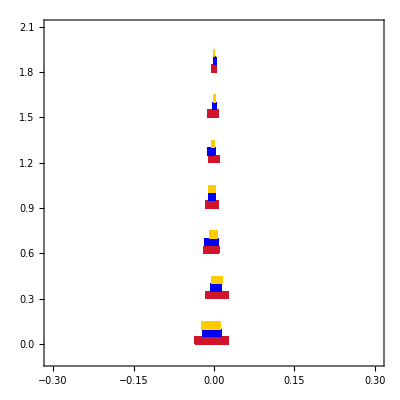

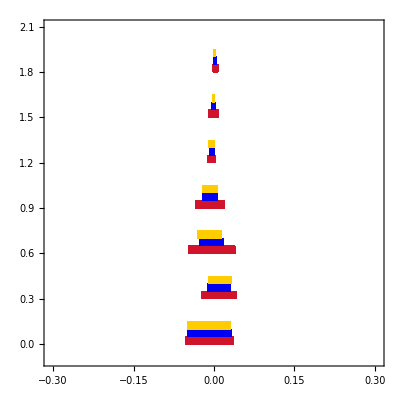

```mathematica
(*----*)
Λ=2;
(*----*)

lα=e[1];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->200]

lα=e[2];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->200]

lα=e[3];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.5,1.55,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.55,1.6,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.6,1.65,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,1(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->200]
```

#### Λ = 3 TeV

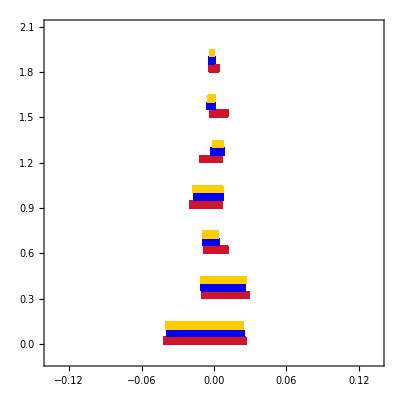

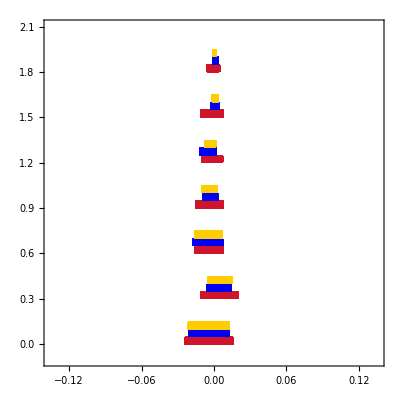

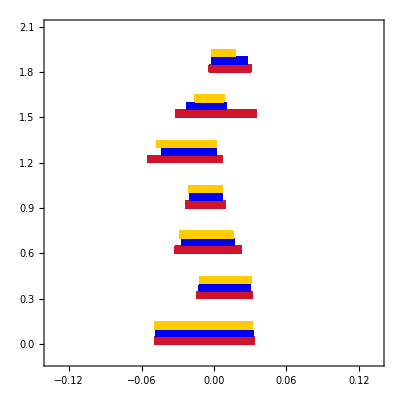

```mathematica
(*----*)
Λ=3;
(*----*)
lα=e[1];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]

lα=e[2];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]

lα=e[3];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]
```

#### Λ = 4 TeV

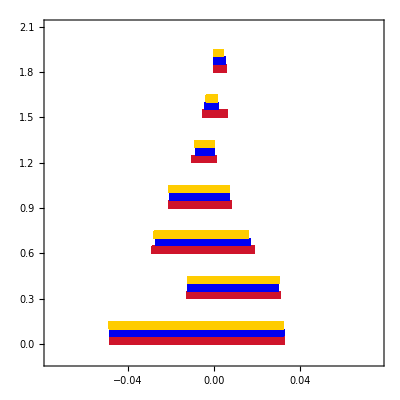

```mathematica
(*----*)
Λ=4;
(*----*)
(*
lα=e[1];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->200]

lα=e[2];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->200]
*)
lα=e[3];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.5,1.55,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.55,1.6,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.6,1.65,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,1(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->200]
```

```mathematica
Export["ee_marginal.jpg",Rasterize[eefig,ImageResolution->300]];
Export["mumu_marginal.jpg",Rasterize[μμfig,ImageResolution->300]];
Export["tata_marginal.jpg",Rasterize[ττfig,ImageResolution->300]];

Export["ee_marginal.pdf",Rasterize[eefig,ImageResolution->300]];
Export["mumu_marginal.pdf",Rasterize[μμfig,ImageResolution->300]];
Export["tata_marginal.pdf",Rasterize[ττfig,ImageResolution->300]];
```

#### Λ = 5 TeV

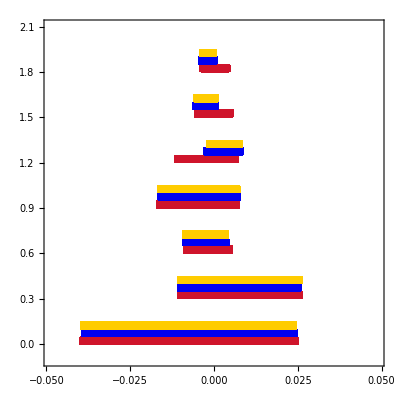

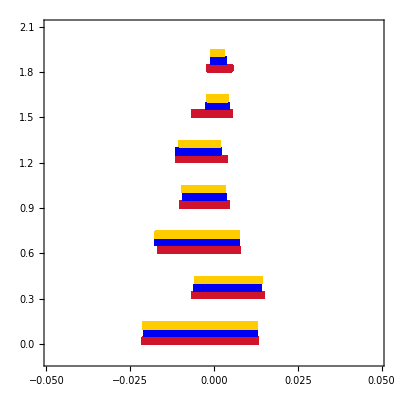

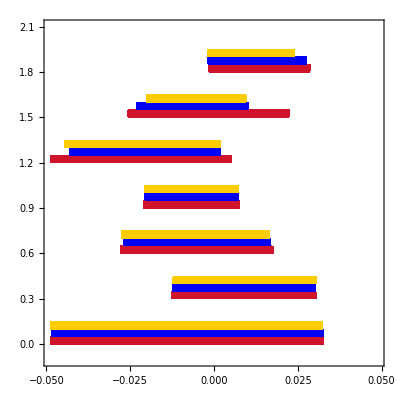

```mathematica
(*----*)
Λ=5;
(*----*)
lα=e[1];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]

lα=e[2];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]

lα=e[3];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]
```

#### Λ = 6 TeV

```mathematica
(*----*)
Λ=6;
(*----*)
(*lα=e[1];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->200]

lα=e[2];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->200]*)

lα=e[3];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.5,1.55,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.55,1.6,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.6,1.65,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,1(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->200]
```

-Graphics-

#### Λ = 7 TeV

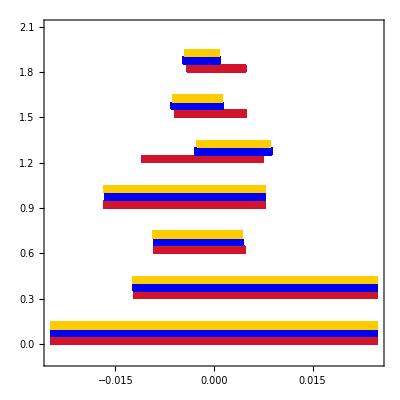

```mathematica
(*----*)
Λ=7;
(*----*)
lα=e[1];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]
(*
lα=e[2];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]

lα=e[3];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]*)
```

#### Λ = 8 TeV

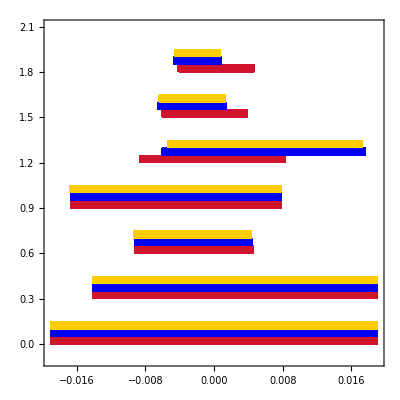

```mathematica
(*----*)
Λ=8;
(*----*)
lα=e[1];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,10(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,10(vev/Λ)^2]["uv"],

LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]
(*
lα=e[2];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]

lα=e[3];
IntervalPlot[lα,Λ]=RegionPlot[{
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervals["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervals["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]
*)
```

#### Λ = 2 TeV EXPECTED

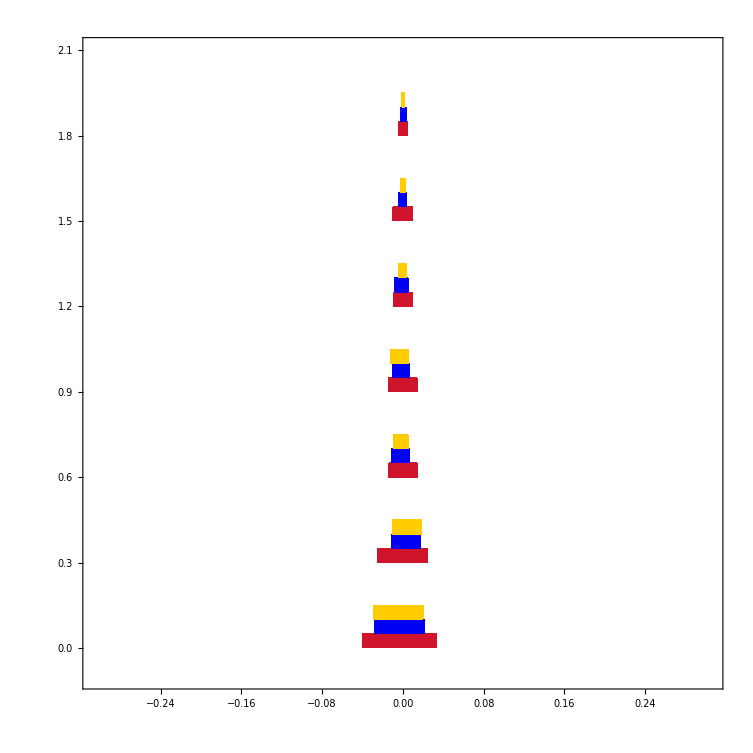

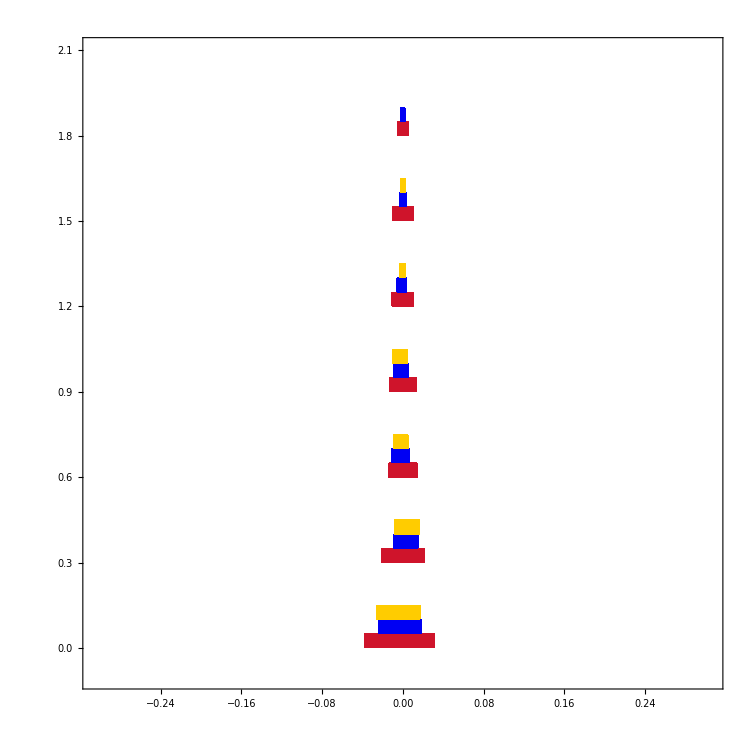

```mathematica
(*----*)
Λ=2;
(*----*)

lα=e[1];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->200]

lα=e[2];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->200]

(*lα=e[3];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.5,1.55,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.55,1.6,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.6,1.65,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,1(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->200]*)
```

#### Λ = 3 TeV EXPECTED

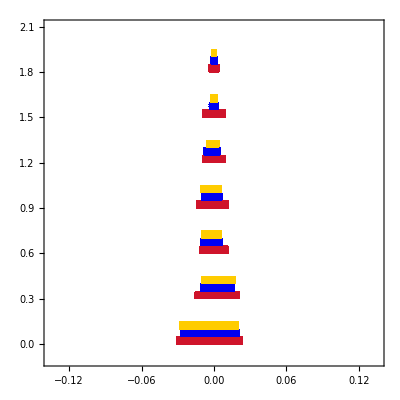

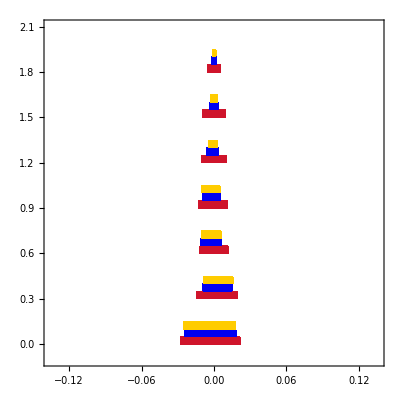

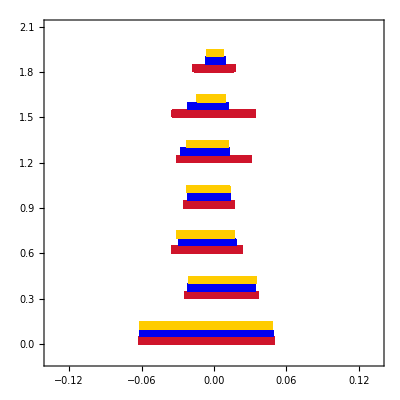

```mathematica
(*----*)
Λ=3;
(*----*)
lα=e[1];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]

lα=e[2];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]

lα=e[3];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]
```

#### Λ = 4 TeV EXPECTED

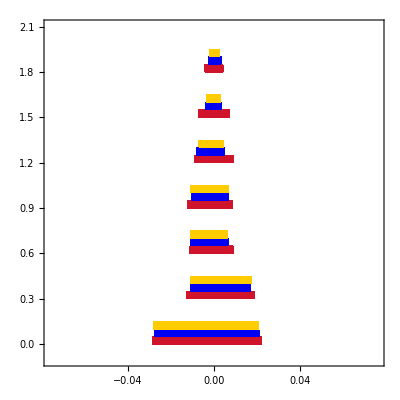

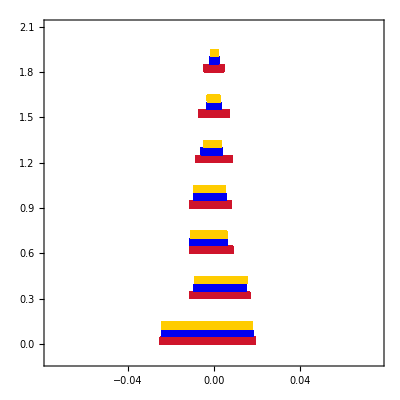

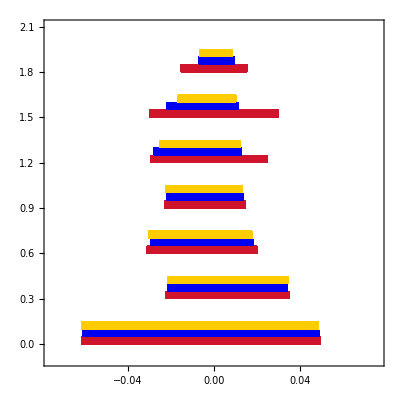

```mathematica
(*----*)
Λ=4;
(*
(*----*)
lα=e[1];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]

lα=e[2];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]
*)
lα=e[3];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.5,1.55,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]
```

```mathematica
Export["ee_marginal.jpg",Rasterize[eefig,ImageResolution->300]];
Export["mumu_marginal.jpg",Rasterize[μμfig,ImageResolution->300]];
Export["tata_marginal.jpg",Rasterize[ττfig,ImageResolution->300]];

Export["ee_marginal.pdf",Rasterize[eefig,ImageResolution->300]];
Export["mumu_marginal.pdf",Rasterize[μμfig,ImageResolution->300]];
Export["tata_marginal.pdf",Rasterize[ττfig,ImageResolution->300]];
```

#### Λ = 5 TeV EXPECTED

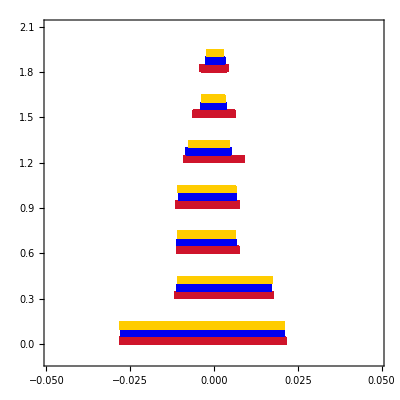

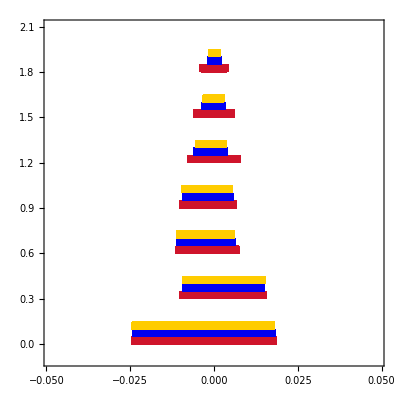

-Graphics-

```mathematica
(*----*)
Λ=5;
(*----*)
lα=e[1];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]

lα=e[2];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]

lα=e[3];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]
```

#### Λ = 6 TeV EXPECTED

```mathematica
(*----*)
Λ=6;
(*----*)
lα=e[1];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]

lα=e[2];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]

lα=e[3];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]
```

-Graphics-

-Graphics-

-Graphics-

#### Λ = 7 TeV EXPECTED

```mathematica
(*----*)
Λ=7;
(*----*)
lα=e[1];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]

lα=e[2];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]

lα=e[3];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]
```

-Graphics-

-Graphics-

-Graphics-

#### Λ = 8 TeV EXPECTED

```mathematica
(*----*)
Λ=8;
(*----*)
lα=e[1];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-electron-ATLAS",lα,ν[1],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-electron-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]

lα=e[2];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-muon-ATLAS",lα,ν[2],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-muon-CMS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]

lα=e[3];
IntervalPlotEXPECTED[lα,Λ]=RegionPlot[{
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.0,0.05,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.05,0.1,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[3],d[3],Λ,x,y, 0.1,0.15,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.3,0.35,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.35,0.4,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[2],u[2],Λ,x,y, 0.4,0.45,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.6,0.65,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.65,0.7,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[2],d[2],Λ,x,y, 0.7,0.75,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.9,0.95,1(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 0.95,1.0,1(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[2],d[2],Λ,x,y, 1.0,1.05,1(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.2,1.25,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.25,1.3,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,d[1],d[1],Λ,x,y, 1.3,1.35,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.5,1.55,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.55,1.6,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["mono-tau-ATLAS",lα,ν[3],u[1],d[1],Λ,x,y, 1.6,1.65,5(vev/Λ)^2]["uv"],

LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.8,1.85,5(vev/Λ)^2]["profiled"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.85,1.9,5(vev/Λ)^2]["single-limit"],
LimitIntervalsEXPECTED["di-tau-ATLAS",lα,lα,u[1],u[1],Λ,x,y, 1.9,1.95,5(vev/Λ)^2]["uv"]
},{x,-20(vev/Λ)^2,20(vev/Λ)^2},{y,-0.1,2.1}, PlotStyle->{rojo,azul,amarillo},BoundaryStyle->None, PlotPoints->100]
```

-Graphics-

-Graphics-

-Graphics-

## plots

```mathematica
AllPlots[Intervalplot_,lep_]:={Show[{Intervalplot[e[lep],2],PertPlot[2]},
PlotRange->{{-0.06,0.06},{-0.1,2.1}},
AspectRatio->1.0,
ImageSize->350,
Frame->{True,True,True,True},
FrameTicks->axes,
Epilog-> Epil[2,5],
FrameLabel->{MaTeX["\\left[\\mathcal{F}^{\,LL,\,qq\\prime}_{V\,(0,0)}\\right]_{"<>ToString[lep]<>ToString[lep]<>"ij}",Magnification->1.75],None},
FrameStyle->Directive[Black,Thickness[0.003]]],
Show[{Intervalplot[e[lep],3],PertPlot[3]},
PlotRange->{{-0.06,0.06},{-0.1,2.1}},
AspectRatio->1.0,
ImageSize->350,
Frame->{True,True,True,True},
FrameTicks->axes,
Epilog-> Epil[3,5],
FrameLabel->{MaTeX["\\left[\\mathcal{F}^{\,LL,\,qq\\prime}_{V\,(0,0)}\\right]_{"<>ToString[lep]<>ToString[lep]<>"ij}",Magnification->1.75],None},
FrameStyle->Directive[Black,Thickness[0.003]]],
Show[{Intervalplot[e[lep],4],PertPlot[4]},
PlotRange->{{-0.06,0.06},{-0.1,2.1}},
AspectRatio->1.0,
ImageSize->350,
Frame->{True,True,True,True},
FrameTicks->axes,
Epilog-> Epil[4,5],
FrameLabel->{MaTeX["\\left[\\mathcal{F}^{\,LL,\,qq\\prime}_{V\,(0,0)}\\right]_{"<>ToString[lep]<>ToString[lep]<>"ij}",Magnification->1.75],None},
FrameStyle->Directive[Black,Thickness[0.003]]],
Show[{Intervalplot[e[lep],5],PertPlot[5]},
PlotRange->{{-0.06,0.06},{-0.1,2.1}},
AspectRatio->1.0,
ImageSize->350,
Frame->{True,True,True,True},
FrameTicks->axes,
Epilog-> Epil[5,5],
FrameLabel->{MaTeX["\\left[\\mathcal{F}^{\,LL,\,qq\\prime}_{V\,(0,0)}\\right]_{"<>ToString[lep]<>ToString[lep]<>"ij}",Magnification->1.75],None},
FrameStyle->Directive[Black,Thickness[0.003]]],
Show[{Intervalplot[e[lep],6],PertPlot[6]},
PlotRange->{{-0.06,0.06},{-0.1,2.1}},
AspectRatio->1.0,
ImageSize->350,
Frame->{True,True,True,True},
FrameTicks->axes,
Epilog-> Epil[6,5],
FrameLabel->{MaTeX["\\left[\\mathcal{F}^{\,LL,\,qq\\prime}_{V\,(0,0)}\\right]_{"<>ToString[lep]<>ToString[lep]<>"ij}",Magnification->1.75],None},
FrameStyle->Directive[Black,Thickness[0.003]]],
Show[{Intervalplot[e[lep],7],PertPlot[7]},
PlotRange->{{-0.06,0.06},{-0.1,2.1}},
AspectRatio->1.0,
ImageSize->350,
Frame->{True,True,True,True},
FrameTicks->axes,
Epilog-> Epil[7,5],
FrameLabel->{MaTeX["\\left[\\mathcal{F}^{\,LL,\,qq\\prime}_{V\,(0,0)}\\right]_{"<>ToString[i]<>ToString[i]<>"ij}",Magnification->1.75],None},
FrameStyle->Directive[Black,Thickness[0.003]]],
Show[{Intervalplot[e[lep],8],PertPlot[8]},
PlotRange->{{-0.06,0.06},{-0.1,2.1}},
AspectRatio->1.0,
ImageSize->350,
Frame->{True,True,True,True},
FrameTicks->axes,
Epilog-> Epil[8,5],
FrameLabel->{MaTeX["\\left[\\mathcal{F}^{\,LL,\,qq\\prime}_{V\,(0,0)}\\right]_{"<>ToString[lep]<>ToString[lep]<>"ij}",Magnification->1.75],None},
FrameStyle->Directive[Black,Thickness[0.003]]]
}
```

```mathematica
AllPlots[IntervalPlot,1]
AllPlots[IntervalPlot,2]
AllPlots[IntervalPlot,3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
lep=1;
Plotdim8e2=Show[{IntervalPlot[e[lep],2],PertPlot[2]},
PlotRange->{{-0.06,0.06},{-0.1,2.1}},
AspectRatio->1.0,
ImageSize->350,
Frame->{True,True,True,True},
FrameTicks->axes,
Epilog-> Epil[2,5],
PlotStyle->{rojo,azul,amarillo},
FrameLabel->{MaTeX["\\left[\\mathcal{F}^{\,LL,\,qq\\prime}_{V\,(0,0)}\\right]_{"<>ToString[lep]<>ToString[lep]<>"ij}",Magnification->1.75],None},
FrameStyle->Directive[Black,Thickness[0.003]]]
Plotdim8e4=Show[{IntervalPlot[e[lep],4],PertPlot[4]},
PlotRange->{{-0.06,0.06},{-0.1,2.1}},
AspectRatio->1.0,
ImageSize->350,
Frame->{True,True,True,True},
FrameTicks->axes,
Epilog-> Epil[4,5],
PlotStyle->{rojo,azul,amarillo},
FrameLabel->{MaTeX["\\left[\\mathcal{F}^{\,LL,\,qq\\prime}_{V\,(0,0)}\\right]_{"<>ToString[lep]<>ToString[lep]<>"ij}",Magnification->1.75],None},
FrameStyle->Directive[Black,Thickness[0.003]]]
Plotdim8e6=Show[{IntervalPlot[e[lep],6],PertPlot[6]},
PlotRange->{{-0.06,0.06},{-0.1,2.1}},
AspectRatio->1.0,
ImageSize->350,
Frame->{True,True,True,True},
FrameTicks->axes,
Epilog-> Epil[6,5],
PlotStyle->{rojo,azul,amarillo},
FrameLabel->{MaTeX["\\left[\\mathcal{F}^{\,LL,\,qq\\prime}_{V\,(0,0)}\\right]_{"<>ToString[lep]<>ToString[lep]<>"ij}",Magnification->1.75],None},
FrameStyle->Directive[Black,Thickness[0.003]]]

lep=2;
Plotdim8μ2=Show[{IntervalPlot[e[lep],2],PertPlot[2]},
PlotRange->{{-0.06,0.06},{-0.1,2.1}},
AspectRatio->1.0,
ImageSize->350,
Frame->{True,True,True,True},
FrameTicks->axes,
Epilog-> Epil[2,5],
PlotStyle->{rojo,azul,amarillo},
FrameLabel->{MaTeX["\\left[\\mathcal{F}^{\,LL,\,qq\\prime}_{V\,(0,0)}\\right]_{"<>ToString[lep]<>ToString[lep]<>"ij}",Magnification->1.75],None},
FrameStyle->Directive[Black,Thickness[0.003]]]
Plotdim8μ4=Show[{IntervalPlot[e[lep],4],PertPlot[4]},
PlotRange->{{-0.06,0.06},{-0.1,2.1}},
AspectRatio->1.0,
ImageSize->350,
Frame->{True,True,True,True},
FrameTicks->axes,
Epilog-> Epil[4,5],
PlotStyle->{rojo,azul,amarillo},
FrameLabel->{MaTeX["\\left[\\mathcal{F}^{\,LL,\,qq\\prime}_{V\,(0,0)}\\right]_{"<>ToString[lep]<>ToString[lep]<>"ij}",Magnification->1.75],None},
FrameStyle->Directive[Black,Thickness[0.003]]]
Plotdim8μ6=Show[{IntervalPlot[e[lep],6],PertPlot[6]},
PlotRange->{{-0.06,0.06},{-0.1,2.1}},
AspectRatio->1.0,
ImageSize->350,
Frame->{True,True,True,True},
FrameTicks->axes,
Epilog-> Epil[6,5],
PlotStyle->{rojo,azul,amarillo},
FrameLabel->{MaTeX["\\left[\\mathcal{F}^{\,LL,\,qq\\prime}_{V\,(0,0)}\\right]_{"<>ToString[lep]<>ToString[lep]<>"ij}",Magnification->1.75],None},
FrameStyle->Directive[Black,Thickness[0.003]]]

lep=3;
Plotdim8τ2=Show[{IntervalPlot[e[lep],2],PertPlot[2]},
PlotRange->{{-0.06,0.06},{-0.1,2.1}},
AspectRatio->1.0,
ImageSize->350,
Frame->{True,True,True,True},
FrameTicks->axes,
Epilog-> Epil[2,1],
FrameLabel->{MaTeX["\\left[\\mathcal{F}^{\,LL,\,qq\\prime}_{V\,(0,0)}\\right]_{"<>ToString[lep]<>ToString[lep]<>"ij}",Magnification->1.75],None},
FrameStyle->Directive[Black,Thickness[0.003]]]
Plotdim8τ4=Show[{IntervalPlot[e[lep],4],PertPlot[4]},
PlotRange->{{-0.06,0.06},{-0.1,2.1}},
AspectRatio->1.0,
ImageSize->350,
Frame->{True,True,True,True},
FrameTicks->axes,
Epilog-> Epil[4,1],
PlotStyle->{rojo,azul,amarillo},
FrameLabel->{MaTeX["\\left[\\mathcal{F}^{\,LL,\,qq\\prime}_{V\,(0,0)}\\right]_{"<>ToString[lep]<>ToString[lep]<>"ij}",Magnification->1.75],None},
FrameStyle->Directive[Black,Thickness[0.003]]]
Plotdim8τ6=Show[{IntervalPlot[e[lep],6],PertPlot[6]},
PlotRange->{{-0.06,0.06},{-0.1,2.1}},
AspectRatio->1.0,
ImageSize->350,
Frame->{True,True,True,True},
FrameTicks->axes,
Epilog-> Epil[6,1],
PlotStyle->{rojo,azul,amarillo},
FrameLabel->{MaTeX["\\left[\\mathcal{F}^{\,LL,\,qq\\prime}_{V\,(0,0)}\\right]_{"<>ToString[lep]<>ToString[lep]<>"ij}",Magnification->1.75],None},
FrameStyle->Directive[Black,Thickness[0.003]]]
```

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

```mathematica
Export["ee_marginal_2.pdf",Rasterize[Plotdim8e2,ImageResolution->400]];
Export["ee_marginal_4.pdf",Rasterize[Plotdim8e4,ImageResolution->400]];
Export["ee_marginal_6.pdf",Rasterize[Plotdim8e6,ImageResolution->400]];
Export["mumu_marginal_2.pdf",Rasterize[Plotdim8μ2,ImageResolution->400]];
Export["mumu_marginal_4.pdf",Rasterize[Plotdim8μ4,ImageResolution->400]];
Export["mumu_marginal_6.pdf",Rasterize[Plotdim8μ6,ImageResolution->400]];
Export["tata_marginal_2.pdf",Rasterize[Plotdim8τ2,ImageResolution->400]];
Export["tata_marginal_4.pdf",Rasterize[Plotdim8τ4,ImageResolution->400]];
Export["tata_marginal_6.pdf",Rasterize[Plotdim8τ6,ImageResolution->400]];
```

```mathematica
IntervalPlot[e[o],o]
```

IntervalPlot[e[o],o]

```mathematica
rojo
azul
amarillo
```

RGBColor[0.8117647058823529, 0.0784313725490196, 0.16862745098039217]

RGBColor[0., 0., 0.9529411764705882]

RGBColor[1., 0.8, 0.]

```mathematica
549+472
```

1021